# שורשים

## גמטריה

```mathematica
Off[General::spell,General::spell1]
```

```mathematica
SetDirectory["/Users/brianbec/Documents/MINE/NonTechnical/TorahData"];
```

```mathematica
$RecursionLimit=65535;
```

```mathematica
gematria={")"->1,"B"->2,"G"->3,"D"->4,"H"->5,"W"->6,"Z"->7,"X"->8,"+"->9,"Y"->10,"K"->20,"L"->30,"M"->40,"N"->50,"S"->60,"("->70,"P"->80,"C"->90,"Q"->100,"R"->200,"$"->300,"T"->400, "k"->500,"m"->600,"n"->700,"p"->800,"c"->900}
```

{)→1,B→2,G→3,D→4,H→5,W→6,Z→7,X→8,+→9,Y→10,K→20,L→30,M→40,N→50,S→60,(→70,P→80,C→90,Q→100,R→200,$→300,T→400,k→500,m→600,n→700,p→800,c→900}

```mathematica
gematria2={"א"->1,"ב"->2,"ג"->3,"ד"->4,"ה"->5,"ו"->6,"ז"->7,"ח"->8,"ט"->9,"י"->10,"כ"->20,"ל"->30,"מ"->40,"נ"->50,"ס"->60,"ע"->70,"פ"->80,"צ"->90,"ק"->100,"ר"->200,"ש"->300,"ת"->400, "ך"->500,"ם"->600,"ן"->700,"ף"->800,"ץ"->900}
```

{א→1,ב→2,ג→3,ד→4,ה→5,ו→6,ז→7,ח→8,ט→9,י→10,כ→20,ל→30,מ→40,נ→50,ס→60,ע→70,פ→80,צ→90,ק→100,ר→200,ש→300,ת→400,ך→500,ם→600,ן→700,ף→800,ץ→900}

Michigan-to-Hebrew

```mathematica
michiganToHebrewRules=MapThread[Rule[#1⟦1⟧,#2⟦1⟧]&,{gematria,gematria2}]
```

{)→א,B→ב,G→ג,D→ד,H→ה,W→ו,Z→ז,X→ח,+→ט,Y→י,K→כ,L→ל,M→מ,N→נ,S→ס,(→ע,P→פ,C→צ,Q→ק,R→ר,$→ש,T→ת,k→ך,m→ם,n→ן,p→ף,c→ץ}

```mathematica
michiganToHebrew[michigan_String]:=StringJoin[Characters[michigan]/.michiganToHebrewRules]
```

```mathematica
michiganToHebrew["BWk"]
```

בוך

Maximum number of roots, sofetim optional:

```mathematica
22*22*27
```

13068

Maximum number of roots, sofetim required:

```mathematica
22^3
```

10648

Maximum number of roots, waw excluded in first position, sofetim required:

```mathematica
21*22^2
```

10164

Maximum number of roots, waw exluded in first position, sofetim optional:

```mathematica
21*22*27
```

12474

```mathematica
revgam=Reverse/@gematria
```

{1→),2→B,3→G,4→D,5→H,6→W,7→Z,8→X,9→+,10→Y,20→K,30→L,40→M,50→N,60→S,70→(,80→P,90→C,100→Q,200→R,300→$,400→T,500→k,600→m,700→n,800→p,900→c}

```mathematica
revgam2=Reverse/@gematria2
```

{1→א,2→ב,3→ג,4→ד,5→ה,6→ו,7→ז,8→ח,9→ט,10→י,20→כ,30→ל,40→מ,50→נ,60→ס,70→ע,80→פ,90→צ,100→ק,200→ר,300→ש,400→ת,500→ך,600→ם,700→ן,800→ף,900→ץ}

```mathematica
misparim=First/@revgam
```

{1,2,3,4,5,6,7,8,9,10,20,30,40,50,60,70,80,90,100,200,300,400,500,600,700,800,900}

```mathematica
otayot=First/@gematria
```

{),B,G,D,H,W,Z,X,+,Y,K,L,M,N,S,(,P,C,Q,R,$,T,k,m,n,p,c}

```mathematica
otayot2=First/@gematria2
```

{א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת,ך,ם,ן,ף,ץ}

```mathematica
indices=MapThread[Rule,{otayot,Range[27]}]
```

{)→1,B→2,G→3,D→4,H→5,W→6,Z→7,X→8,+→9,Y→10,K→11,L→12,M→13,N→14,S→15,(→16,P→17,C→18,Q→19,R→20,$→21,T→22,k→23,m→24,n→25,p→26,c→27}

```mathematica
indices2=MapThread[Rule,{otayot2,Range[27]}]
```

{א→1,ב→2,ג→3,ד→4,ה→5,ו→6,ז→7,ח→8,ט→9,י→10,כ→11,ל→12,מ→13,נ→14,ס→15,ע→16,פ→17,צ→18,ק→19,ר→20,ש→21,ת→22,ך→23,ם→24,ן→25,ף→26,ץ→27}

```mathematica
gem[dvar_String]:=Plus@@Characters[dvar]/.gematria
```

Sofetim (ending letter forms) give the appropriate answer:

```mathematica
gem2[dvar_String]:=Plus@@Characters[dvar]/.gematria2
```

```mathematica
gem["BWk"]
```

508

```mathematica
gem2["בוך"]
```

508

Forms without sofetim also work:

```mathematica
gem["BWK"]
```

28

```mathematica
gem2["בוכ"]
```

28

Some mistakes are visible:

```mathematica
gem["BwK"]
```

w+22

Some aren't:

```mathematica
gem["BkW"]
```

508

You must by hand make sure not to generate mistakes like that last one.

## לשורשים ממספרים

There are various schemes for gematria of shoreshim with respect to sofet letters: allowed, required, excluded. Sofetim are never permitted in the middle of shoreshim. To make the gematria easier to understand, in the allowed and excluded schemes, we write the shoreshim that do not contain sofetim in the unnatural form: without sofetim. In other words, with regard to gematria, sofetim are strict numerical values and not typographical flourishes. A shoresh written with a sofet letter is always reckoned with the large numbers (500 - 900) of sofet letters.

```mathematica
<<"Combinatorica`"
```

Sofetim allowed:

```mathematica
shoreshim[n_Integer]:=Module[{u,v},
u=Select[Compositions[n,3],
Apply[And,
Map[MemberQ[misparim,#]&,#]]&];(* all are misparim *)
v=Select[u,#⟦1⟧<500&&#⟦2⟧<500&];(* only non-sofetim in 1,2 *)
Map[StringJoin,v/.revgam]]
```

Sofetim required:

```mathematica
shoreshim2[n_Integer]:=Module[{u,v,w},
u=Select[Compositions[n,3],
Apply[And,
Map[MemberQ[misparim,#]&,#]]&];(* all are misparim *)
v=Select[u,#⟦1⟧<500&&#⟦2⟧<500&];(* only non-sofetim in 1,2 *)
w=Select[v,#⟦3⟧≠20&&#⟦3⟧≠40&&#⟦3⟧≠50&&#⟦3⟧≠80&&#⟦3⟧≠90&];
(* check last letter is not non-sofet *)
Map[StringJoin,w/.revgam]]
```

Sofetim excluded:

```mathematica
shoreshim3[n_Integer]:=Module[{u,v},
u=Select[Compositions[n,3],
Apply[And,
Map[MemberQ[misparim,#]&,#]]&];(* all are misparim *)
v=Select[u,#⟦1⟧<500&&#⟦2⟧<500&&#⟦3⟧<500&];(* only non-sofetim *)
Map[StringJoin,v/.revgam]]
```

The smallest shoresh is אאא:

```mathematica
gem2["אאא"]
```

3

The largest shoresh is תתץ:

```mathematica
gem2["תתץ"]
```

1700

"Shoreshim" takes a long time to compute. I ran it for ten hours over the numbers from 3 to 1700, which are the minimum and maximum gematria, respectively, and stored the results. Read them back right here:

Prepend two empty lists to "allShoreshim" to account for the gematria 1 and 2, which have no shoreshim:

Don't run the following "shoreshim" commands unless you need to check the results stored in "allShoreshim." They take an unpleasantly long time. I've checked that the stored results are good.

```mathematica
allShoreshim2=Map[Function[ss,michiganToHebrew/@ss],allShoreshim]
```

{{},{},{אאא},{אאב,אבא,באא},{אאג,אבב,אגא,באב,בבא,גאא},{אאד,אבג,אגב,אדא,באג,בבב,בגא,גאב,גבא,דאא},«1688»,{},{},{},{},{},{תתץ}}

```mathematica
(* michiganToHebrew /@ shoreshim[850]//StandardForm *)
```

{ימף,כלף,לכף,מיף,נקן,נרם,נשך,נתת,סצן,עפן,פען,צסן,קנן,רנם,שנך,תנת,תתנ}

```mathematica
(* michiganToHebrew /@ shoreshim2[850]//StandardForm *)
```

{ימף,כלף,לכף,מיף,נקן,נרם,נשך,נתת,סצן,עפן,פען,צסן,קנן,רנם,שנך,תנת}

```mathematica
(* michiganToHebrew /@ shoreshim3[850]//StandardForm *)
```

{נתת,תנת,תתנ}

```mathematica
michiganToHebrew/@allShoreshim⟦850⟧//StandardForm
```

{ימף,כלף,לכף,מיף,נקן,נרם,נשך,נתת,סצן,עפן,פען,צסן,קנן,רנם,שנך,תנת,תתנ}

```mathematica
sofetimRequired[shs_]:=
Select[shs,
Function[sh,Module[{c=michiganToHebrew@Characters[sh]⟦3⟧},
c≠"כ"&&c≠"נ"&&c≠"מ"&&c≠"פ"&&c≠"צ"]]]
```

```mathematica
(* sofetimRequired[allShoreshim⟦850⟧]==shoreshim2[850] *)
```

True

```mathematica
sofetimRequired[allShoreshim2⟦850⟧]==michiganToHebrew/@sofetimRequired[allShoreshim⟦850⟧]
```

True

```mathematica
sofetimExcluded[shs_]:=
Select[shs,
Function[sh,Module[{c=michiganToHebrew@Characters[sh]⟦3⟧},
c≠"ך"&&c≠"ן"&&c≠"ם"&&c≠"ף"&&c≠"ץ"]]]
```

```mathematica
(* sofetimExcluded[allShoreshim⟦850⟧]==shoreshim3[850] *)
```

True

```mathematica
michiganToHebrew/@sofetimRequired@allShoreshim⟦850⟧
```

{ימף,כלף,לכף,מיף,נקן,נרם,נשך,נתת,סצן,עפן,פען,צסן,קנן,רנם,שנך,תנת}

```mathematica
sofetimRequired@allShoreshim2⟦850⟧
```

{ימף,כלף,לכף,מיף,נקן,נרם,נשך,נתת,סצן,עפן,פען,צסן,קנן,רנם,שנך,תנת}

```mathematica
(* shoreshim[200]//StandardForm *)
```

```mathematica
sofetimRequired@allShoreshim2⟦200⟧//StandardForm
```

{יצק,כפק,לעק,לקע,מסק,מצע,מקס,ננק,נפע,נצס,סמק,סעע,ספס,עלק,עסע,עעס,עקל,פכק,פנע,פסס,פצל,ציק,צמע,צנס,צפל,צקי,קלע,קמס,קעל,קצי}

```mathematica
sofetimExcluded@allShoreshim2⟦200⟧//StandardForm
```

{יצק,יקצ,כפק,כצצ,כקפ,לעק,לפצ,לצפ,לקע,מסק,מעצ,מפפ,מצע,מקס,ננק,נסצ,נעפ,נפע,נצס,נקנ,סמק,סנצ,סספ,סעע,ספס,סצנ,סקמ,עלק,עמצ,ענפ,עסע,עעס,עפנ,עצמ,עקל,פכק,פלצ,פמפ,פנע,פסס,פענ,פפמ,פצל,פקכ,ציק,צכצ,צלפ,צמע,צנס,צסנ,צעמ,צפל,צצכ,צקי,קיצ,קכפ,קלע,קמס,קננ,קסמ,קעל,קפכ,קצי}

```mathematica
(* shoreshim[613]==allShoreshim⟦613⟧ *)
```

True

```mathematica
allShoreshim2⟦613⟧//StandardForm
```

{גים,דטם,החם,וזם,זום,חהם,טדם,יגם}

```mathematica
sofetimRequired@allShoreshim2⟦613⟧//StandardForm
```

{גים,דטם,החם,וזם,זום,חהם,טדם,יגם}

```mathematica
sofetimExcluded@allShoreshim2⟦613⟧//StandardForm
```

{}

Let's see how many theoretical shoreshim there are for each number from 1 to 1700. First, just the range from 3 to 300:

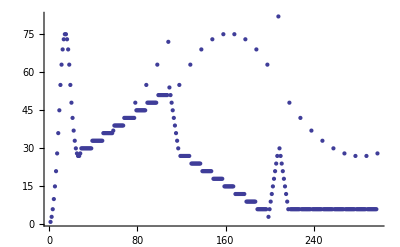
{0.001077,-Graphics-}

```mathematica
Timing[ListPlot[Length/@(allShoreshim2⟦#⟧&)/@Range[3,300]]]
```

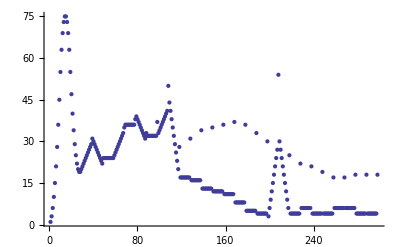
{0.15843,-Graphics-}

```mathematica
Timing[ListPlot[Length/@(sofetimRequired@allShoreshim2⟦#⟧&)/@Range[3,300]]]
```

```mathematica
Timing[ListPlot[Length/@(sofetimExcluded@allShoreshim2⟦#⟧&)/@Range[3,300]]]
```

{0.158118,-Graphics-}

Look at the ones from 300 to 600:

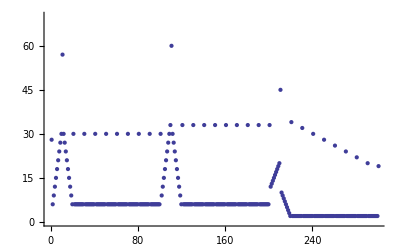

```mathematica
ListPlot[Length/@(allShoreshim2⟦#1⟧&)/@Range[300,600],PlotRange->{{0,300},{0,70}}]
```

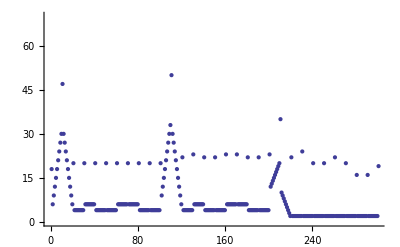

```mathematica
ListPlot[Length/@(sofetimRequired@allShoreshim2⟦#1⟧&)/@Range[300,600],PlotRange->{{0,300},{0,70}}]
```

The ones from 600 to 900

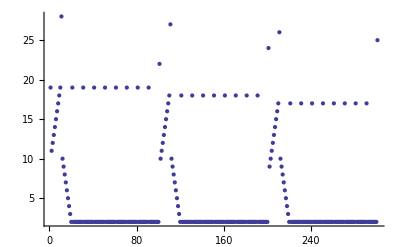

```mathematica
ListPlot[Length/@(allShoreshim2⟦#1⟧&)/@Range[600,900]]
```

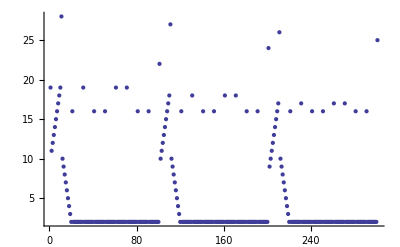

```mathematica
ListPlot[Length/@(sofetimRequired@allShoreshim2⟦#1⟧&)/@Range[600,900]]
```

From 900 to 1700

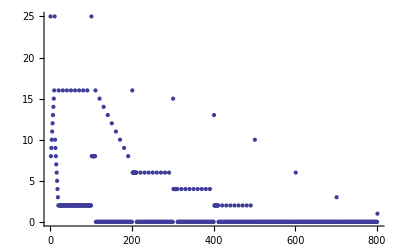

```mathematica
ListPlot[Length/@(allShoreshim2⟦#1⟧&)/@Range[900,1700]]
```

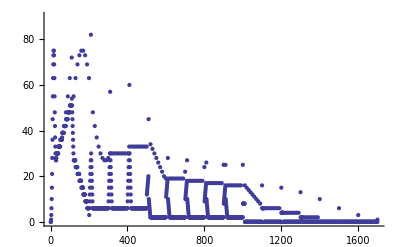

```mathematica
ListPlot[Length/@(allShoreshim2⟦#1⟧&)/@Range[1,1700],PlotRange->{{0,1700},{0,90}}]
```

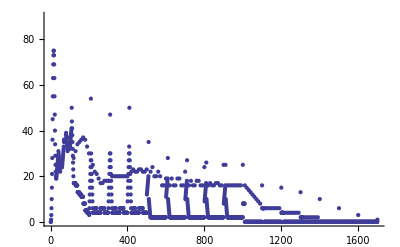

```mathematica
ListPlot[Length/@(sofetimRequired@allShoreshim2⟦#1⟧&)/@Range[1,1700],PlotRange->{{0,1700},{0,90}}]
```

The following is great evidence that we got it all right:

```mathematica
Plus@@Length/@allShoreshim2
```

13068

```mathematica
Plus@@Length/@sofetimRequired/@allShoreshim2
```

10648

```mathematica
(* <<"BarCharts`";<<"Histograms`";<<"PieCharts`" *)
```

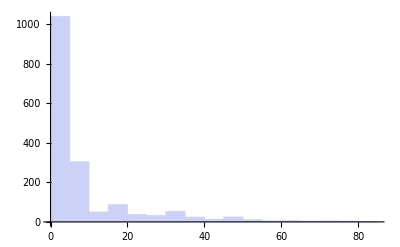

```mathematica
Histogram[Length/@allShoreshim2]
```

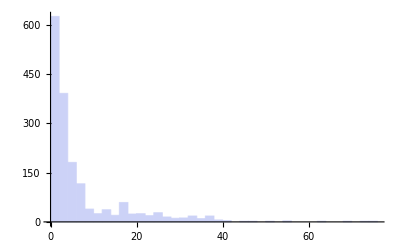

```mathematica
Histogram[Length/@sofetimRequired/@allShoreshim2]
```

Looks like gematria 210 has the largest number of shoreshim:

```mathematica
Length@allShoreshim2⟦#⟧&/@Range[200,210]
```

{63,3,6,9,12,15,18,21,24,27,82}

```mathematica
Max[Length/@allShoreshim2]
```

82

```mathematica
allShoreshim2⟦210⟧//StandardForm
```

{אטר,ארט,בחר,ברח,גזר,גרז,דור,דרו,ההר,הרה,ודר,ורד,זגר,זרג,חבר,חרב,טאר,טרא,יקק,כצק,כקצ,לפק,לצצ,לקפ,מעק,מפצ,מצפ,מקע,נסק,נעצ,נפפ,נצע,נקס,סנק,ססצ,סעפ,ספע,סצס,סקנ,עמק,ענצ,עספ,עעע,עפס,עצנ,עקמ,פלק,פמצ,פנפ,פסע,פעס,פפנ,פצמ,פקל,צכק,צלצ,צמפ,צנע,צסס,צענ,צפמ,צצל,צקכ,קיק,קכצ,קלפ,קמע,קנס,קסנ,קעמ,קפל,קצכ,קקי,ראט,רבח,רגז,רדו,רהה,רוד,רזג,רחב,רטא}

Or, when sofetim are required,

```mathematica
Max[Length/@sofetimRequired/@allShoreshim2]
```

75

```mathematica
Select[(Function[l,{#,Length[l]}]
[(sofetimRequired@allShoreshim2⟦#⟧)])&/@Range[1,1700],
#⟦2⟧==75&]
```

(16 | 75
17 | 75)

```mathematica
sofetimRequired@allShoreshim2⟦16⟧
```

{אהי,אוט,אזח,אחז,אטו,איה,בדי,בהט,בוח,בזז,בחו,בטה,ביד,גגי,גדט,גהח,גוז,גזו,גחה,גטד,גיג,דבי,דגט,דדח,דהז,דוו,דזה,דחד,דטג,דיב,האי,הבט,הגח,הדז,ההו,הוה,הזד,החג,הטב,היא,ואט,ובח,וגז,ודו,והה,ווד,וזג,וחב,וטא,זאח,זבז,זגו,זדה,זהד,זוג,זזב,זחא,חאז,חבו,חגה,חדד,חהג,חוב,חזא,טאו,טבה,טגד,טדג,טהב,טוא,יאה,יבד,יגג,ידב,יהא}

```mathematica
sofetimRequired@allShoreshim2⟦17⟧
```

{אוי,אזט,אחח,אטז,איו,בהי,בוט,בזח,בחז,בטו,ביה,גדי,גהט,גוח,גזז,גחו,גטה,גיד,דגי,דדט,דהח,דוז,דזו,דחה,דטד,דיג,הבי,הגט,הדח,ההז,הוו,הזה,החד,הטג,היב,ואי,ובט,וגח,ודז,והו,ווה,וזד,וחג,וטב,ויא,זאט,זבח,זגז,זדו,זהה,זוד,זזג,זחב,זטא,חאח,חבז,חגו,חדה,חהד,חוג,חזב,חחא,טאז,טבו,טגה,טדד,טהג,טוב,טזא,יאו,יבה,יגד,ידג,יהב,יוא}

Shoresh to Cube to Triangle

```mathematica
otayot2
```

{א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת,ך,ם,ן,ף,ץ}

The idea here is that the letters from א to י live on one 3x3 plane, the letters from כ through צ live on the next 3x3 plane, and the letters from ק through ץ live on a third 3x3 plane. A shoresh, then, specifies three points in a 3x3x3 cube, and we can draw a triangle.

There might be lots of other ways of plotting a shoresh in space, but this is the one that popped to mind first to investigate.

Here are the 27 coordinates we're going to map to the letters.

```mathematica
Tuples[{1,2,3},3]
```

(1 | 1 | 1
1 | 1 | 2
1 | 1 | 3
1 | 2 | 1
1 | 2 | 2
1 | 2 | 3
1 | 3 | 1
1 | 3 | 2
1 | 3 | 3
2 | 1 | 1
2 | 1 | 2
2 | 1 | 3
2 | 2 | 1
2 | 2 | 2
2 | 2 | 3
2 | 3 | 1
2 | 3 | 2
2 | 3 | 3
3 | 1 | 1
3 | 1 | 2
3 | 1 | 3
3 | 2 | 1
3 | 2 | 2
3 | 2 | 3
3 | 3 | 1
3 | 3 | 2
3 | 3 | 3)

```mathematica
indices2
```

{א→1,ב→2,ג→3,ד→4,ה→5,ו→6,ז→7,ח→8,ט→9,י→10,כ→11,ל→12,מ→13,נ→14,ס→15,ע→16,פ→17,צ→18,ק→19,ר→20,ש→21,ת→22,ך→23,ם→24,ן→25,ף→26,ץ→27}

```mathematica
cube[shoreshim_List]:=
Module[
{coords=Tuples[{1,2,3},3],
letterCoords,radius=0.125,opacity=0.50},
letterCoords=Function[shoresh,
coords⟦#/.indices2⟧&/@Characters[shoresh]]/@shoreshim;
Graphics3D[
{{Style[Line[{{#,1,1},{#,1,2},{#,1,3},
{#,2,3},{#,3,3},{#,3,2},
{#,3,1},{#,2,1},{#,1,1}}],Red],
Style[Line[{{#,2,1},{#,2,2},{#,2,3}}],Red],
Style[Line[{{#,1,2},{#,2,2},{#,3,2}}],Red]}&/@{1,2,3},
{Style[Line[RotateRight/@ (* coordinate grid box *)
{{#,1,1},{#,1,2},{#,1,3},
{#,2,3},{#,3,3},{#,3,2},
{#,3,1},{#,2,1},{#,1,1}}],Red],
Style[Line[RotateRight/@
{{#,2,1},{#,2,2},{#,2,3}}],Red],
Style[Line[RotateRight/@
{{#,1,2},{#,2,2},{#,3,2}}],Red]}&/@{1,2,3},
MapThread[Text[Style[#1,Medium],#2,
FormatType->OutputForm]&,{otayot2,coords}],
Function[letterCoord,
{Polygon[letterCoord],
MapThread[Style[Sphere[#1,radius],
#2,Opacity[opacity]]&,
{letterCoord,{Red,Green,Blue}}]}] (* show the letters in order *)
/@letterCoords
},FaceGrids->None,Axes->True,AxesLabel->{"x","y","z"}]]
```

```mathematica
cube[shoresh_String]:=cube[{shoresh}];
```

```mathematica
cube[shoreshim___]:=cube[{shoreshim}];
```

```mathematica
cube["קדם","ערב"]
```

-Graphics3D-

```mathematica
cube["קרב"]
```

-Graphics3D-

## תרגומים

Spelled-out English names for each letter.

```mathematica
ts=Range[22];
```

```mathematica
{alef,bet,gimel,dalet,heh,waw,zayin,chet,tet,yod,khaf,lamed,mim,nun,samech,ayin,peh,tsadeh,qof,resh,shin,tav}=ts
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

There are Hebrew-letter names for each number; these should function perfectly well as Mathematica variables, evaluating to the index of each letter.

```mathematica
ts2=Range[22];
```

```mathematica
{א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת}=ts2
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

Clark & Hirsch (this is a large, closable cell: double-clink the right-hand margin to toggle hiding)

The following are non-theoretical shoreshim.

As of 6 Oct 2006, this data has not been proofread by anyone but me; not been vetted. It took me about 30 hours to keyboard it in.

```mathematica
ts⟦alef⟧=
{")BB"->{"ripen","absorb nutrients greedily","stalk","springtime"}
,")BD"->{"lose completely","disappear","ruin","perish","lose hope of independence","lost item"}
,")BH"->{"submit to existing demand","conform","consent","accede","father","parent","counselor","poor person submitting to creditor","satisfaction","caper berry","exclamation of pain"}
,")Bk"->{"billow out","spread"}
,")BL"->{"lack wholeness","mourn","grieve","destroy","but"}
,")Bm"->{"root of )a@BIMA)EL ? Gn.10.28 son of YAQ@+An"}
,")Bn"->{"hew stone","stone","weight","threshold of womb"}
,")BS"->{"feed","digest","trough","granary"}
,")BQ"->{"dislodge","expel","wrestle","dust","powdered spices"}
,")BR"->{"soar protectively","courage","spread wing"}
,")GD"->{"combine","tie together","bunch","bundle"}
,")GZ"->{"remove from tree","nut"}
,")GL"->{"drip","drop"}
,")Gm"->{"collect in one place","collect water","bent reed","bent hook"}
,")Gn"->{"contain","brimmed basin","goblet"}
,")Gp"->{"extend","army troops","extension of ruler"}
,")GR"->{"collect","store for safekeeping","letter containing many facts","coin of substantial value"}
,")DB"->{"pain","distress"}
,")Dm"->{"earthly and solid","red","pure man","mankind","ground","earth","blood? var. DMH"}
,")Dn"->{"sustain","provide base","master","base of pillar","socket"}
,")DR"->{"exert power and status","mantle"}
,")HB"->{"love","devote completely to another"}
,")HH"->{"express pain","alas"}
,")HL"->{"radiate in all directions","pitch circular tent","tent","pitch tent","camp in tent","aloe"}
,")WB"->{"fill with rainwater","rain oracle","necromancer","cistern"}
,")WD"->{"effect results","set into motion","lever","reason for","account of","imminent calamity","vapor","mist","very"}
,")WH"->{"crave","incline","desire","choose","seek to control","coastal region","mark limits of property","mark Gn.17.11"}
,")WX"->{"scurry forth","ferret"}
,")WL"->{"vacillate","lack clarity of purpose","act foolishly","obscure knowledge","perhaps","nevertheless"}
,")Wm"->{"limit","condition reality","anything","nothing"}
,")Wn"->{"acquire","misuse means of acquisition","wealth","grieve a loss","sorrow","trouble"}
,")Wc"->{"push hurriedly to a goal","push","press"}
,")WR"->{"light","illuminate","shine","enlighten","blind","fiery furnace","sparkling eye","bearer of light","land of light","vegetable to improve vision"}
,")WT"->{"communicate","signal","emblem","ensign","miracle","word indicating direct object","sign","token","letter","symbol","glyph"}
,")ZB"->{"weaken","hinder growth","vegetable","wild plant"}
,")ZH"->{"order events, past or future","then","when"}
,")ZL"->{"disappear","go away","go"}
,")Zn"->{"listen","ponder","absorb and weight impressions"}
,")ZQ"->{"chain"}
,")ZR"->{"gird","hold together","belt","girdle"}
,")XD"->{"one","one of many"}
,")XH"->{"unify","bring together","togetherness","brother","sister","meadow","another","exclamation of joy","fireplace"}
,")XZ"->{"grasp","take hold of","possess","take hold","settle","percentage","hide","conceal"}
,")XR"->{"delay","lag","disarrange","backward","other","end","expiration","after the end","after","behind","future","ultimate","past"}
,")X$"->{"hurry","courtier","attend royalty with alacrity"}
,")+D"->{"penetrate","thorny bush"}
,")++"->{"slow","soft-speaking sorcerers"}
,")+m"->{"close","seal"}
,")+n"->{"luxuriate in fancy clothes"}
,")+R"->{"close off","left-handed"}
,")YB"->{"show emnity","enemy","hatred"}
,")YH"->{"isolate","where","island","solitary jackal","falcon","woe","sorrow","how"}
,")YL"->{"strengthen","ram","hind","grove of tall trees","oak tree"}
,")Ym"->{"fear an existing danger","dread","horror","terrorize","fearsome idol"}
,")Yn"->{"absent","where?","none","nothing"}
,")Y$"->{"withstand","exist","man of proven character"}
,")KL"->{"consume","destroy","eat","food","knife"}
,")Kp"->{"force"}
,")KR"->{"plow","turn soil over"}
,")LH"->{"swear","divinity","forward (prep.)","hailstone","master","combine elements for control","oak? of Moreh Gn.12.6.8","terebinth? BCB p.18"}
,")LX"->{"curse","corrupt"}
,")LL"->{"deny","lament","obstruct development"}
,")Lm"->{"bind","tie together","silent","dumb","widow","anonymous"}
,")Lp"->{"receive from others","mentor","guide","husband","thousand","friend","lack independence"}
,")Lc"->{"urge"}
,")L$"->{"dubious: )e@LI$AH son of YAWAN son of YeFeT","Carthage?,""Italy with Sicily"}
,")MH"->{"serve","maid-servant","pillar","support"}
,")ML"->{"weaken","bow down"}
,")Mm"->{"dependent","mother","tribe","ethnic identity","main road","if -- condition of reality","cubit","nothing"}
,")Mn"->{"depend upon","believe","trustworthy","last","care","nurse","rear","bring up","covenant","doorposts","amen","dependable worker","craftsman","truth","trust","rely upon"}
,")Mc"->{"strengthen","obstinate","strong color","force","secure"}
,")MR"->{"speak","inform","think","promise","sayings","tradition","top branch","organize speech to be heard and understood"}
,")M$"->{"pass","last night","change"}
,")MT"->{"faithfulness Gn.24.48, BDB pg 54","truth"}
,")NB"->{"spring out","hare"}
,")NH"->{"cause","direct to goal","acknowledge debt of gratitude","deliver","moan","seek quarrel","decide direction","ego in action","whither?","when?","ship en route"}
,")NX"->{"sigh","voice complaint"}
,")Nk"->{"central and pivotal","I","vertical"}
,")Nn"->{"mourn loss"}
,")NS"->{"compel","act violently"}
,")Np"->{"nostril","nose","breathe","snort","enrage","express inner feelings of anger"}
,")NQ"->{"choke out","groan from deep within","gecko"}
,")N$"->{"cause weakness","ill","mortal","suffer","fatal","self-centered people","troubled state of mankind","degenerate man","frail"}
,")Sm"->{"store","concentrate in one place"}
,")Sn"->{"distress","absorb tragedy","misfortune"}
,")Sp"->{"gather","collect from inappropriate place","take away","harvest","rear guard","rabble"}
,")SR"->{"restrain","bind","imprison","chain","forbid","tie"}
,")PD"->{"gird","priestly belt","hold in entire body"}
,")PH"->{"cover in crust","bake"}
,")PL"->{"darken","prevent light from entering"}
,")Pn"->{"create purposefully","stone wheel","purpose"}
,")PS"->{"disappear","used up","distant end","valueless"}
,")Pp"->{"pant","overwhelm","oppress","yearning countenance","even if","greedily absorb"}
,")PQ"->{"contain","wellsprings","channel holding water","source","pipe","hold back"}
,")PR"->{"cover","ash","gold dust","covered sedan","root of )OFiR ? Gn.10.29"}
,")CL"->{"distance","stand at a distance","reserve","side","elbow","set aside"}
,")CR"->{"collect","store","treasure","hoard"}
,")QH"->{"wild","wild goat"}
,")RB"->{"restrain urge to penetrate","lie in wait","barrier","windows of heaven","lair","artifice","lattice","sluice"}
,")RG"->{"weave","loom","red-colored thread","join parallel threads"}
,")RH"->{"contain","pluck","barn stall","stable","powerful leaders","lion","take and hold"}
,")RZ"->{"cedar tree","root firmly for strong growth"}
,")RX"->{"interact","guest","socialize","private road","caravan","traveler","pattern of conduct","food for the traveler","associate with people"}
,")Rk"->{"prolong","stretched skin","length","extend"}
,")Rm"->{"rise","tall palace"}
,")Rc"->{"ground","earth","country","nationality","earthen","solidify basic needs"}
,")RR"->{"isolate and bring ruin","curse","weaken internally"}
,")R$"->{"request strongly","s:exclude others","s:possess exclusively","s:take a wife"}
,")$D"->{"outflow","slope","pour out of"}
,")$H"->{"create material","be","exist","fire-shaped material","supporting pillar"}
,")$k"->{"enclose","testicles in scrotum"}
,")$L"->{"spread","tamarisk","develop outward"}
,")$m"->{"destroy inner self","guilty","guilt offering","stolen capital","self-destruct"}
,")$p"->{"heap","dung pile","quiver for arrows","sorcerer","gather"}
,")$R"->{"progress","succeed","walk forward","live in the plains","sacred trees offering blessing","counselor","step","well-trodden","cypress tree","that","who","move forward"}
,")$$"->{"nourish","nourish a fire","pluck up courage","lightning","cake baked in fire"}
,")$T"->{"hide","mole"}
,")TH"->{"come to someone","entrance"}
,")Tn"->{"reliable and strong","primitive","ancient","donkey","she-ass","birth month of great leaders"}
,")TQ"->{"protrude","buttress"}
,")TR"->{"spy a particular area","spy"}
,")TT"->{"cut","penetrate","sign","distinguishing emblem","you","with"}
};
```

```mathematica
ts⟦bet⟧=
{"B)R"->{"clarify","bring from dark to light","a well of water","pits Gn.14.1-"}
,"B)$"->{"foul","stink","arouse disgust"}
,"BBH"->{"cover a focused point"}
,"BGD"->{"cover","clothe","present outer appearance"}
,"BGH"->{"produce food","split"}
,"BD)"->{"fabricate","lie","create untruths"}
,"BDD"->{"separate","isolate","alone","besides Gn.26.1"}
,"BDH"->{"exaggerate","divine"}
,"BDL"->{"separate for positive purpose","crystallize"}
,"BDQ"->{"penetrate to repair","breach"}
,"BHH"->{"confuse elements"}
,"BH+"->{"compact","densify"}
,"BHL"->{"shock","become bewildered"}
,"BHm"->{"subordinate","domesticated beast","cattle"}
,"BHn"->{"direct","enable","thumb","big toe"}
,"BHQ"->{"clear out","empty"}
,"BHR"->{"englighten","shine"}
,"BW)"->{"come to attractive place","harvest"}
,"BWZ"->{"despise","show contempt"}
,"BWk"->{"extract","confuse"}
,"BWL"->{"lump together","chunk"}
,"BWm"->{"raise","lift up","put on pedestal"}
,"BWn"->{"mediate","in between","champion"}
,"BWS"->{"trample","subdue"}
,"BWc"->{"soften","mucky"}
,"BWQ"->{"empty","desolate"}
,"BWR"->{"dig clear pit or cistern"}
,"BW$"->{"deceive and disillusion","disappoint","shame"}
,"BZ)"->{"cut","separate"}
,"BZH"->{"scorn"}
,"BZZ"->{"divide booty"}
,"BZQ"->{"spread lightning"}
,"BZR"->{"scatter"}
,"BXH"->{"sound fearful noise"}
,"BXL"->{"abhor","greed"}
,"BXn"->{"test","test performance for quality","citadel"}
,"BXR"->{"choose from many","prefer","elect","vote for","select","elite","youth?"}
,"B+)"->{"express rashly","swear"}
,"B+H"->{"speak"}
,"B+X"->{"trust","protected"}
,"B+L"->{"void","cease"}
,"B+n"->{"protrude at center","belly","womb","convex"}
,"BYH"->{"distress","feel pain"}
,"BYn"->{"penetrate to core","have insight","understand","revelation","know","observe","divide","partition","interpolate"}
,"BYR"->{"isolate tall structure","castle","fortress"}
,"BYT"->{"protect","contain","house","receptacle","grave","jail"}
,"BK)"->{"weep","weeping willow"}
,"BKH"->{"cry due to impulse","break into tears"}
,"BKR"->{"force out","firstborn","free productive elements"}
,"BL)"->{"wear out","holes in a garment"}
,"BLG"->{"strengthen","support","recover"}
,"BLH"->{"decay","wither","grow old","debauch"}
,"BLL"->{"confound","confuse","mix new elements into existing ones","integrate","mixed colors"}
,"BLm"->{"close","restrain","inhibit"}
,"BLS"->{"search"}
,"BL("->{"swallow completely","enclose","devour","sink"}
,"BLQ"->{"destroy","devastate","render uninhabitable"}
,"BMH"->{"raise up","elevate"}
,"BNH"->{"build","form","establish","found","child","son","suburb","poplar? Gn30.37"}
,"BN+"->{"gird"}
,"BNn"->{"understand","instruct"}
,"BSS"->{"trample","thrash","roll in muck"}
,"BSR"->{"cover with protective coating","rind","husk","peel of fruit"}
,"B(D"->{"exclude others","remote","distant"}
,"B(H"->{"erupt","boil","burst"}
,"B(+"->{"scorn","kick out"}
,"B(L"->{"master","take possession","own","woo","marry"}
,"B(R"->{"burn","destroy","devoid of reason","unrestrained animal"}
,"B(T"->{"terrify","assail"}
,"BC)"->{"muddy"}
,"BCH"->{"muddy"}
,"BCL"->{"peel","uncover","onion","tulip"}
,"BC("->{"complete","purpose","conclude","finish","take advantage","break into pieces"}
,"BCC"->{"soften","tender","wet and slippery","white linen"}
,"BCQ"->{"swell","blister","rising dough"}
,"BCR"->{"harvest grapes","subdue","weaken","lessen","reinforced","protect from other forces","be precluded","be too hard to do","fortify","protected gold"}
,"BQ("->{"valley","plain","split","split wood","burst open","open crevice","bare valley between hills","half a shekel Gn.24.22"}
,"BQQ"->{"empty out","bottle from which one pours"}
,"BQR"->{"ox","distinguishing differences","examine","strive to know","morning"}
,"BQ$"->{"seek the unknown"}
,"BR)"->{"create","open","actualize","clear an opening","cut"}
,"BRD"->{"separate","hail"}
,"BRH"->{"rejuvenate","restore health","feed","field growing food"}
,"BRZ"->{"penetrate","drill hole","iron"}
,"BRX"->{"flee","evade","exit quickly","become independent"}
,"BRk"->{"bless","power growth","spur prosperity","knee","kneel","cause to kneel"}
,"BRm"->{"separate out"}
,"BRS"->{"tan animal skins"}
,"BRC"->{"burst across","overflow"}
,"BRQ"->{"flash light","brilliant stone","flashing sword"}
,"BRR"->{"cleanse","choose","brighten","clarify","purify","soap"}
,"BR$"->{"tower","tall","cypress"}
,"BRT"->{"agree","covenant","separate out parts"}
,"B$L"->{"cook","boil","sear","mature","ripen","shed earlier state"}
,"B$m"->{"s:cut up using spices"}
,"B$S"->{"trample"}
,"B$R"->{"s:cover with sensitive coating","flesh","herald"}
,"B$$"->{"disappoint","delay"}
,"BTH"->{"destroy","lay waste","desolate"}
,"BTL"->{"seclude","separate","virgin"}
,"BTQ"->{"stab","penetrate"}
,"BTR"->{"divide","separate","pieces"}
,"BTT"->{"cut off","define","liquid measure"}
};
```

```mathematica
ts⟦gimel⟧=
{"G)H"->{"project upward","raise up high","proud","grandeur","majesty"}
,"G)L"->{"release","purge","random","redeem","avenge"}
,"GB)"->{"concentrate fluids","pool"}
,"GBB"->{"curve upward"}
,"GBH"->{"high","rise high through concentration of elements","tall","haughty","eyebrows"}
,"GBX"->{"highten forehead by exposing pate"}
,"GBL"->{"border"}
,"GBn"->{"congeal","cheese"}
,"GB("->{"elevate","rising hill","tall hat","tall decanter"}
,"GBR"->{"overpower","control through strength","mighty men","giants?"}
,"GB$"->{"harden","crystallize"}
,"GGG"->{"protect","cover","roof","supreme leader"}
,"GDD"->{"cut","gather for attack","phalanx","slash","furrow"}
,"GDH"->{"separate","divide","river banks"}
,"GDL"->{"increase","expand","big","tower MiG@D!AL"}
,"GD("->{"chop off"}
,"GDp"->{"blaspheme","scorn"}
,"GDR"->{"enclose","keep out","seal","fence","wall"}
,"GD$"->{"stack","heap","headstone"}
,"GHH"->{"cure"}
,"GHR"->{"stretch over"}
,"GW)"->{"depress","valley"}
,"GWB"->{"dig","pierce","trench","plow"}
,"GWD"->{"strings","sinews","connect"}
,"GWH"->{"concentrate disparate elements","nation","corpse"}
,"GWZ"->{"detach","cut off","mowed meadow"}
,"GWX"->{"crawl","move with difficulty","slither","meander"}
,"GWL"->{"rejoice","move emotionally"}
,"GW("->{"lifeless","die without suffering","kill","fade to an end","expire","pass away","perish"}
,"GWp"->{"shut","close","corpse","body"}
,"GWR"->{"live fearfully","sojourn","stranger","alien"}
,"GW$"->{"harden"}
,"GZH"->{"cut stone","cut off"}
,"GZZ"->{"shear","separate","set apart"}
,"GZL"->{"snatch","steal","rob","young dove removed from mother"}
,"GZm"->{"swarm","locust"}
,"GZ("->{"emerge","sprout","family stock"}
,"GZR"->{"pieces","cut into pieces","divide","section","decree"}
,"GXL"->{"extract charred coal","burning and glowing coal"}
,"GLB"->{"shave","shear"}
,"GLD"->{"skin","enclose","cover"}
,"GLH"->{"expose","bare","disclose","reveal","thin and transparent"}
,"GLX"->{"shave","expose unprotected skin","remove hair"}
,"GLL"->{"rotate","roll","account Gn.12.13.11"}
,"GLm"->{"lack form"}
,"GL("->{"reveal","uncover"}
,"GL$"->{"winnow"}
,"GM)"->{"absorb","sip","reedy plant"}
,"GMD"->{"shorten","contract","measure shortness"}
,"GMH"->{"absorb addition","eagerly accept",""}
,"GML"->{"mature","wean","develop completely","ripening fruit","repay debt","reward"}
,"GMc"->{"hollow out"}
,"GMR"->{"conclude","end","cease to exist","G!OMeR a son of YeFeT"}
,"GNB"->{"steal"}
,"GNZ"->{"store","hide","treasury"}
,"GNn"->{"garden","protect from Man's use","safeguard"}
,"G(H"->{"bleat","moo"}
,"G(L"->{"eject","discharge","abominate","empty"}
,"G(R"->{"rebuke","inhibit"}
,"G($"->{"shake","agitate","quake"}
,"GPp"->{"curve","twist","body","limb","intertwined vine"}
,"GPR"->{"pitch","sulphur","creosote","protect from seepage"}
,"GRB"->{"scabby cover"}
,"GRD"->{"scrape","scratch"}
,"GRH"->{"enrage","conflict","fight"}
,"GRZ"->{"cut off","separate","exclude?"}
,"GRL"->{"allocate","lot","chance","portion","share"}
,"GRm"->{"lever motion","joints","crunch","ToGAR@MAH son of YeFeT"}
,"GRS"->{"bend to break","absorb information"}
,"GR("->{"lessen","withdraw","offset","diminish value"}
,"GRp"->{"sweep together fist","piles of earth","collect"}
,"GRR"->{"swirl around","grind circularly","stir","haul","drag","drag away","congregate"}
,"GR$"->{"dismiss","divorce","expel","go to weed","land confiscation","s:grind barley"}
,"G$m"->{"rain"}
,"G$$"->{"grope"}
,"GTT"->{"press wine"}
};
```

```mathematica
ts⟦dalet⟧=
{"D)B"->{"feel pain","grieve"}
,"D)G"->{"worry","fear","care"}
,"D)H"->{"hover to and fro","swoop down","kite"}
,"DB)"->{"weaken"}
,"DBB"->{"chatter","gossip"}
,"DBH"->{"weaken","starving doves"}
,"DBL"->{"cake of dried pressed figs","lump together"}
,"DBQ"->{"glue","cleave closely","overtake"}
,"DBR"->{"connect separate items into one","say","words","things"}
,"DB$"->{"honey","thicken"}
,"DGH"->{"breed quickly","fish"}
,"DGL"->{"signal","rally","standard","flag"}
,"DGn"->{"stack grain","corn"}
,"DGR"->{"emit piercing noise"}
,"DD)"->{"sway in the breeze"}
,"DDD"->{"sway or move nipples"}
,"DDH"->{"lurch","step haltily","wander aimlessly"}
,"DHB"->{"exploit","distress"}
,"DHm"->{"astonished","confuse"}
,"DHR"->{"prance","sway","appear in motion"}
,"DWB"->{"distress over pain","starving doves"}
,"DWG"->{"fish", "pierce fish"}
,"DWD"->{"uncle","friend","support","service needs"}
,"DWH"->{"feel ill","have emotional pain"}
,"DWX"->{"scrub"}
,"DWk"->{"crush","pound"}
,"DWm"->{"quiet"}
,"DWn"->{"judge","defend ideas","correct","entity created by law"}
,"DWc"->{"leap joyously","dance"}
,"DWQ"->{"crush","mound of crushed stone"}
,"DWR"->{"live in same generation","link together","history"}
,"DW$"->{"trample"}
,"DWT"->{"civil law"}
,"DXH"->{"push","stumble","topple"}
,"DXX"->{"press down"}
,"DXn"->{"grind grain"}
,"DXp"->{"pressure","hasten","crowd"}
,"DXQ"->{"press","oppress"}
,"DYH"->{"suffice","limit","ink","kite"}
,"DYn"->{"sentence","apply final judgement"}
,"DK)"->{"crush","bow humbly"}
,"DKk"->{"crush by violence and tragedy"}
,"DKp"->{"strengthen"}
,"DLG"->{"jump"}
,"DLH"->{"draw water","raise pendulously","swaying bucket","swinging door"}
,"DLX"->{"muddy","roil"}
,"DLL"->{"impoverish","dry up","emaciated"}
,"DLp"->{"drip","flowing tears"}
,"DLQ"->{"chase","pursue","feverish illness","fast-moving fire"}
,"DMH"->{"likeness","resemble","silence","blood"}
,"DMm"->{"quiet","stop motion"}
,"DMn"->{"fertilize","bury waste","dung"}
,"DMS"->{"hidden","concealed"}
,"DM("->{"weep","shed tears","mix drops of grape juice"}
,"DNG"->{"melt wax"}
,"DNn"->{"repose","rest permanently"}
,"D(k"->{"extinguish"}
,"DPH"->{"blemish","fault"}
,"DPQ"->{"knock","prod","hurry","pound","pressure"}
,"DQL"->{"grow tall","tall palm tree"}
,"DQQ"->{"thin","pulverize","membrane","veil","curtain","powdery"}
,"DQR"->{"stab","pierce"}
,"DR)"->{"abhor","abominate"}
,"DRB"->{"goad","spur"}
,"DRG"->{"step up","stairs"}
,"DRk"->{"step forward","way","road","progress to a goal","aim","stomp"}
,"DRR"->{"return home","hold back","precious stone","south"}
,"DR$"->{"seek","demand return","study","expound"}
,"D$)"->{"grow","sprout"}
,"D$n"->{"saturate"}
};
```

```mathematica
ts⟦heh⟧=
{"HBB"->{"offer sacrifice"}
,"HBH"->{"bring forth"}
,"HBL"->{"lack value","temporary","brief breath","vanity"}
,"HBn"->{"build from wood"}
,"HBR"->{"analyze","dissect"}
,"HGG"->{"consider","brood","meditate"}
,"HGH"->{"express thoughts","wail","moan"}
,"HGn"->{"suit","appropriate"}
,"HGR"->{"lonely","isolate from social contact"}
,"HDD"->{"shout","raise voices","echo"}
,"HDH"->{"stretch"}
,"HDk"->{"knock down","cast down"}
,"HDm"->{"sanctuary","sustain elevated object"}
,"HDS"->{"grow","myrtle"}
,"HDp"->{"thrust","push superfluous object"}
,"HDR"->{"honor","swell","pride","distinguish","project power","beautiful","pleasant"}
,"HHH"->{"express pain"}
,"HW)"->{"exist", "he", "she"}
,"HWD"->{"praise","light","brightness"}
,"HWH"->{"exist","become","bring into being"}
,"HWm"->{"billow","swirl","confusion"}
,"HWn"->{"acquire sufficient means","acquire wealth"}
,"HZH"->{"babble"}
,"HYH"->{"be","how","exist","happen","become","have"}
,"HYm"->{"agitate","confuse"}
,"HYn"->{"measure","liquid measure"}
,"HKR"->{"estrange","alienate"}
,"HL)"->{"remove","go beyond"}
,"HLH"->{"fault"}
,"HLk"->{"walk","progress toward a goal","come","process","way","manner"}
,"HLL"->{"radiate","praise","hypocritical","boast","reflect light"}
,"HLm"->{"heavy blow","hammer"}
,"HMH"->{"agitate","make noise","murmur","growl","roar","throngs"}
,"HML"->{"roar"}
,"HMm"->{"ferment","disarrange","confused"}
,"HMS"->{"liquefy","lava"}
,"HMR"->{"heap"}
,"HNH"->{"present a new idea","check if right"}
,"HNn"->{"grant","bestow"}
,"HSH"->{"quiet","refrain from speech"}
,"HPk"->{"change","turn","roll","flip","invert","think over","overthrow","uproot","mix","stir","lies"}
,"HCn"->{"arm","equip"}
,"HRG"->{"kill"}
,"HRH"->{"conceive a child","become pregnant","implant and absorb seed","teach"}
,"HRS"->{"demolish","destroy ediface","break through"}
,"HRR"->{"isolate","protrude"}
,"HTL"->{"deceive","mock","scorn"}
,"HTT"->{"frighten","terrorize"}
};
```

```mathematica
ts⟦waw⟧={};
```

```mathematica
ts⟦zayin⟧=
{"Z)B"->{"drag","wolf"}
,"Z)H"->{"identify","this"}
,"ZBB"->{"move to and fro","hovering fly"}
,"ZBD"->{"apportion property"}
,"ZBX"->{"nourish","slaughter animal","act for a higher purpose"}
,"ZBL"->{"prepare for settling an appropriate place","temple"}
,"ZGG"->{"transparent grape skin"}
,"ZHB"->{"gold","glitter","brighten","purify"}
,"ZHH"->{"identify","that"}
,"ZHm"->{"loathe"}
,"ZHR"->{"radiate circle of light","clarify limitations","warn of limits"}
,"ZWB"->{"gush","ooze"}
,"ZWD"->{"premeditate","scheme","simmer","boil","pottage","sin willingly"}
,"ZWH"->{"conceal","store","nook"}
,"ZWZ"->{"move slowly"}
,"ZWX"->{"restrain","girdle"}
,"ZWL"->{"degenerate","diminish","empty"}
,"ZWn"->{"clothed?","sustain","satisfy needs","provide food","pay attention"}
,"ZW("->{"quiver","move","sweat"}
,"ZWQ"->{"bind in dross","hold vapor in clouds"}
,"ZWR"->{"cicle","ring","stranger","outsider","separate out from others","crown","diadem"}
,"ZWT"->{"olive","flow"}
,"ZXX"->{"move from a particular place"}
,"ZXL"->{"crawl","move slowly"}
,"ZYW"->{"brighten"}
,"ZKH"->{"purify","righteous and worthy"}
,"ZKk"->{"purify","clean","glass"}
,"ZKR"->{"remember","male","historian"}
,"ZLG"->{"move from one place to another","use a hook"}
,"ZLL"->{"eat as a glutton","lower","debase","exhaust"}
,"ZMH"->{"lust","sexual immorality"}
,"ZMm"->{"plot","plan harm","tricky and devious","plan good acts","plan for the future"}
,"ZMn"->{"time","prepare","designate for a purpose"}
,"ZMR"->{"convserve","prune the vines","harvest","knife"}
,"ZNB"->{"append","end","stump"}
,"ZNH"->{"defect","unfaithful","prostitute","stray"}
,"ZNX"->{"forsake","reject","abandon"}
,"ZNQ"->{"spring out"}
,"Z(H"->{"quiver from exhaustion","exert energy","horrify","sweat"}
,"Z(k"->{"cut off","eliminate"}
,"Z(m"->{"rage","express anger"}
,"Z(("->{"move"}
,"Z(p"->{"hide anger from onlookers","fume"}
,"Z(Q"->{"call out","cry out","mobilize"}
,"Z(R"->{"reduce in size and number","petty","few"}
,"ZPp"->{"tar","cover in rock"}
,"ZQH"->{"spark","flame suddenly"}
,"ZQN"->{"elder","wise","experience that brings wisdom"}
,"ZQp"->{"raise"}
,"ZQQ"->{"chain","tie","bind","refine"}
,"ZR)"->{"vomit"}
,"ZRB"->{"flow"}
,"ZRH"->{"scatter","throw away","squeeze pus","generate wind","throw away"}
,"ZRZ"->{"expedite","quicken"}
,"ZRX"->{"radiate upward and outward","east","open a seed","rising of the sun"}
,"ZRm"->{"flow","storm","heavy rain"}
,"ZR("->{"seed","cast from a distance","conceive","arm"}
,"ZRp"->{"irrigate","water"}
,"ZRQ"->{"cast away"}
,"ZRR"->{"sneeze","bruise","press forcefully"}
};
```

```mathematica
ts⟦chet⟧=
{"XB)"->{"hide","creep"}
,"XBB"->{"love","obligate"}
,"XBH"->{"hide","storage","secret"}
,"XB+"->{"thresh","strike","beat"}
,"XBL"->{"bind with rope","take collateral","measure out","navigate","hold back"}
,"XBQ"->{"embrace","draw close","cross arms"}
,"XBR"->{"friend","join for positive purpose","partners","intimate union","charm","enchant"}
,"XB$"->{"bandage","saddle","bind","set in place"}
,"XBT"->{"frying pan","low and submissive"}
,"XG)"->{"tremble"}
,"XGB"->{"hop","jump forward"}
,"XGG"->{"holiday","turn","circle","reel"}
,"XGH"->{"cleft","crevice","break a flat surface","create unevenness"}
,"XGR"->{"gird","tie a belt","codpiece"}
,"XDD"->{"sharpen"}
,"XDH"->{"rejoice"}
,"XDL"->{"limit","stop","refrain from activity","lack","cease","grave"}
,"XDQ"->{"cut into","prickly","ensnare","sluice","river cut-through"}
,"XDR"->{"enclose","encompass","indoors"}
,"XD$"->{"renew","month","moon"}
,"XWB"->{"owe","in debt"}
,"XWG"->{"holiday","encircle","observe cyclical holidays"}
,"XWD"->{"puzzle","riddle"}
,"XWH"->{"protect","village"}
,"XWZ"->{"srive"}
,"XWX"->{"restrain","hold back","brooch","hook","thorn"}
,"XW+"->{"thread","fasten","tie"}
,"XWL"->{"begin","enter","start","tremble","prosper","have birth pangs","stay out?","make obligatory","apply","root of Xa@WILAH ? Gn.10.29","sand"}
,"XWm"->{"darken","blacken"}
,"XWn"->{"favor","forgive","pardon"}
,"XWS"->{"pity","take care"}
,"XWp"->{"clear of misdeeds","pure","clean"}
,"XWc"->{"exclude","outside","except","wide city road","open marketplace"}
,"XWQ"->{"fix limits","fix needs","fixed amount"}
,"XWR"->{"open","whiten","superior","not common","opening"}
,"XW$"->{"hurry","move swiftly","speedy"}
,"XWT"->{"fear"}
,"XZH"->{"see from afar","a vision","foresee","behold","deep perceiving"}
,"XZZ"->{"flash"}
,"XZQ"->{"strengthen","strong","hold","secure","fasten"}
,"XZR"->{"return","hold back development","pig","swine","unclean animal"}
,"X+)"->{"sin","remove from source of life","miss the target"}
,"X+B"->{"hew","cut","form","carve"}
,"X+H"->{"sin", "remove from the source of life", "bear the blame"}
,"X+m"->{"muzzle", "control"}
,"X+p"->{"grab", "take hold and remove"}
,"X+R"->{"grow quickly", "shoot up", "stff"}
,"XYH"->{"live", "give life", "healthy", "live by virtue of God's thought"}
,"XYY"->{"encircle quickly", "run"}
,"XYL"->{"enable", "concentrate power", "wealthy", "soldier", "host","sand"}
,"XYQ"->{"receive", "bosom", "bottom", "interior"}
,"XKH"->{"wait", "restrain one's will", "lie in ambush"}
,"XKk"->{"investigate", "taste", "roof of the mouth", "fish gill"}
,"XKL"->{"sparkle", "emit color", "redness"}
,"XKm"->{"accumulate knowledge", "wisdom", "learn"}
,"XL)"->{"sick", "filth", "illness-warding amulet"}
,"XLB"->{"change", "convert to nourishment", "the best", "milk"}
,"XLD"->{"transitory", "fleeting world", "weasel"}
,"XLH"->{"weaken", "retard development", "lose control of one's senses", "pacify", "appease", "hurt", "hinder"}
,"XL+"->{"firm up", "grab and hold"}
,"XLL"->{"profane", "act against","defile","pollute", "tunnel", "release", "create from dust", "flute", "sacrilege"}
,"XLm"->{"dream", "heal", "granite", "diamond", "connect elements into a whole","healthy","strong","beginning? HaXiL!Am Gn.11.6.10"}
,"XLp"->{"exchange", "renew", "transfer", "compensate", "braid", "work shifts"}
,"XLc"->{"free up", "cut from mooring", "detach", "easily removable clothes","rescue","save","extricate","pull out","eliminate variable (mathematics)","loins? Gn.35.11"}
,"XLQ"->{"divide and smooth","smooth", "portion", "inheritance","differ", "group", "team"}
,"XL$"->{"weaken", "defeat"}
,"XM)"->{"butter", "smooth words", "churn into smooth substance"}
,"XMD"->{"covet", "value and desire", "appraise", "handsome"}
,"XMH"->{"protect", "encompassing wall", "in-laws protecting children"}
,"XM+"->{"crawl on the ground", "snail"}
,"XML"->{"pity", "mercy"}
,"XMm"->{"glowing heat", "violence?","sexual heat", "sun-idol", "sun"}
,"XMS"->{"wrong", "commit evil incrementally", "law-evading evil", "petty wrongs"}
,"XMc"->{"ferment", "sour", "cloud", "leavening", "vinegar", "effervescent emotion"}
,"XMQ"->{"hide", "turn away"}
,"XMR"->{"heap", "collect into a single place", "liming", "cement","slime","mortar", "using clay","he-ass", "foment", "dry-bulk measure"}
,"XM$"->{"prepare for action", "one-fifth tax", "five"}
,"XMT"->{"skin of water","bottle of water"}
,"XNH"->{"rest", "camp", "javelin", "layer","host","army","maXa:NeH"}
,"XN+"->{"embalm"}
,"XNk"->{"training","trained men","soldiers", "habituation"}
,"XNn"->{"bestow favor"}
,"XNp"->{"deceive"}
,"XNQ"->{"strangle"}
,"XSD"->{"devote"}
,"XSH"->{"trust", "refuge"}
,"XSL"->{"eliminate"}
,"XSm"->{"obstruct", "retard", "muzzle", "curb", "close"}
,"XSn"->{"store strength", "treasury", "hold firmly"}
,"XSS"->{"consider", "have scruples"}
,"XSp"->{"expose"}
,"XSR"->{"lack", "poor"}
,"XP)"->{"secret", "cover", "surround"}
,"XPH"->{"cover","hide","conceal"}
,"XPZ"->{"hasten aimlessly", "hurry aimlessly"}
,"XPn"->{"measure", "handful"}
,"XPp"->{"enclose protectively", "surround", "harbor", "ship's haven"}
,"XPc"->{"desire"}
,"XPR"->{"dig", "investigate", "expose"}
,"XP$"->{"free", "redeem", "independent person", "s:seek"}
,"XCB"->{"hew", "separate by force", "quarry", "chisel"}
,"XCH"->{"split", "halving", "midnight"}
,"XCn"->{"arm", "hold in hand's palm"}
,"XCc"->{"separate", "wall off", "fletchers", "piercing arrow"}
,"XCR"->{"enclose a large area", "grass around forest", "leeks", "bugle an assembly"}
,"XQH"->{"portray", "draw", "engraving","graven,","engrave"}
,"XQQ"->{"circumscribe to protect a basic value", "set protective laws", "legislator"}
,"XQR"->{"dig for essence", "bring up from depth"}
,"XR)"->{"evacuate", "void", "dung"}
,"XRB"->{"sword","dry land", "drought", "parch", "lose vitality", "ruins"}
,"XRG"->{"gnashing teeth"}
,"XRD"->{"energize", "disturb", "worry", "create commotion"}
,"XRH"->{"burn","hot with anger","angry","sensitize to external influence"}
,"XRZ"->{"string of beads", "string into hole to link"}
,"XR+"->{"chisel", "engraved writing", "pocket", "decipher writing"}
,"XRk"->{"singe", "crack in surface", "weaken by fire"}
,"XRL"->{"protect", "thorn-like growth"}
,"XRm"->{"segregate", "nettin", "sickle", "flattened nose"}
,"XRS"->{"glow", "sun", "east", "sun-dried scab","earthenware"}
,"XRp"->{"taunt", "make vulnerable", "disgrace", "shame", "betrothe", "jeopardize", "blaspheme", "winter"}
,"XRc"->{"sharpen", "maim", "furrow", "click tongue", "determine", "cut", "pieces of cheese"}
,"XRQ"->{"grind"}
,"XRR"->{"parch", "scorch", "burn"}
,"XR$"->{"plow", "cut", "deaf", "silent", "conspire", "plant forest", "s:scrape smooth"}
,"XRT"->{"bore through", "engrave"}
,"X$B"->{"combine", "join", "think", "design", "account"}
,"X$H"->{"quiet", "refrain from expression", "suppress"}
,"X$k"->{"darken", "dungeon", "obscure", "s:reduce", "s:withold", "s:stop"}
,"X$L"->{"become weak","lag","trail","linger","stumble","forge metal","shape a character"}
,"X$m"->{"silence","demand obedience"}
,"X$n"->{"shield","protect chest","brest pocket","pouch"}
,"X$p"->{"s:naked","s:uncover","s:strip","s:peel","s:draw water"}
,"X$Q"->{"surround","hug","desire","long for","fasten with rings like a barrel","zip one's lips"}
,"X$R"->{"emerge from concentration of elements","spokes leading to center","drip","thicken"}
,"X$$"->{"feel","sense","dry chaff","fear","apprehensive","feel pain"}
,"XTH"->{"remove from a source","rake coals","flinch","shrink","averse"}
,"XTk"->{"decide finally","cut","articulate","intersect","divide"}
,"XTL"->{"bandange to restrict movement","enclose","wrap around","envelop","swaddle"}
,"XTm"->{"seal","sign","subscribe","guard","witness"}
,"XTn"->{"relate","marry off","unite by marriage"}
,"XTp"->{"snatch","rob","steal"}
,"XTR"->{"penetrate forcefully","break out","dig underneath","scoop","undermine","subvert","row a boat","paddle"}
,"XTT"->{"broken emotionally","shatter","panicked","dread","terror","frightened"}
};
```

```mathematica
ts⟦tet⟧=
{"+)+"->{"sweep"}
,"+BX"->{"slaughter an animal","prepare meal","executioner","butcher","murder"}
,"+BL"->{"immerse in water","bathe","wash","dyed turban","dip"}
,"+B("->{"embed","press into surrounding material","drown","sink","mint coins","form","shape","tag birds by rings"}
,"+BR"->{"center","navel"}
,"+Gn"->{"fry"}
,"+HR"->{"purify"}
,"+W)"->{"sweep","broom"}
,"+WB"->{"advance benefit to mankind","health","happiness","good","improve","renew","restore"}
,"+WH"->{"spin","weave"}
,"+WX"->{"plaster","coating","smear","beat","adjust firing range of a weapon"}
,"+W+"->{"mire","muddle"}
,"+WL"->{"cast down","throw","lay eggs","cast","drop bombs"}
,"+Wm"->{"seal up","close up","block up"}
,"+WS"->{"fly","travel by plane","multicolored like a peacock"}
,"+Wp"->{"consider","frontlets","planning official"}
,"+WR"->{"line up in rows","even ramparts","straight line"}
,"+W$"->{"polish","s:attack while in flight"}
,"+XB"->{"moist"}
,"+XH"->{"distance","push","repel","shoot an arrow"}
,"+XX"->{"smeare","covered","shut"}
,"+Xn"->{"crush","grind","mill","pulverize","have sex"}
,"+XR"->{"impair health","hemorroids","strain on the toilet"}
,"+YD"->{"raise up","lift"}
,"+Y+"->{"write first draft","ink over with lines and dots","plaster with clay"}
,"+YL"->{"hike","go on a trip"}
,"+Yn"->{"clog up with silt"}
,"+YS"->{"pilot","flitting"}
,"+Yp"->{"move eyes back and forth"}
,"+Y$"->{"draw with ink"}
,"+KS"->{"adorn","arrange"}
,"+L)"->{"speckle","mottle","young speckled lamb","mend","patch up"}
,"+LH"->{"weaken","young speckled lamb needing attention","patch up"}
,"+LL"->{"fall","set down","cast out","cover with a ceiling","saturated with dew"}
,"+Lp"->{"prowl","claw-footed rodent","bat","tread with hooves","sanctimonious"}
,"+M)"->{"contaminate","ritually impure","defiled","desecrated"}
,"+MH"->{"ruin completely","stupid"}
,"+Mm"->{"dull","fill up","close off"}
,"+Mn"->{"bury","tresure","hide","conceal"}
,"+M("->{"absorbed","assimilate"}
,"+MR"->{"hide","conceal"}
,"+M$"->{"submerge"}
,"+N)"->{"offer","bestow"}
,"+Nn"->{"get wet","flooded"}
,"+Np"->{"soil","dirty"}
,"+(H"->{"make a mistake","err","stray","wander","mislead"}
,"+(m"->{"reason","establish judgement","taste","try a new experience","flavor","adjust seasoning","savory food","accent a syllable or word"}
,"+(n"->{"burden","impale","load","pack","carry","sue","claim","assert","insist"}
,"+PZ"->{"dance around","jump around","leap"}
,"+PX"->{"widen by flattening","measure with hands","caress and rear children","thin scarf","slap","dough rising","swell up","become damp","foster hope","cultivate a garden"}
,"+PL"->{"attach","adhere","smear with","blame","attend to","care for","attach"}
,"+PS"->{"climb a tree"}
,"+Pp"->{"totter","walk with uncertain steps","walk delicately"}
,"+PR"->{"have claws"}
,"+P$"->{"thicken","covered with fat","stupid"}
,"+QS"->{"arrange a meeting","coordinate a meeting"}
,"+RD"->{"trouble","vex","drip in a stream","drive away","eject","bother","annoy","very busy"}
,"+RH"->{"fester"}
,"+RZ"->{"drive a wedge"}
,"+RX"->{"weary","labor at","take the time to do something"}
,"+Rm"->{"anticipate","yet"}
,"+RS"->{"embroider with metal thread"}
,"+Rp"->{"secure food from nature","plucked (olive leaf 'aleh-zit)","torn by wild beast","traife","prey upon","tear to pieces","repossess","prevent","deny","scramble","shuffle","shake","move"}
,"+RQ"->{"slam door","mix","stir"}
,"+R$"->{"rocky"}
};
```

```mathematica
ts⟦yod⟧=
{"Y)B"->{"desire","long"}
,"Y)H"->{"befit"}
,"Y)L"->{"initiate action","begin a process","administer an oath"}
,"Y)R"->{"irrigate","collect water","river"}
,"Y)$"->{"despair"}
,"YBB"->{"ululate","wail"}
,"YBL"->{"bring home","receive objects of value","harvested produce","aqueduct","Noah's flood?","ram as a trasport animal"}
,"YBm"->{"establish progeny","in-law marriage for property","widow required to establish progeny"}
,"YB$"->{"firm up","dry up","lose hope"}
,"YGB"->{"till the land"}
,"YGH"->{"suffer","sorrow","tormenter"}
,"YGL"->{"shudder from fear"}
,"YG("->{"tire","weary"}
,"YGR"->{"fear","dread"}
,"YDD"->{"love","beloved friend"}
,"YDH"->{"cast","project upward","throw","acknowledge","confess","thank","pay homage","shoot","place","sit","memorial","providence"}
,"YD("->{"know","acquire knowledge","discriminate","differentiate","inform","bring to senses","necromancer"}
,"YHB"->{"give","provide"}
,"YHD"->{"judaize","convert to Judaism"}
,"YHH"->{"exert divine power"}
,"YHR"->{"exceed limits","haughty","arrogate"}
,"YWH"->{"connect","hooks","and","conjunction"}
,"YWm"->{"ascend","day","time of alertness","daily life"}
,"YWn"->{"mire","YAWAN son of YeFeT","Greece","Ionian Greece"}
,"YZm"->{"initiate","take initiative","set out to do","plan act without restraint","reflect past act"}
,"YZn"->{"feed","sustain"}
,"YZ("->{"sweat"}
,"YXD"->{"unite","unique","solitary"}
,"YXL"->{"expect progress","pause","wait"}
,"YXm"->{"warm","sexually excited"}
,"YXp"->{"bare foot","lack shoes"}
,"YX$"->{"s:relate to lineage"}
,"Y+B"->{"benefit","please","treat well","prepare","trim","beautiful","healthy","good"}
,"YYn"->{"wine","press out wine"}
,"YKX"->{"admonish","convene","rebuke","bring to account","validate","prove","open","evident"}
,"YKL"->{"prevail","overcome","overpower","able","palace"}
,"YLD"->{"give birth","child","midwife","creating","boy","youth","product","history"}
,"YLL"->{"howl","cry at childbirth"}
,"YL("->{"swallow","chew","worms eating away"}
,"YLp"->{"fall off","scab"}
,"YLQ"->{"feed greedily","feed like a locust"}
,"YMk"->{"lower"}
,"YMm"->{"perfect","clear","powerful men","sea","clear water","direction of the Mediterranean"}
,"YMn"->{"move to the right","direct to the right","south when facing Jerusalem"}
,"YMR"->{"exchange"}
,"YNH"->{"extort","take illegally","young dove"}
,"YNS"->{"signal"}
,"YNQ"->{"suck","breast feed","osmosis","nurse","wet nurse"}
,"YSD"->{"found","establish","foundation","take counsel"}
,"YSp"->{"increase","continue","repeat","again"}
,"YSR"->{"restrain","take limits","discipline","set values","chasten","influence toward a goal","correct"}
,"Y(D"->{"arrange","set specifics","meet together","set a time","set an appointment","arrange a marriage","community","criminal court","ranks of soldiers","meeting place","festival","season"}
,"Y(H"->{"remove","clear away","shovel"}
,"Y(Z"->{"threaten","fierce"}
,"Y(+"->{"cover","envelope"}
,"Y(L"->{"progress","flourish","useful"}
,"Y(p"->{"ascend","strive","faint and weary"}
,"Y(c"->{"deliberate","advise","scheme"}
,"Y(R"->{"drench","collect liquids","nectar-filled"}
,"YPH"->{"project beauty","excite the senses"}
,"YPX"->{"exhale","breathe","gasp","insinuate"}
,"YP("->{"radiate","emerge from darkness","dawn"}
,"YPT"->{"wonder","open and receptive","open the mind","susceptible to temptation"}
,"YC)"->{"exit","come out","go out to the public","results","be an exception","fulfill obligation","lose temper","go crazy","be published","export","spend money","be exempted","remedies","source","excrement"}
,"YCB"->{"erect","stand firm independently","upright","fixed","endure","memorial stone","pillar","military position","stem of a tree"}
,"YCG"->{"erect","stand up","deposit","remain"}
,"YC("->{"extend","spread","bedstead","balcony"}
,"YCQ"->{"pour into a cast","pipe","tube"}
,"YCR"->{"compress","form","shape","force","distress","behavioral inclination"}
,"YCT"->{"kindle","light a fire"}
,"YQB"->{"crush grapes","winepit"}
,"YQD"->{"burn","fireplace"}
,"YQH"->{"weaken from age","stunted"}
,"YQ("->{"suspend","destabilize","loosen","hang"}
,"YQc"->{"awaken"}
,"YQR"->{"value","costly","expensive","precious","rare"}
,"YQ$"->{"ensnare","trap"}
,"YR)"->{"fear","call to alert","anxious of enemies","direct"}
,"YRB"->{"contest","strive","oppose"}
,"YRD"->{"descend","disembark","leave Israel","opposite of (LH","humble","leave land","sail away","fall down"}
,"YRH"->{"cast","shoot","overthrow by proxy","Jerusalem?"}
,"YRX"->{"impact","moon"}
,"YR+"->{"descend quickly","steep","precipitous"}
,"YRk"->{"extend","backside","thigh","loin","side","base","direction","focal point","extension","furthest corner"}
,"YR("->{"restrict","limit space","grudge","curtain"}
,"YRQ"->{"cast down","spit","green","jaundice"}
,"YR$"->{"dispossess","remove","take possession","expel from the land","inherit","net for catching and holding","initial pressing from grapes","new wine"}
,"Y$B"->{"settle","dwell","rest","tarry","wait","marry and live together"}
,"Y$H"->{"exist","have something","efficient wisdom for achievement"}
,"Y$X"->{"cramp"}
,"Y$+"->{"extend"}
,"Y$m"->{"s:set","s:place"}
,"Y$n"->{"sleep","weaken","darken","blacken","old","worn out"}
,"Y$("->{"save","grant essence of existence","safe from existential threat","salvation"}
,"Y$R"->{"straighten","right","equity","faithful to duty"}
,"Y$$"->{"age"}
,"YT)"->{"project","push forward"}
,"YTB"->{"contain","box-shaped container"}
,"YTD"->{"secure","instrument for hole-digging","sharpened tent-peg"}
,"YTX"->{"catapault","weapon"}
,"YTm"->{"orphan","cut parental support","weak"}
,"YTR"->{"stretch","surpass","pre-eminent","leave over","survive","stretch ropes","partition between chest and abdomen","advantage","bow string"}
};
```

```mathematica
ts⟦khaf⟧=
{"K)B"->{"hurt","in pain","suffer"}
,"K)H"->{"afflict"}
,"KBB"->{"orbit","stars","signpost for human behavior"}
,"KBD"->{"weigh","heavy","sore (famine)","important","honor","seriousness","stubbornness","dimming","wealth","spiritual greatness","liver"}
,"KBH"->{"extinguish","quench"}
,"KBL"->{"restrain","fetter","chain","mired"}
,"KBS"->{"launder","scrub","squeeze clean"}
,"KB("->{"cover head","helmet"}
,"KBR"->{"empower to remove","sift","winnow","abundant","plentiful","woven cover","pillow covered with wool","already","heretofore","previously","mouse"}
,"KB$"->{"subdue","subject forcibly","master","spider","s:white sheep","s:whiten"}
,"KDD"->{"spark","fired pitcher","ruby"}
,"KDR"->{"encircle","surround"}
,"KHH"->{"dim","darken","weaken","admonish"}
,"KHn"->{"priest","leader"}
,"KWH"->{"burn","inflamed wound"}
,"KWX"->{"strengthen","crocodile"}
,"KWL"->{"contain a measured quantity","measure","vessel","enclosure"}
,"KWm"->{"venerate","constellation as a deity"}
,"KWn"->{"prepare","honest","correct","guiding","layout"}
,"KWR"->{"purify","repair","correct","smelting pot","basin"}
,"KW$"->{"reduce in value","unnatural","inferior","black"}
,"KZB"->{"deceive","dupe","deluded","hypocrisy"}
,"KZR"->{"savage","cruel"}
,"KXD"->{"conceal","cease existence","eliminate distinctions"}
,"KXX"->{"exert power","able to act","strong","powerful","creative power"}
,"KXL"->{"blue","paint","project color","coal"}
,"KX$"->{"deny justified demands","lie","renounce","fail","pretend","grow lean"}
,"KYD"->{"destroy","javelin"}
,"KYH"->{"cause","limit","because","when"}
,"KL)"->{"restrain","prevent","stop","prison","unmixable species","crossbreed","hybridize"}
,"KLB"->{"dog","contain","hunter's pouch","hunter's dog","crass"}
,"KLH"->{"strive to attain","complete","yearn","kidney","sky-blue","daughter-in-law","complete family","spend","consume","use up"}
,"KLX"->{"complete","reach old age","Nimrod's city in Ashur"}
,"KLL"->{"perfect","sustain","completion","all","daughter-in-law complete family"}
,"KLm"->{"shame","unworthiness"}
,"KLp"->{"chisel","level"}
,"KMH"->{"thirst","long"}
,"KMZ"->{"clasp","buckle"}
,"KMn"->{"hide","cumin","caraway seed"}
,"KMS"->{"hide in closed area"}
,"KMR"->{"excite deep emotions","singe","blacken","catch in a net"}
,"KNH"->{"name"}
,"KNn"->{"establish firm beginning","set a foundation","strengthen","prepare for a purpose","direct","guide","maintain","parasites"}
,"KNS"->{"gather","trousers holding body together"}
,"KN("->{"subdue","humble","defeat","live in lowlands","merchandise"}
,"KNp"->{"conceal","feathered wing","covering","corner","edge"}
,"KNR"->{"harp","lyre","string instrument","emit sounds"}
,"KS)"->{"separate","designate a time","elevated throne"}
,"KSH"->{"cover","hide","conceal","garment","throne","band","wood owl"}
,"KSX"->{"cut off","prune"}
,"KSL"->{"stubborn","foolish","conceit","rock-star","loins"}
,"KSm"->{"trim","taper","clip","spelt"}
,"KSS"->{"allocate","set measure","measuring cup","measuring bag"}
,"KSp"->{"silver","money","longing"}
,"K(S"->{"enrage","anger","regret inappropriateness"}
,"K(R"->{"ugly?"}
,"K($"->{"enrage"}
,"KPH"->{"force","subdue","high rock"}
,"KPL"->{"double"}
,"KPn"->{"cluster","surplus"}
,"KPS"->{"connect","fasten"}
,"KPp"->{"bend","make crooked","hold in clasped hand","handclasp","palm leaf","palm of hand","sole of foot","spoon","cup"}
,"KPR"->{"annul","forgive","pardon","ransom","asphalt","cover","protect","curtain","bribe","tar","pitch","deny","refute","disavow","cease to believe in God"}
,"KP$"->{"force in","immerse forcibly"}
,"KPT"->{"knob","engraved capital of column","connect"}
,"KRB"->{"protecting angel with child's face","divine vehicle","cover"}
,"KRH"->{"expose","begin digging","arrange in a pit","buy","acquire","origin"}
,"KRk"->{"envelop","permeate","saffron"}
,"KRm"->{"vineyard","terrace","orchard","corn"}
,"KRS"->{"nibble","cut up"}
,"KR("->{"kneel","limit height","collapse"}
,"KRR"->{"round","dance in circles","rounded loaf","camel with rounded hump","fattened sheep","pillow","body guard","battering ram","meadow","pasture","plain"}
,"KR$"->{"s:break up","s:digest food"}
,"KRT"->{"uproot","cut off","cut down","castrate"}
,"K$B"->{"viper","snake","deceive","s:strange-looking sheep","s:strange"}
,"K$H"->{"s:covering with fat"}
,"K$L"->{"stumble","fall","stumbling block","hammer"}
,"K$p"->{"bewitch","magician","mesmerize"}
,"K$R"->{"act correctly","skillful","bond","spindle","prepare","connect properly"}
,"KTB"->{"write","record"}
,"KTL"->{"wall off"}
,"KTm"->{"stain","red gold","tenet","principle"}
,"KTn"->{"clothe in light-weight garment"}
,"KTp"->{"shoulder","bear weight","shore"}
,"KTR"->{"encircle","wait","crown","capital of a pillar"}
,"KT$"->{"pound","cavity"}
,"KTT"->{"pulverize","press","crush"}
};
```

```mathematica
ts⟦lamed⟧=
{"L)B"->{"mock","scorn"}
,"L)H"->{"give up","tire","realize futility","no","experience hardship"}
,"L)+"->{"cover","secret","hide"}
,"L)k"->{"serve","work","complete a goal","messenger","angel","divine decree"}
,"L)m"->{"organize diverse elements","government","state","people"}
,"LB)"->{"arouse","aroused lion"}
,"LBB"->{"heart","conjoin centrally","fried flour cakes"}
,"LBH"->{"enthuse","hearten"}
,"LB+"->{"stumble","blunder","stutter","fail"}
,"LBn"->{"white","purity","fire clay","fired brick","bright moon","fire-oven","frankincense","aspen tree"}
,"LB$"->{"clothe","drape","attire"}
,"LGm"->{"absorb"}
,"LHB"->{"flame","metal point of a weapon"}
,"LHG"->{"study intensively"}
,"LHH"->{"weaken incrementally"}
,"LH+"->{"blaze extensively","flash","glow","burn"}
,"LHm"->{"strike"}
,"LHQ"->{"gather together for study","study group"}
,"LWB"->{"center","heart"}
,"LWG"->{"liquefy","liquid measure"}
,"LWH"->{"connect","join for mutual benefit","attach","decide","lend","borrow","postulate","suppose","escort","attach charms"}
,"LWZ"->{"transpose","transfer","abandon","divest","twist","identify","almond tree"}
,"LWX"->{"form a flat surface","stone tablet","metal plate"}
,"LW+"->{"cover","secret","conceal","hide","lotus","secret arts"}
,"LWL"->{"blend together","night","time when everything is blended"}
,"LWn"->{"shelter","seek shelter","grumble","demand redress","inn"}
,"LW("->{"cry out","gullet"}
,"LWc"->{"interpret","manipulate speech","use words poetically","intercede","intermediate","distort speech"}
,"LW$"->{"knead","combine different elements","pronounce","slander","tongue","protrusion","stone","dialect"}
,"LXH"->{"freshen","strengthen","cheek"}
,"LXk"->{"lick vigorously","graze"}
,"LXm"->{"struggle for existence","bread","war","intestine"}
,"LXc"->{"limit space","squeeze","restrict","crush"}
,"LX$"->{"whisper","enchant"}
,"L+)"->{"cover","lizard"}
,"L+H"->{"cover","bury"}
,"L+$"->{"polish","sharpen","forge","heavily armed"}
,"LKD"->{"seize","capture","set traps"}
,"LMG"->{"stand out","rare","coral wood"}
,"LMD"->{"learn","teach"}
,"LMk"->{"leader of men"}
,"LNn"->{"dwell"}
,"L(B"->{"mock","insult"}
,"L(G"->{"mock","scorn","deride","ironic"}
,"L(H"->{"swallow","tire from exertion of swallowing"}
,"L(Z"->{"ridicule as foreign","alienate"}
,"L(+"->{"swallow greedily","gulp down"}
,"L(n"->{"bitter","wormwood"}
,"L(("->{"speak quickly","cheek"}
,"LPD"->{"torch","combine burning torches","wooden torch"}
,"LPT"->{"twist together","combine"}
,"LCc"->{"deride","cite parables and allegories"}
,"LQX"->{"take","receive","learn","marry","grip","assume a right","tongs","knowledge"}
,"LQ+"->{"glean","gather","satchel","haversack"}
,"LQQ"->{"ingest","lap liquids with tongue"}
,"LQ$"->{"delay","late rain","post-harvest growth"}
,"L$D"->{"moisten","sap","marrow"}
,"L$n"->{"tongue","language"}
,"LTX"->{"store","storage"}
,"LTk"->{"measure","dry measure"}
,"LT("->{"destroy","uproot","deadly fangs"}
};
```

```mathematica
ts⟦mim⟧=
{"M)D"->{"fortune","have resources"}
,"M)H"->{"multiply","hundred","hundredth"}
,"M)m"->{"lack","blemish","anything"}
,"M)n"->{"refuse"}
,"M)S"->{"despise","find defect","morally evil"}
,"M)R"->{"perforate","destroy","malignant","hurt"}
,"MGG"->{"melt","despair","MAGOG son of YAFET?","soothsayer","magician"}
,"MGD"->{"excellence","costly gifts"}
,"MGn"->{"abandon","shield","defend","fortify","hand over","deliver"}
,"MGR"->{"cast down","throw","toss","destroy"}
,"MDD"->{"measure distance","estimate tribute"}
,"MDY"->{"MADaY son of YeFeT"}
,"MHH"->{"unknown","doubt","linger","tarry","MHMH Gn.19.16","who","why"}
,"MHL"->{"weaken by mixing"}
,"MHR"->{"hasten to act","hurry","rush","cement a relationship","prompt","try to marry","skilled and expeditious","dowry","seek alliance"}
,"MWG"->{"melt","consume"}
,"MWD"->{"prolong","constant","always","permanent"}
,"MWX"->{"fatten","marrow"}
,"MW+"->{"totter","level charges","burden","flinch","fall","yoke"}
,"MWk"->{"lower","humble","impoverish"}
,"MWL"->{"cut","oppose","circumcize","face"}
,"MWm"->{"fault","disable"}
,"MWn"->{"define species","species","picture"}
,"MWS"->{"abandon","deny"}
,"MWc"->{"squeeze","churn"}
,"MWR"->{"exchange","transform","change of fate"}
,"MW$"->{"move away","feel","touch","turn away","last night"}
,"MWT"->{"die","kill","execute","corpse","condemned to death"}
,"MZG"->{"mix"}
,"MZH"->{"thin","lose essence","waste away"}
,"MZX"->{"gird","hold in"}
,"MZL"->{"fate","luck","zodiac","astrology"}
,"MX)"->{"strike","clap"}
,"MXH"->{"erase","distance","obliterate","abut","strike"}
,"MXX"->{"add substance","fatten"}
,"MXc"->{"strike","split surface"}
,"MXQ"->{"smash","pound","strike"}
,"MXR"->{"barter","exchange","tomorrow"}
,"M++"->{"waver"}
,"M+R"->{"descend from height","rain","cause rain","send down"}
,"MYY"->{"liquefy"}
,"MYQ"->{"foul"}
,"MKH"->{"strike hard"}
,"MKk"->{"impoverish","sell","relinquish","value"}
,"MKR"->{"sale","wares","merchandise","property","buy a wife","buy a slave"}
,"ML)"->{"fill","fulfill duties","full","have full value","satisfy","equip","confer authority","have everything","gather","set","insert","replenish","hold produced in a field"}
,"MLH"->{"fill"}
,"MLX"->{"permeate","salt","immutable","desolate","oarsman","sailor"}
,"ML+"->{"escape","save","mortar","concrete"}
,"MLk"->{"consult","advise","rule","king","queen","idol"}
,"MLL"->{"say Gn.21.7","pluck","scrape","word","partial thought"}
,"MLc"->{"sweeten"}
,"MLQ"->{"behead","rip off"}
,"MNH"->{"apportion","divide","limit","count","appoint","numbered string instrument"}
,"MNX"->{"give willingly","donate"}
,"MNn"->{"hold back","distance","abstain","from"}
,"MN("->{"withhold","refuse"}
,"MSH"->{"melt away","disintegrate","vanish"}
,"MSk"->{"mix","flow together"}
,"MSS"->{"melt","dissolve","devastate","depend","decay"}
,"MSR"->{"transfer","deliver","tradition"}
,"M(D"->{"stumble","tremble"}
,"M(H"->{"disintegrate","break down food","innards","bowels"}
,"M(+"->{"lessen","diminish","enough","insignificant"}
,"M(k"->{"crush","press into"}
,"M(L"->{"deceive","cover up","deceptive in holy matters","garment"}
,"M(R"->{"hollow out","cave","Egypt = two caves"}
,"MC)"->{"find deliberately","bring out","witness","verify","face","meeting","present","suffice"}
,"MCH"->{"suck","squeeze"}
,"MCc"->{"suck","chaff","husk"}
,"MQQ"->{"decay","rot","dissolve"}
,"MR)"->{"expand","enlarge","unfold wings in flight","well-fed animal","crop of animal holding food"}
,"MRG"->{"penetrate","thresh out seeds"}
,"MRD"->{"rebel","thresh out seeds"}
,"MRH"->{"oppose","counter","disobey","rebel","shave","bitter","inspite of"}
,"MRX"->{"smear"}
,"MR+"->{"oppose unevenness","remove by force","pluck hair","polish"}
,"MRk"->{"boil away"}
,"MRc"->{"suffer"}
,"MRQ"->{"penetrate","scour","clean","polish","soup","gravy","skin treatment"}
,"MRR"->{"arouse bitterness","myrrh"}
,"M$H"->{"draw out of water"}
,"M$X"->{"separate out","smear insoluble material"}
,"M$k"->{"pull in","draw in","defer","remove","conclude","measure","prolong","march","draw the bow","Me$e#@ son of YeFeT"}
,"M$L"->{"rule","determine role","designate character","historian","parable","pun","joke","exemplar","type","archetype"}
,"M$Q"->{"rustle in the wind"}
,"M$$"->{"probe","search","grope","feel"}
,"MTG"->{"control","direct","bridle"}
,"MTH"->{"live on","living people","inhabitants","future members of tribe","insignificant people","mass of people","when?"}
,"MTX"->{"spread","stretch"}
,"MTn"->{"firm","loins","thighs"}
,"MTQ"->{"reason effectively","sweeten","impact"}
,"MTT"->{"kill human beings","cause death"}
};
```

```mathematica
ts⟦nun⟧=
{"N)D"->{"separate liquids","water container"}
,"N)H"->{"pertain","fitting","appropriate","pleasant"}
,"N)m"->{"pronounce","speak","restrained divine pronouncement"}
,"N)p"->{"commit adultery","turn from one another"}
,"N)c"->{"scorn impetuously","reject as worthless","spurn"}
,"N)Q"->{"groan","emit piercing sound"}
,"N)R"->{"cast off contemptuously","reject","abandon"}
,"NB)"->{"prophesy"}
,"NBB"->{"hollow out"}
,"NBX"->{"to bark"}
,"NB+"->{"perceive","look directly"}
,"NBk"->{"extract","remove"}
,"NBL"->{"wither","prevent growth","decay","blaspheme","fatigue","foolish","disgusting act","weaken","corpse","musical instrument with fading sound","vessel","Noah's flood? MaB!UL"}
,"NB("->{"gush","flow","communicate","spew","well up","spring of water"}
,"NGB"->{"south","where sun rays strike","strike","penetrate"}
,"NGD"->{"tell","explain","clarify","isolate","oppose","contrast","read Haggadah","tell Pesach story","next to","speak up","demonstrate","sensitize","represent","express opposite view","debate","appoint leader","prince who stands before people"}
,"NGH"->{"shine","light","glitter","gleam"}
,"NGZ"->{"collect","treasure"}
,"NGX"->{"gore","injure","push"}
,"NGn"->{"preserve music","play music","play instrumental music","minstrel"}
,"NG("->{"touch improperly","divinely decreed plague","reach","boy pain"}
,"NGp"->{"injure","strike heavy blow","hit sharply","close","shut","plague"}
,"NGR"->{"flow downward","shed","pour"}
,"NG$"->{"approach","push forward","bring close","s:press for negative reasons","s:exact payment","s:exert heavy pressure","s:goad","s:taskmaster"}
,"NDB"->{"associate freely","volunteer","independent","patron"}
,"NDD"->{"distance","separate","withdraw","move away from principle","flee"}
,"NDH"->{"distance","leave","distance due to impurity"}
,"NDX"->{"remove completely","remove violently","lead astray","chop"}
,"NDp"->{"blow strongly","fade away"}
,"NDR"->{"project future action","vow"}
,"NHG"->{"vocalize directions for movement","custom","customary","lead","drive a wagon","yell"}
,"NHH"->{"pain","cause pain","lament","wail"}
,"NHL"->{"lead the weak","stroll","be managed","be administered"}
,"NHm"->{"complain","agitate","roar for food","wail"}
,"NHQ"->{"groan","emit piercing cry","bray for food"}
,"NHR"->{"stream forth","flow","shine light","river"}
,"NW)"->{"interrupt movement","disturb","suffer denial","prevent","cook incompletely","to plead interrupting thought","plead"}
,"NWB"->{"flow","flourish","express","give fruit"}
,"NWD"->{"separate","isolate","keep away from others","wander","walled off","compassionate","shake","gift","contain"}
,"NWH"->{"dwell peacefully","dwell restfully","rest at home","pasture"}
,"NWZ"->{"combine","combine threads"}
,"NWX"->{"rest","stop movement","allow","restful site"}
,"NW+"->{"totter","shake"}
,"NWL"->{"decay","destroy"}
,"NWm"->{"sleep","slumber"}
,"NWS"->{"disappear","flee"}
,"NW("->{"move to a goal","stagger","wander","tremble","unsettled","fugitive"}
,"NWp"->{"move horizontally","branch out","swing upward","wave","sift","shake sieve horizontally","plateau"}
,"NWc"->{"bloom","sprout","feather"}
,"NWR"->{"shine light","candelabra"}
,"NW$"->{"weaken","depend"}
,"NZD"->{"prepare thoroughly","cook well"}
,"NZH"->{"move sporadically","sprinkle","shake from fear"}
,"NZL"->{"flow","move liquids","to water"}
,"NZm"->{"dangle","ornament that sways","nose ring? Gn.24.47"}
,"NZQ"->{"injure","harm","cause losses"}
,"NZR"->{"separate","distance","turn away","estrange","abstain","warning","monk","separate unattended vine","crown","separate stars"}
,"NXH"->{"satisfy","lead to self-endorsed goal","lead on the right way","accede"}
,"NXX"->{"please","satisfy"}
,"NXL"->{"flow","move downward","inherit","bequeath","possess","stream","lowland","torrent"}
,"NXm"->{"change attitudes","comfort","relieve","reconsider","regret"}
,"NXS"->{"urge","pressure"}
,"NXc"->{"hurry to","press forward"}
,"NXR"->{"snort","burn","nostrils"}
,"NX$"->{"conjure","foretell","slithering snake","metal chain","bronze","smooth copper","bottom"}
,"NXT"->{"lower","descend","penetrate"}
,"N+H"->{"spread over surface","pitch (tent)","decline nooun or verb","abandon","reject","favor","desire","turn aside while going forward","deviate","incline","streatch out","distort","stray","intend","slip","vault","lean on a staff","tribe"}
,"N+L"->{"move","carry","take away","raise","weigh"}
,"N+("->{"plant","set firmly in place","settle permanently","embed","set mechanism for learning"}
,"N+p"->{"flow from within","flow","drip","preach","resin flowing from tree","hanging pearl","pendant"}
,"N+R"->{"protect","hide","harbor grudge","distant target","prison"}
,"N+$"->{"forsake","relinquish","withdraw","leave","allow","set down","spread","spread shoots"}
,"NYn"->{"reproduce","beget","great grandchild","whale"}
,"NYR"->{"straighten","till furrows","bar of loom"}
,"NK)"->{"crush","persecute","crush spices"}
,"NKD"->{"removed by one generation","grandchild"}
,"NKH"->{"smite","kill","slay","afflict","disable","strike blows","suffer","cripple"}
,"NKX"->{"oppose","relate","concern","correct"}
,"NKL"->{"plot harm","endanger through veiled acts","beguile","knave"}
,"NKS"->{"possess property"}
,"NKR"->{"isolate","recognize individuality","recognize","estrange","separate","foreign","pagan","acquaintenance","countenance","calamity"}
,"NKT"->{"isolate","store","treasure"}
,"NLH"->{"finish"}
,"NML"->{"cut down","circumcize","ant"}
,"NMR"->{"spotted","leopard"}
,"NSG"->{"encroach","erect hedges"}
,"NSH"->{"prove","challenge","test","try","miracle"}
,"NSX"->{"remove","scatter"}
,"NSk"->{"pour into a particular place","pour","consecrate","cover","web","mix","molten image","elected prince"}
,"NSS"->{"elevate","raise signal","raise flag"}
,"NS("->{"travel","journey","move to appropriate place","transport","throw weapon","spare"}
,"NSQ"->{"ascend"}
,"N(L"->{"stem movement","block entry","shoe"}
,"N(m"->{"please","attract","physically beautiful","in state of bliss"}
,"N(("->{"shake","sift","timbourine","timbrel"}
,"N(c"->{"penetrate","bristly thorn"}
,"N(R"->{"shake off","discard","youghful","stir up","emit sounds","spun-off flax"}
,"NPH"->{"sift repeatedly"}
,"NPX"->{"blow","deflate","exhale"}
,"NPk"->{"mine small stones","turquoise-colored stones"}
,"NPL"->{"fall","drop down","descend","drop in strange place","apportion","giant","discard","ruin","stillborn"}
,"NPp"->{"wave"}
,"NPc"->{"scatter","disperse","sever from original base","smash into pieces","sledgehammer"}
,"NP$"->{"rest","return to spiritual repose","soul","individual","determination","living person"}
,"NPT"->{"flow like honey","honey"}
,"NC)"->{"fly away","wander"}
,"NCB"->{"stand","take a stand","stand against","stand in front of","pillar of salt Gn.19.26, could be YCB"}
,"NCH"->{"resist","oppose sporadically","fight with fists","destroy","flap wings against air","unleavened bread","hawk","fighter bird"}
,"NCX"->{"triumph","end resistance","grant victory","end fighting","play music","forever","blood","force of perpetual life"}
,"NCL"->{"free up","divest","deliver","free from control","spare one's life","save","rescue","take spoils","take loot","exploit workers","apologize","strip oneself","redeem","save from oblivion"}
,"NCc"->{"sparkle","flicker","spark"}
,"NCR"->{"protect","preserve","guard","watch","control","preserve from harm","protect","watchman","protected bud"}
,"NQ)"->{"innocent"}
,"NQB"->{"perforate","set firmly","penetrate","make a hole","decide","name","particularize","female","designated one","hammer","awl","adze"}
,"NQD"->{"isolate","mark","spotted","mottled","experienced herdsman","stud","point","loaf sprinkled with spices"}
,"NQH"->{"cleanse","protect through effort","purify","exempt","free","avenge","innocent","ventilating tube"}
,"NQm"->{"vengeance","establish","uplift","establish justice","revenge"}
,"NQp"->{"chop off","strike","bandage"}
,"NQQ"->{"crack open","penetrate","make a hole"}
,"NQR"->{"penetrate","cut out","crevice"}
,"NQ$"->{"ensnare","drawn to an object","search","attract"}
,"NRD"->{"overpower with scent"}
,"N$)"->{"deceive","exact a claim","deceive","financial debt","s:raise","s:buoy up or lift as a boat on the water","s:lift and remove","s:take","s:carry","s:count","s:forgive","s:appoint","s:sustain","s:long","s:take what is due","s:be preeminent","s:swear","s:take a wife","s:consider","s:burden","s:cloud","s:beacon","s:plague","s:raised skin","s:honorary gift","s:prince","s:leader"}
,"N$B"->{"blow","chase away"}
,"N$G"->{"s:attain","s:overtake"}
,"N$H"->{"obligate","give up rights","demand repayment","owe","submit","cause loss","require death","forget","women","creditor","s:raise","s:test"}
,"N$k"->{"bite","cause loss","pay usury","chamber"}
,"N$L"->{"disengage","cut from moorings","dispossess","remove","drop","fall"}
,"N$m"->{"breathe","inhale","move air","mole","impure creeper"}
,"N$p"->{"blow","exhale","move in time and space","early dawn","great owl","night bird"}
,"N$Q"->{"prepare","equip","arm","touch","kiss","s:burn","s:impart heat","s:kindle"}
,"N$R"->{"protect by distancing","eagle","s:separate","s:saw off"}
,"N$$"->{"obligate","creditor"}
,"N$T"->{"cease activity","quit","fail"}
,"NTB"->{"move freely","follow personal path"}
,"NTX"->{"sever","cut up","divide"}
,"NTk"->{"dissolve","pour"}
,"NTn"->{"give","let","allow","put","place","set"}
,"NTS"->{"destroy"}
,"NT("->{"break"}
,"NTc"->{"demolish elevated object","tear down","break"}
,"NTQ"->{"tear apart","tear asunder","move to another place","scalp disease","falling hair","torn-out sex organ"}
,"NTR"->{"spring forward to another place","leap horizontally","loosen","mineral that cleanses"}
,"NT$"->{"uproot","tear out"}
};
```

```mathematica
ts⟦samech⟧=
{"S)H"->{"measure","dry measure","double measure"}
,"S)n"->{"storm forth in war"}
,"SB)"->{"guzzle","drink to excess","wine","alcoholic drink"}
,"SBB"->{"turn","rotate","revolve","surround","encompass","encircle","cause","round table","turn of events"}
,"SBk"->{"entangle","thicket"}
,"SBL"->{"burden","carry a load","assume duties","porter"}
,"SGG"->{"fence"}
,"SGD"->{"bow down"}
,"SGL"->{"elect","exclusive","unique","treasure","rare object"}
,"SGn"->{"act officially","deputize","rule"}
,"SGR"->{"close an opening","shut","close","confine","imprison","plug","extradite","rim","pure","barrier","gatekeeper","prison","heavy rains retarding activity"}
,"SDD"->{"impede movement","leg stocks"}
,"SDH"->{"produce crops for sustenance"}
,"SDn"->{"retard by covering","cloth cover","linen bedsheet"}
,"SDR"->{"arrange","set in order","orderly anteroom"}
,"SHR"->{"encircle","enclose","circular prison"}
,"SWB"->{"surround"}
,"SWG"->{"fence in","enclose","turn back","lag behind","dross","slag"}
,"SWD"->{"secret information","confide secrets","secret counsel","intimate circle"}
,"SWH"->{"cover","veil","mantle","Sivan -- month vegetation covering ground"}
,"SWX"->{"move slowly","young donkey"}
,"SWk"->{"separate","separate prickly hedge","cruet for liquid","cover","smear"}
,"SWS"->{"move quickly","horse","swift bird"}
,"SWp"->{"limit","end","storm beyond borders","take back","growth at water's edge"}
,"SWR"->{"separate","distance","remove","turn aside","speak untruths","deviate","do wrong","befoul","cease activity"}
,"SWT"->{"ensnare to achieve goal","seduce"}
,"SXB"->{"drag","rags"}
,"SXH"->{"pollute","scrap","scum"}
,"SXp"->{"sweep"}
,"SXR"->{"spin","merchant","turn","haggle","trade","armor"}
,"SX$"->{"grow high","grow after pruning"}
,"S+H"->{"deviate","stray"}
,"SYR"->{"contain","enclose","protect","vessel protecting contents","thorn","hooks"}
,"SKH"->{"view","see"}
,"SKk"->{"protect","tabernacle","hut","curtain","separation","blanket","distance strange elements"}
,"SKL"->{"absorb unreliable knowledge","foolish"}
,"SKn"->{"attend","direct attention","care for","store","parsimonious","benefit","pay attention","endanger"}
,"SKR"->{"seal a closure","close","seal","hand over","hire","remain quiet"}
,"SKT"->{"pay attention"}
,"SL)"->{"weigh"}
,"SLD"->{"jump energetically"}
,"SLH"->{"weigh","weight with balanced weights","treat lightly","raise","high thorns"}
,"SLX"->{"forgive","pardon"}
,"SLL"->{"elevate","raise up","go up","exult over others","retain for thought","nurture","raised basket","rising road","ladder","ramp","mound","high-growing vine"}
,"SL("->{"raise tall","elevated rock","long-necked locust"}
,"SLp"->{"waver","destabilize","crooked"}
,"SLT"->{"shake energetically","finest sifted flour"}
,"SMk"->{"support","close","deputize","lay on hands","cling"}
,"SML"->{"form"}
,"SMm"->{"concentrate substances","potent spice"}
,"SMn"->{"designate","mark","determine"}
,"SMR"->{"erect","stand upright","shudder","nail"}
,"SNH"->{"fend off","blind","barren place","desolate place","thorn bush"}
,"SNn"->{"protrude"}
,"SNp"->{"extend","branch out","fin","appendage"}
,"SNR"->{"strike blind? Gn.19.11","cover with skin?","cover with film?"}
,"SSH"->{"penetrate slowly","worm"}
,"S(D"->{"support","fortify","refresh","sustain"}
,"S(H"->{"to storm"}
,"S(p"->{"branch out","extend","lop branches","cleft","differnt trends of thought"}
,"S(R"->{"whirl","tempest"}
,"SP)"->{"feed animals"}
,"SPD"->{"express value after death","eulogy"}
,"SPH"->{"heap","combine for negative purposes","suffer from another's punishment","destroy","container"}
,"SPX"->{"attach to an existing item","add","attach","aftergrowth","secondary skin disease"}
,"SPL"->{"hold","contain","dish"}
,"SPn"->{"hide","cover","ceiling","boat"}
,"SPp"->{"enter","stand on threshold","doorpost","threshold","rabble entering the nation"}
,"SPQ"->{"strike hands as reaction to event","collide in stupor","strike and cause pain"}
,"SPR"->{"combine separate items","number","count""tally sums","tell stories","recite past events","count","total","declare","scribe","book","sapphire"}
,"SQL"->{"remove","cast stones"}
,"SRB"->{"refuse","rebel"}
,"SRH"->{"decay","rot","foul","unfounded testimony"}
,"SRX"->{"overhang","superfluous","spread","decay"}
,"SRS"->{"serve as agent","castrate","limit service"}
,"SRp"->{"remove","remove corpse"}
,"SRR"->{"rebel","officer suppressing rebellion","officer's armor"}
,"STH"->{"change","winter -- changed season"}
,"STm"->{"close","seal","conceal","plug a well","mute a horn"}
,"STR"->{"protect","conceal from view","hide"}
};
```

```mathematica
ts⟦ayin⟧=
{"(BB"->{"thicken","thick beam or plank"}
,"(BD"->{"work subject to another's will","give service","slave","direct energies to another's goal","temple service","deed"}
,"(BH"->{"cover with fat","thicken","firm"}
,"(B+"->{"obligate","indebted","hold back","lende","collateral"}
,"(BR"->{"cross to other side","move to different condition","pass over","transgress","proclaim","charge with responsibility","exceed limits","wander","make pregnant","get angry","for the sake of","in order to","direction","shoal","water raft","last year's produce"}
,"(B$"->{"shrivel","decay"}
,"(BT"->{"tie to strengthen","bind","cord","branch of myrtle"}
,"(GB"->{"flirt","love promiscuously","flute"}
,"(GL"->{"circle","set bounds","round","wheel","groups rallying around","earring","calf frolicking","heifer"}
,"(Gm"->{"grieve"}
,"(Gn"->{"restrain","limit movement"}
,"(GR"->{"forage","crane foraging with beak"}
,"(DD"->{"tear off pieces","tattered","unfinished"}
,"(DH"->{"decorate","adorn","enrich testimonies"}
,"(Dn"->{"delight","satisfy","satiate","expensive shackles","fancy food","pleasure"}
,"(Dp"->{"exceed beyond need"}
,"(DR"->{"separate into groups","enclose units","flock of sheep","hoe a vineyard"}
,"(D$"->{"grow","lentils"}
,"(WB"->{"becloud the sky"}
,"(WG"->{"pound into cakes","round pastry"}
,"(WD"->{"endure","continue","witness","testify","conjure in the mind","upright","warn","undermine endurance","always","towards","still","yet","again","besides","return","go about","repeat","do again"}
,"(WH"->{"transgress","punishment","guilt","deviate from the proper way","crooked","act immorally","sin","cringe due to folly","perverse"}
,"(WZ"->{"strengthen","protect from danger","bold","invincible","goat","protected animal","directed force"}
,"(W+"->{"pounce","swoop down","eagle"}
,"(WL"->{"misuse power","enslave","injustice","atrocities","violence","yoke","iniquity"}
,"(Wn"->{"time to advantage","reckon time units","sorcery with time"}
,"(W("->{"confuse"}
,"(Wp"->{"lift into air","fly","fill with air","bird","exhaustion from exertion","tired"}
,"(Wc"->{"force up","concentrate effort to develop","advise","develop plans","tree developing upward","backbone"}
,"(WQ"->{"press down","oppress","constrain"}
,"(WR"->{"awaken","absorb external impulse","naked","hate","blind","feel outside world","skin","city","lively young donkey"}
,"(W$"->{"hasten","moving star"}
,"(WT"->{"divert from proper goal","make crooked","dissuade"}
,"(ZB"->{"leave","disengage","entrust","abandon","let go"}
,"(ZZ"->{"strengthen","become invincible","strong","powerful","hard","firm","stronghold","sea eagle"}
,"(ZQ"->{"dig deeply"}
,"(ZR"->{"help reduce another's responsibilities","concentrate help","courtyard surrounding building"}
,"(+H"->{"separate out by covering","remove","pounce without thought","cover","separate"}
,"(++"->{"cut","dig with a tool","write with stylus"}
,"(+n"->{"delicate","delicate breast"}
,"(+p"->{"envelop","separate","weaken the spirit","faint"}
,"(+R"->{"surround","separate out","crown"}
,"(+$"->{"sneeze"}
,"(YH"->{"isolate","out of the way","remote","ruin","destroy"}
,"(Ym"->{"terrify","awesome"}
,"(Yn"->{"emerge","appear","expose spring of water","source","eye"}
,"(Yp"->{"tire","exhaust","wear out","dark"}
,"(KS"->{"coil","wrap around","anle jewelry"}
,"(KR"->{"trouble","make unclean","grieved","cause destruction"}
,"(LG"->{"stammer"}
,"(LH"->{"rise up","develop","appear before a superior","withdraw upward","regrow","raise offering","leaf","upper part","steos","above and beyond","height","upper chamber","over","on","with","pestle","toward","in regards to","alongside","conduits","mountain goat","nursing animal"}
,"(LZ"->{"rejoice","exalt"}
,"(L+"->{"darken","invisible"}
,"(LL"->{"develop","move to original goal","remove unripe grapes","fruit developing","act wilfully and maliciously","yoke","fetus","legal proceedings","mother's nursing"}
,"(Lm"->{"hide","withdraw","hypocritical","undeveloped","unknown","forever","mystery","full course of time","dormant core","maiden or newly married young woman","hide the eyes","whole world","long duration","antiquity","futurity","continuous existence"}
,"(LS"->{"rejoice"}
,"(L("->{"suck"}
,"(Lp"->{"faint away","disappear from view","cover"}
,"(Lc"->{"relieve","express relief from oppression","relief from confinement"}
,"(LQ"->{"suck out","leech"}
,"(MD"->{"stand","endure","stop","cease","sustain","raise","receive support","pillar","column","station"}
,"(ML"->{"labor","work","misfortune","worry","misery"}
,"(Mm"->{"develop without interference","obscure","dim","part of a nation","live in social relationship","family circle","community leader"}
,"(MS"->{"load","burden"}
,"(MQ"->{"deepen","profound","depths","basin","valley"}
,"(MR"->{"collect","reap","dry measure","daily food needs"}
,"(MT"->{"oppose","neighbor"}
,"(NB"->{"grow vine-like","intertwine","grape"}
,"(NG"->{"pleasure","comfort","bliss","delicate","luxurious"}
,"(ND"->{"wrap","bind","tie"}
,"(NH"->{"respond","make dependent","answer","proclaim","opine","testify","begin a speech","sing","humble","afflict","punish","starve","rape","fast","poor","meek","because","for the sake of","matter","interest","furrow","ostrich","time? (T BDB 773"}
,"(Nn"->{"rain cloud","cloud"}
,"(Np"->{"branch"}
,"(NQ"->{"surround with material goods","put ornaments on neck","bestow","long-necked giants"}
,"(N$"->{"punish","to fine","to deprive of means"}
,"(SS"->{"squeeze","form","wine"}
,"(P)"->{"hide","cavern","cleft"}
,"(PH"->{"darken"}
,"(PL"->{"restrain","discourage","obstinate","insist","bastion","hemorrhoid"}
,"(Pp"->{"flutter","eyelid","fly","look quickly"}
,"(PR"->{"cover with earth","earthy","dust","ash","lead","fawn -- earth-colored animal"}
,"(CB"->{"hold back","renounce","anguish at loss","toil","pain of deprivation","idol","wound","effort"}
,"(CD"->{"strike down","smithy","axe"}
,"(CH"->{"concentrate energy","narrow","close"}
,"(CL"->{"laze"}
,"(Cm"->{"store power","strengthen","increase numerically","shut","close","vigor","bone","essence","legal evidence","invincibility","self"}
,"(CR"->{"restrain","limit","inhibit","dominate","gather","sum up","exercise authority","concentrate"}
,"(QB"->{"undermine","act deviously","deceive","crooked","as a result of","heel of a foot","footstep","because","reward","consequence","utmost"}
,"(QD"->{"bind","bind hand to foot","tie together","marks from being bound"}
,"(QH"->{"enclose","press in","fence in"}
,"(QL"->{"deviate from straight path","crooked","crooked ways"}
,"(QR"->{"uproot","retard development","barren","lame","hobble","impotent","uproot","important element"}
,"(Q$"->{"distort","oppose","contort"}
,"(RB"->{"mix with no change","alloy","darken","pleasant","broker","evening -- mixed day and night","twilight","rabble","desolate plain","wild desert beasts","raven","woof","west","sunset","willow","bartered merchandise","wilderness"}
,"(RG"->{"thirst for water","irrigate"}
,"(RD"->{"wild and reckless"}
,"(RH"->{"bare","make sensitive","absorb impressions","empty","uncover","naked","bare self","strip","lower esteem","razor","expose skin","scabbard"}
,"(Rk"->{"parallel","arrange items in juxtaposition","arrange","prepare","compare","set out","set the table","edit","roll dough","assemble troops","estimate current value","appropriate","bring on equal level","organized thoughts","stack","pile"}
,"(RL"->{"restrict power","lose control","restrict","unyielding","foreskin","uncircumcised person"}
,"(Rm"->{"naked","collect","combine for future use","join subtle ideas","cunning","stack small particles","sharp-minded","chestnut","greyish-colored tree"}
,"(RS"->{"knead","press one element into another","knead flour"}
,"(Rp"->{"loosen","partition","break the neck","break into small pieces","pour down","loose neck joint","intense darkness before rain"}
,"(Rc"->{"strike fear","frighten","terrorize through violence","strive violently","powerful","mighty","majestic","guilty","mighty blows"}
,"(RQ"->{"gnaw","bite","biting pain","relentless pursuer"}
,"(RR"->{"isolate","lonely","desolate","hostile","stir up","childless","tamarisk"}
,"(R$"->{"s:cradle","s:hold forcibly","s:crisscrossed bed"}
,"($B"->{"s:grow independently","s:herb","s:plant"}
,"($H"->{"s:make","s:create","s:form","s:do","s:press","s:observe","s:cause to grow","s:develop","s:crush","s:squeeze"}
,"($n"->{"concentrate smoke","smoke","smolder"}
,"($Q"->{"grab","withhold another's rights","illegal taking","withhold another's property","s:deal","s:claim"}
,"($R"->{"enrich","abundant","multitude of livestock","s:tithe","s:remove ten percent","s:ten","s:decimate","s:twenty"}
,"($$"->{"consume","waste","rot","moth","s:fondle","s:press"}
,"($T"->{"firm up","strengthen","plan","think","solid piece","counter who completes unit of ten","idol that enriches"}
,"(TD"->{"prepare","ready","future event","he-goat ready for work","leader ready for conquest"}
,"(TH"->{"time","now"}
,"(Tm"->{"darken"}
,"(TQ"->{"move (residence)","transfer by force","copy (letter)","transfer","translate","transliterate","arrogant","thick","ancient","stately","injustice"}
,"(TR"->{"entreat","press strongly","press","move forcefully"}
,"(TT"->{"time","set a firm hour","view a moment in time","make ready","destiny","now","right time"}
};
```

```mathematica
ts⟦peh⟧=
{"P)H"->{"divide sections","border","corner","end"}
,"P)R"->{"distinguish","stand out","break treetop","distinctive","seen in a good light","flush excitedly","adornment"}
,"P)T"->{"access","open up","hinges"}
,"PGG"->{"hold back","harden","unripened fig"}
,"PGL"->{"separate","reject as unfit","forbid"}
,"PG("->{"contact","encounter","impressed","meet intentionally","meet by chance","entreat","strike"}
,"PGR"->{"abandon","divorce from active life","sluggish","corpse","carcass"}
,"PG$"->{"meet","find","approach"}
,"PDH"->{"liberate","extract from control","redeem","deliverance"}
,"PD("->{"save","deliver"}
,"PDR"->{"layer","layer of fat covering organs"}
,"PHH"->{"open","initiate","sharpen edges","mouth","according to","measure","utterance","side","border","edge of sword"}
,"PW)"->{"here","locate","here","therefore"}
,"PWG"->{"cease movement","faint","confused","waste away","stop"}
,"PWH"->{"here","locate","here","therefore","now"}
,"PWZ"->{"exert energetically","strong","move rhythmically","strong and rare gem"}
,"PWX"->{"blow","breathe in and out","puff slowly","spread soot"}
,"PWk"->{"brittle","antimony"}
,"PWL"->{"split","bean"}
,"PWm"->{"cover","cover with added fat"}
,"PWn"->{"anticipate"}
,"PWc"->{"shatter","scatter","disperse","have a circulation (newspaper)"}
,"PWQ"->{"go forth","exceed boundaries","burst out of bounds","totter","lose support","go beyond limits","extract"}
,"PWR"->{"invalidate","undermine proper proceeding"}
,"PW$"->{"scatter","disperse"}
,"PWT"->{"swivel","hinge","groin"}
,"PZZ"->{"exert energy","move energetically","move rhythmically","decorate","impervious gem"}
,"PZR"->{"scatter","scatter in all directions"}
,"PXD"->{"fear impending danger","in awe","agitate due to fear","dangling testicles"}
,"PXH"->{"govern","rule local areas"}
,"PXZ"->{"lack stability","lack solidity"}
,"PXX"->{"open","expand","lay a trap","snare"}
,"PXm"->{"weaken","blacken","coal burning in fire"}
,"PXT"->{"diminish","deepen","disease of skin deterioration"}
,"P+D"->{"distinctive","topaz","green-colored stone"}
,"P+R"->{"open","release","free","reject","dismiss","go away"}
,"P+$"->{"shatter","hammer"}
,"PYD"->{"afflict","evoke tragedy","tragic fate"}
,"PYQ"->{"emerge","come out","gain"}
,"PKk"->{"drip out","flow","trickle slowly","flask"}
,"PL)"->{"diverge from the norm","will a wondrous act","freely vow","unable","baffle","unnatural event"}
,"PLG"->{"divide","disrupt","stream's tributaries","social discord","divisions","concubine PLG$ Gn.22.24"}
,"PLD"->{"extrude","steel"}
,"PLH"->{"separate","distinguish","make prominent","undistinguished","hidden","layers of fat"}
,"PLX"->{"split","separate","loosen","divide","forcibly split","half","part"}
,"PL+"->{"break out","escape","rescue","save","give birth","fugitive","refuge"}
,"PLk"->{"encircle","spin","district","circumscribed area"}
,"PLL"->{"mediate","bring together","judge","consider","occur to the mind","pray","inject to oneself divine concepts","reason"}
,"PLS"->{"balance","level","weigh"}
,"PLc"->{"apply excessive force","tremble from horror","monster","abominable image"}
,"PL$"->{"penetrate","burrow in","s:balance","s:level"}
,"PNG"->{"smooth on","spread","balsam","aromatic oil"}
,"PNH"->{"turn to","focus attention","turn","change direction","contrary","ready for a purpose","pass away","accept","show hostility","lest","corner","walls joined from different directions","leaders","face","interior","inside","expression","mood","half-baked"}
,"PNX"->{"safeguard"}
,"PNn"->{"pearl","clarify","clear precious stone"}
,"PNQ"->{"indulge"}
,"PSG"->{"raise to prominence","elevate"}
,"PSX"->{"skip","walk unevenly","step haltingly","pass over","lame","offering for holiday"}
,"PSL"->{"chisel","cut out","image in relief","idol","image","carved likeness","graven image"}
,"PSS"->{"cease","disappear","trim","border"}
,"P(H"->{"burst forth","cry out","viper"}
,"P(L"->{"work","labor"}
,"P(m"->{"beat down","stride strongly","knock against","stun","stride","strike ground while walking","anguish","emotionally stricken","period of the year","anvil","bell","corner","thrust","impel","beat of the heart"}
,"P(R"->{"expose","open","idolatry of exposed genitals"}
,"PCH"->{"open","force open","free","save","rescue","pledge at time of loss","speak","open mouth to speak","open mouth to eat"}
,"PCX"->{"open up","break","burst forth","express emotion"}
,"PCL"->{"peel","remove shell"}
,"PCm"->{"cleave","sever","rend","sunder"}
,"PC("->{"wound","harm"}
,"PCc"->{"blast","shatter","dash to pieces","scatter"}
,"PCR"->{"pressure","plead","urge","file","rasp","display unyielding facade","stubborn and obstinate","repair by sharpening"}
,"PQD"->{"invest","command","mandate","appoint","count","value","remember","consider destiny","missing","deposit","give in trust","contain","list","designated place","take a census","give an order","visit (fig. sexually)"}
,"PQX"->{"open wide","spring open","see clearly"}
,"PQ("->{"split open","open gourd","apple shaped"}
,"PR)"->{"free of control","unconstrained","uninhibited","wild ass"}
,"PRD"->{"sever","split off voluntarily","branch","leave","divorce","separate","disintegrate","disperse","mule","dried up seeds"}
,"PRH"->{"produce","produce progeny","flourish","fruit","liberated seed","enclosed sedan","three-year old bull"}
,"PRZ"->{"open","break through","open city","officers in open city"}
,"PRX"->{"blossom","grow","flower","erupt","fly","youth","young bird"}
,"PR+"->{"separate","split off","pick grapes","pluck"}
,"PRk"->{"separate","divide","discriminate","shut off","cover","useless labor","busy work"}
,"PRm"->{"tear pieces from an object","tear","cut"}
,"PRS"->{"break apart","scatter","hoof covering","vulture"}
,"PR("->{"loosen","disarrange","ease pressure","uncover","lose control","distance","absolute monarch","wild hair","locks","wild insects"}
,"PRc"->{"break in","spread out","breach","wanton","promiscuous","break the law","bay","grow rich? Gn.30.43"}
,"PRQ"->{"divide","disconnect","forcibly remove","take apart","joint of neck","crossroad","limb"}
,"PRR"->{"separate into parts","part out","pieces for lottery","pot","saucepan","winepress","separated enclosure"}
,"PR$"->{"separate out","elucidate","clarify","detail an account","horseman","excrement","s:spread out","s:disperse","s:shatter"}
,"PRT"->{"distinguish","honor","important river","distinguished city","courtier"}
,"P$H"->{"s:spread"}
,"P$X"->{"split open","pull apart"}
,"P$+"->{"remove","disrobe","remove skin","flay","fan out","spread out","plain?","ordinary?"}
,"P$("->{"transgress","misuse a relationship","misuse another's possession","sin","crime","s:step energetically","s:step","s:stride","s:groin"}
,"P$Q"->{"s:stretch","s:open"}
,"P$R"->{"solve problem","solve"}
,"P$$"->{"frolic","joyful"}
,"P$T"->{"pluck","harvest flax"}
,"PT)"->{"surprise","sudden","unaware"}
,"PTG"->{"decree","edict"}
,"PTH"->{"expand","enlarge","widen","open","receptive to new ideas","gullible","persuade","convince","seduce","entice","responsive to influence","overwhelming experience","place of debauchery"}
,"PTX"->{"open","loosen","engrave","draw swords","solve","preamble","entrance","key"}
,"PTL"->{"string together","twist","join by twisting","tie separate items","wrestle for independence","persistent distancing"}
,"PTn"->{"move forward","threshold","cobra"}
,"PT("->{"surprise","act unintentionally","act impetuously"}
,"PTR"->{"explain reasonably","interpret"}
,"PTT"->{"break into pieces","morsel (of bread Gn18.5.2"}
};
```

```mathematica
ts⟦tsadeh⟧=
{"C))"->{"produce","offspring"}
,"C)H"->{"move out"}
,"C)L"->{"grow tall"}
,"C)n"->{"sheep"}
,"CB)"->{"mobilize","add to assembled body","gather multitude","assemble","join in public service","form an army","obligate a group to work a set time","organize soldiers","gazelle","part of herd","hosts"}
,"CBB"->{"cover while moving","toad"}
,"CBH"->{"swell","exalt","distinguish","beautiful","abundance of livestock","roebuck","statuesque animal"}
,"CB+"->{"measure a proper portion"}
,"CB("->{"highlight","point with finger","prominent coloring"}
,"CBR"->{"collect","gather against loss","store"}
,"CBT"->{"bundle"}
,"CDD"->{"turn aside","flang","vulnerable side","side of Noah's ark"}
,"CDH"->{"focus","target","direct destruction","hunt"}
,"CDQ"->{"righteous","exonerate","dutiful","justice","universal truth","clemency"}
,"CHB"->{"yellow"}
,"CHH"->{"travel","traveling ship"}
,"CHL"->{"brighten","call out in joy","emit excited sounds"}
,"CHR"->{"illuminate","transparent","oil for lighting","noon","circle of light","skylight"}
,"CW)"->{"evacuate","void","dirty","excrete"}
,"CWD"->{"trap","excute plan","hunt","sustain","food for the future","snare","net","fortress"}
,"CWH"->{"command","delegate authority","appoint","decree","order","commandment"}
,"CWX"->{"wail","cry out","outcry"}
,"CWL"->{"descend","plunge into darkness","plunge into silence","deafen","deep valley","shadow"}
,"CWm"->{"gather people for public event","gather","gather for fasting","fasting"}
,"CWp"->{"cover","float","covering","flow","rise","honeycomb"}
,"CWc"->{"bloom","burst out","sprout","look outward","fringes","protrude band","wing","hair ends"}
,"CWQ"->{"pressure forcefully","pressure","in trouble","oppressor","tribulations"}
,"CWR"->{"compress","press from all sides","confine","besiege","compress","downsize","press","distress","form","trouble","fortified","walled","rock","sharp edge","rival","neck","throat","spirit"}
,"CXH"->{"parch"}
,"CXX"->{"expose","bare","barren","clear","white","rocky and barren","forehead","flat armor plate"}
,"CXn"->{"smell of decay","become foul"}
,"CXQ"->{"laugh","disparage","ridicule","play","sport","behave wantonly"}
,"CXR"->{"shine","whiten"}
,"CYH"->{"wander in desolate places","nomadic","desolate","mark","note","Temple site","dry place","monument"}
,"CYR"->{"connect","contracting pain","message","hinge"}
,"CLH"->{"darken","roast over flames","roast","cake baked over fire"}
,"CLX"->{"succeed","overcome obstacles","attain goals","overcome difficulties","penetrate","prosper","settle upon","cross a river","plate"}
,"CLL"->{"sink into depths","prevent stimuli","sink","prevent light","deafening instrument","noise-making locusts","bell","shadow","shade","shelter Gn 19.8"}
,"CLm"->{"image","cover","complete form","stately appearance"}
,"CL("->{"reel","turn to side","limp","side","incline","surrounding wall"}
,"CM)"->{"thirst","drought"}
,"CMD"->{"connect","join","embrace","bracelet","pair harnessing"}
,"CMH"->{"thirst","parched"}
,"CMX"->{"grow","expand"}
,"CMm"->{"compress into one","collect strands","bind","veil holding braids"}
,"CMQ"->{"shrink","dry up","shrivel","raisin"}
,"CMR"->{"cover","wool","animal covering","well developed tree top"}
,"CMT"->{"congeal","freeze development","numb","stun","harden","make rigid","permanent possession","frozen asset"}
,"CN)"->{"protect","protected sheep"}
,"CNH"->{"fence in","protect","fenced-in sheep"}
,"CNX"->{"descend","lower from heights","fall down","drive down"}
,"CNm"->{"harden","stiffen","hard reed"}
,"CNn"->{"pierce","spike a shield","piercing cold","barb","thorn","protected boats","covered basket","insulated cooling flask"}
,"CN("->{"discreet","act reservedly","modest","humble"}
,"CNp"->{"entwine","circle around a center","turn around a central object"}
,"CNQ"->{"incarcerate","restrain","handcuff"}
,"CNR"->{"channel","bolt sliding into lock"}
,"C(D"->{"stride forward","stride deliberately","march","leg bracelet"}
,"C(H"->{"bend slowly","recline","stoop","step slowly","tip over"}
,"C(n"->{"dismantle"}
,"C(("->{"form","cut out"}
,"C(p"->{"cover","veil","veil face"}
,"C(Q"->{"shout","cry out","assemble by calling out"}
,"C(R"->{"limit","young","lacking value","few","lower"}
,"CPD"->{"attach","tighten","contract","shrink"}
,"CPH"->{"cover","lay over","look over an area","overlay","cover","expect","float","watchtower","man of vision","column heading"}
,"CPX"->{"cover","sifted flour on a sieve","canteen"}
,"CPn"->{"hide","conceal protectively","lurk","secretive","north","direction hidden from the sun"}
,"CP("->{"emerge","increase","emerging progeny","attack","excrement"}
,"CPp"->{"emit high-pitched sound","chirp","willow"}
,"CPR"->{"cover completely","cover a diadem","frog","hiding frog","feathered bird","hairy he-goat","fingernail"}
,"CQL"->{"cover","protect","bag"}
,"CQQ"->{"bind","in straits","chain"}
,"CRB"->{"scorch","combine in heat","suture","develop a scab","tauten"}
,"CRH"->{"squeeze","squeeze sap","in trouble","competing wives"}
,"CRX"->{"raise to high level","raise voice","tall structure"}
,"CRk"->{"need","require"}
,"CR("->{"erupt","leprous","leprosy","hornet"}
,"CRp"->{"purify","refine","smelt"}
,"CRR"->{"compress","combine","confine","oppress","enemy","sharp","pebble","flint","join","solid"}
};
```

```mathematica
ts⟦qof⟧=
{"Q)H"->{"spew","pelican"}
,"Q)m"->{"rise"}
,"QBB"->{"hollow out","remove support","curse","alcove","capacity measure: about 4 pints"}
,"QBL"->{"counter","opposite","accept from another","oppose","parallel","in front of","before","catapult"}
,"QB("->{"limit","sized goblet","helmet"}
,"QBc"->{"gather","collect in central place","keep for oneself"}
,"QBR"->{"bury","grave"}
,"QDD"->{"bow head to ground without bending knee","bow","crown of the head","peeled bark of growing scrub"}
,"QDH"->{"bow deeply from standing position","bow deeply"}
,"QDX"->{"kindle","glow","feverish heat","ruby","glowing precious stone"}
,"QDm"->{"contact initially","east","more primitive?","earlier?","precede in time","ancticipate","greet","propitiate","conciliate","advanced position","ancient times","former condition","east where the sun rises"}
,"QDR"->{"darken","become overcast","obscure","black","swarthy","gloomy"}
,"QD$"->{"prepare for task","dedicate resources","prepare","reserve","prohibit","make independent","invite","summon","sanctify","holy","extremely moral","sanctuary","home of consecration","palace"}
,"QHH"->{"stunt","weaken"}
,"QHL"->{"gather to implement plan","congregation","collector of ideas","group representative"}
,"QW)"->{"vomit"}
,"QWB"->{"remove essence","curse","abdominal cavity","stomach"}
,"QWH"->{"gather to act","strive","hope","yearn","plumb line","thread","measuring line"}
,"QW+"->{"disconnect","detest","hate"}
,"QWL"->{"sound","voice","multiply noise","express thoughts aloud","thunder","tone"}
,"QWm"->{"rise","establish","establish covenant","remain still","subsist independently","succeed","claim rights","assert right","assert justice","reassert denied rights","corn still growing","stand in opposition to enemy","landed property","height","place","living substance"}
,"QWn"->{"acquire","absorb","spear","spear point"}
,"QWp"->{"cycle","turn of the year","seasonal cycle"}
,"QWc"->{"awaken","repel","disgusted","ripening fruit","thorn that repels","dangling hair","summer when overripe fruit falls"}
,"QWR"->{"dig for source","web strands","dig for connection"}
,"QW$"->{"ensnare","regret","set traps"}
,"Q+B"->{"die unexpectedly","kill","die suddenly"}
,"Q++"->{"contend","fight","quarrel"}
,"Q+L"->{"slay","kill"}
,"Q+n"->{"reduce","small","insignificant","little finger"}
,"Q+p"->{"pluck"}
,"Q+R"->{"screen out","burn","smoke","close off","incense","mist"}
,"QYR"->{"limit space","wall","demolish wall"}
,"QL)"->{"parch","dry"}
,"QLH"->{"restrain","devalue","slighting","disrespectful","shame","roast","burn"}
,"QLX"->{"contain","cooking pot"}
,"QL+"->{"absorb","hold together","receive","hold","uncloven hoof"}
,"QLL"->{"diminish substance","lessen material things","curse","abate","shake","run swiftly","polish","light in weight","stick","rod"}
,"QLS"->{"speak pointedly","deride","mock","self-glorifying","praise"}
,"QL("->{"cast out","hurl a distance","carve out","sling","curtains made of random threads"}
,"QL$"->{"thin","thin with pitchfork"}
,"QMX"->{"process flour"}
,"QM+"->{"contract","shrivel","wrinkle"}
,"QML"->{"wither","deny sustenance"}
,"QMm"->{"stand erect","rise in rebellion","stand free"}
,"QMc"->{"grip","clutch","heap and hold together","take a handful"}
,"QM$"->{"s:penetrate","s:thorn","s:thistle"}
,"QN)"->{"envy","protect ownership","jealous","demand exclusive rights","violate rights","zealou","encroach"}
,"QNH"->{"acquire legally","purchase","have legal right","property","possession","herd of cattle","rod","shaft","stalk","spice from reeds"}
,"QNn"->{"protect","shelter","nest","cell","enclose in cubicles","chant a dirge upon losing protection","refuge"}
,"QNc"->{"snare"}
,"QSH"->{"flatten","stone tablet"}
,"QSm"->{"divine","perform wonder","divining","soothsaying"}
,"QSS"->{"flatten","strip"}
,"Q(("->{"incise","cut","tattoo"}
,"Q(R"->{"contain","collect and hold","dish for liquids","flat pan with elevated sides","deep spots"}
,"QP)"->{"coagulate","congeal","stiff","curdle"}
,"QPD"->{"cut","end","bird found near swamps"}
,"QPZ"->{"spring","leap out","snake"}
,"QPp"->{"circle","round off","ape","animal with rounded back"}
,"QPc"->{"shut quickly","close","leap","jump"}
,"QCB"->{"cut into measured forms","cut short","shape","bottom"}
,"QCH"->{"separate ends","scrape off","extremity","part","head of elites"}
,"QCX"->{"seasoning","spice","black spice seeds"}
,"QC("->{"separate","cut off edges","level","plane off","ends","corners","cassia"}
,"QCp"->{"anger due to frustration","angry","provoke anger","break","foam"}
,"QCc"->{"cut into small pieces","separate into sections","cut off","conclude","end","terminate","goal"}
,"QCR"->{"shorten","cut","harvest","short","brief","impatient","branch"}
,"QQn"->{"press oil","castor-oil plant","gourd"}
,"QR)"->{"summon","cause change in direction","call","proclaim","read","name","befall","occur","invite","greet","convoke","imitating bird"}
,"QRB"->{"come close","approach","nearing","face off","offer","relative","war","internal organs","within","scorpion"}
,"QRD"->{"cut off"}
,"QRH"->{"occur","meet by chance","designate","meet","cause","accommodate","roof","beams connecting walls","demolish walls","planned city","community"}
,"QRX"->{"cohere","balding","smooth lining of garment","frost","hold together like sticky ice"}
,"QRm"->{"spread","covering"}
,"QRn"->{"project upward","radiate","shine","exalt","blossom","toss horns","corner elevations","horn"}
,"QRS"->{"bend till near breaking","bend down","ankle","curved hook"}
,"QR("->{"tear","pull in opposite directions","tearing"}
,"QRc"->{"pinch off","cut","form by pinching"}
,"QRR"->{"cool","cold","cold room"}
,"QR$"->{"wall off","restrict access","wall board","freeze [intr]?"}
,"Q$)"->{"harden","cucumber","hard-covered vegetable"}
,"Q$B"->{"attend","direct complete attention","hearken","alert"}
,"Q$H"->{"harden","create difficulty","stubborn","bunched hair","solid piece","s:supporting pillar","s:support"}
,"Q$X"->{"harden","cruel"}
,"Q$+"->{"prepare outer self","ready","moral truth","s:accept","s:universal currency"}
,"Q$R"->{"bind","belt","gird","wear","adorn","conspire"}
,"Q$$"->{"collect items by hand","search","collect","blades of cut grass","stubble","s:scale off","s:shed outer layer"}
,"Q$T"->{"prepare archer's bow","rainbow","archer's bow"}
};
```

```mathematica
ts⟦resh⟧=
{"R)H"->{"look","see","understand","experience","prophesy","appear","perceive","search","look at one another","vision","mirror","viewing instrument"}
,"R)m"->{"high","elevate","oryx","animal with long horns","coral","precious stone","high","inaccessible"}
,"R)$"->{"begin","animate","begin motion","first","sum total","head","leader","top","debt principal","head-shaped poisonous herb","finest quality","destitute"}
,"RB)"->{"multiply","increase","ten thousand"}
,"RBB"->{"increase to large quantities","numerous","mighty","many thousands","ten thousand","torrential rain","hail of many arrows"}
,"RBD"->{"spread out neatly","decorate","medallion","stone setting on a chain"}
,"RBH"->{"multiply","increase might","instruct","increase skills","have many children","breed","thorough","excessive","multitude of locusts","much","interest","usury","individual with great qualities","leader","head"}
,"RBk"->{"soften by cooking","boil lightly"}
,"RB("->{"bread","increase","copulate","four-limb sexual posture","four","squaring","quarter","fourth generation","new-born children"}
,"RBc"->{"lie down","squat","crouch","rest","pave to creat flat surface"}
,"RBQ"->{"fatten an animal"}
,"RGB"->{"lump","clod of earth","dig out chunks"}
,"RGZ"->{"tremble due to fear","fearful","angry","box","container"}
,"RGL"->{"learn step-by-step","foot","spy","footpad","pace","in accord with current activity","pilgrim festival","occasion","occurrence","raised foot","at the foot of","follower"}
,"RGm"->{"pelt","throw stones","stoning","heap of stones"}
,"RGn"->{"quarrel","encourage complaint","contrary"}
,"RG("->{"restrain","cease movement","calm","peacefulness","critical moment"}
,"RG$"->{"agitate","move people to ask","put into motion","create turmoil"}
,"RDD"->{"render pliable","submit","shoresh of NiMRoD","flatten metal","thin veil"}
,"RDH"->{"dominate","humble to another's control","exert excessive power","overcome","separate"}
,"RDm"->{"incapacitate","heavy sleep","deep sleep","stun","unconscious"}
,"RDp"->{"pursue","seek aims and objectives","pursue with hostile intent","pursue with justification"}
,"RHB"->{"embolden","increase power","excessivly proud","faithless","arrogant","heavy storm"}
,"RHH"->{"fear"}
,"RH+"->{"enclose","hold together","water trough","ends of girdle","boards","enclosures"}
,"RWB"->{"strive","fight","quarrel","opponent","have different opinions"}
,"RWD"->{"humble","homeless"}
,"RWH"->{"strengthen through water","saturate","fortify","overflowing"}
,"RWZ"->{"rule with restraint"}
,"RWX"->{"force open space","spread","winnow","wind","spirit","direction","power","respite","invisible movement"}
,"RWm"->{"elevate for exalted goal","raise","lift up","high","dedicate","praise","majestic","heave offering","bull"}
,"RWS"->{"control","rein in"}
,"RW("->{"break physically","break morally","wail with breaking voice","wantonly immoral","experience misfortune","broken musical note","pay homage"}
,"RWp"->{"heal"}
,"RWc"->{"run","hasten","race"}
,"RWQ"->{"empty","unsheath","lead","muster","take out","act in vain","spit","empty-handed"}
,"RW$"->{"impoverish","poor","poison"}
,"RZH"->{"deprive","lean","waste away","depreaved"}
,"RZX"->{"mourn","emit emotional cry"}
,"RZm"->{"hint","wink","flash"}
,"RXB"->{"enlarge","widen","at ease","street","open space","breadth","width"}
,"RXL"->{"delicate","ewe"}
,"RXm"->{"protect from harm","show maternal mercy","empathize","love childishly","womb","captive women","protecting bird"}
,"RXp"->{"flutter","hover"}
,"RXc"->{"wash","immerse","bathe","keep pure"}
,"RXQ"->{"distant","afar","far off"}
,"RX$"->{"move quickly and quietly","move emotionally","soften by baking in deep pot"}
,"R+B"->{"moisten","wet"}
,"R+H"->{"press","push down"}
,"R++"->{"tremble","panic"}
,"R+p"->{"dampen"}
,"R+$"->{"smash","split"}
,"RYX"->{"separate particles","grind into aromatic particles","smell fragrance of particles","realize"}
,"RYR"->{"flow","run","spittle","sap"}
,"RKB"->{"place astride","ride","guide a horse","carriage","horsemen","cavalry","upper millstone astride a lower one","ledge","projection"}
,"RKk"->{"soften","tender","falter"}
,"RKL"->{"peddle","merchandising","slander","bear gossip","goods","merchandise"}
,"RKS"->{"connect artificially","move elements into position","bind","connect","plot together","connect hills"}
,"RK$"->{"acuire inanimate possessions","acquire","mobile possessions"}
,"RMH"->{"hurl to target","mislead"}
,"RMX"->{"throw","javelin"}
,"RMk"->{"direct speed"}
,"RMm"->{"raise from low level","elevate","exalt","bring to life","crawling worms"}
,"RMn"->{"crowd with seeds","pomegranate","pomegranate-shaped balls on the ephod"}
,"RMS"->{"trample","crush"}
,"RM$"->{"s:tread softly","s:walk lightly","s:crawl","s:creeping thing"}
,"RNH"->{"make unique sounds","make noise","rattle","express emotion"}
,"RNn"->{"express emotion","exalt","jubilate","sing exaltedly","show sadness","ostrich","bird making piercing cries"}
,"RSN"->{"Nimrod's city in Ashur"}
,"RSS"->{"crush","stir until dissolved","tiny raindrops"}
,"R(B"->{"starve","lack food","famine"}
,"R(D"->{"tremble"}
,"R(H"->{"tend","satisfy needs","lead to pasture","graze","wander","neighborly","think","seek spiritual sustenance","friend","companion","associate","fellow","unified nation","shepherd","pasture land"}
,"R(L"->{"quiver","confuse","shake","bewildered","reeling from wine","fluttering veil"}
,"R(m"->{"shake violently","thunder","make noise","roar","express anger","express consternation","enrage"}
,"R(n"->{"renew","fresh and green","flourish"}
,"R(("->{"break into pieces","break","do evil","harsh","sound alarm","rejoice loudly","pay homage","adverse verdict"}
,"R(p"->{"pour down heavily","drip steadily"}
,"R(c"->{"shatter","break","cause fear"}
,"R($"->{"move violently","shake","rustle"}
,"RP)"->{"loosen","heal","dead","physician","endangered species"}
,"RPD"->{"spread","covering","spread out bedding"}
,"RPH"->{"weaken","release from control","lazy","indolent","withdraw","slacken","repair","allow to fall","idol that weakens followers","dried grain stalks","endangered species"}
,"RPS"->{"humble","cower in mud","lower oneself","dig in waterbed","raft"}
,"RPp"->{"vibrate","tremble","shutter"}
,"RPQ"->{"soften","enamored"}
,"RP$"->{"muddy","mired","s:muddy","s:mired","s:dirty"}
,"RPT"->{"enclose","enclosed in stalls","RIFaT son of YeFeT","Paphlagonians","Tracian Bosphorus"}
,"RCD"->{"exalt"}
,"RCH"->{"satisfy","favor","want","select","have pleasure","approve","pardon","favorable","correct a wrong","fulfill divine will"}
,"RCX"->{"murder"}
,"RC("->{"pierce","bore","awl"}
,"RCp"->{"infuse","fit floor tiles"}
,"RCc"->{"crush","break into pieces","break bonds","oppress","victim of violence"}
,"RQB"->{"moldy","rot","decay"}
,"RQD"->{"dance","skip","frolic"}
,"RQH"->{"thin out","temporal region of the head"}
,"RQX"->{"mix particles","prepare spices","perfumer","purify spices"}
,"RQm"->{"cast threads","embroider","create"}
,"RQ("->{"crush","get down","forcibly flatten","establish firmly","overlay","lower heaven","flat ground"}
,"RQQ"->{"limit","lack","thin","only","limit preposition"}
,"R$H"->{"control","act arbitrarily"}
,"R$L"->{"Jerusalem?"}
,"R$m"->{"inscribe","mark"}
,"R$("->{"act illegally","break law arbitrarily","guilty","sinner"}
,"R$p"->{"glow","heat up","feverishly hot","glowing","arrows","flames of the bow","fiery lightning bolts"}
,"R$$"->{"break","crush","dubious: TaR$I$ son of YAWAN","dubious: Spain","dubious: yellow Jasper"}
,"RTX"->{"boil","foam"}
,"RTm"->{"bind","tie up"}
,"RTQ"->{"join together","chain"}
,"RTT"->{"tremble","shake"}
};
```

```mathematica
ts⟦shin⟧=
{"$)B"->{"draw in","draw water from a well"}
,"$)G"->{"roar","groan"}
,"$)H"->{"devastate","bleak","desolate","wonder","gape","rush in a roar","loud noises"}
,"$)+"->{"scourge","despoil"}
,"$)L"->{"demand","ask","desire","borrow","grave that demands return of the body"}
,"$)n"->{"quiet","peaceful","serenity","fortunate"}
,"$)p"->{"grasp greedily","eagerly absorb"}
,"$)R"->{"complete","be left","remain","complement","deserved leftover","meat","body supplement","food allowances","trough for preparing food","remnant","wife","complete man","kin","extended family member","flesh","s:ferment","cause agitation"}
,"$B)"->{"root of $@Ba) ? Sheba Gn.10.28"}
,"$BB"->{"repeat return","return to former condition","straying requiring return","sputtering flame","splinter","turn around"}
,"$BH"->{"capture","increase by absorbing","take captives","return from exile","agate","multicolored precious stone"}
,"$BX"->{"extol","describe fullness","satisfy fullness","praise","extol","calming appearance","improve"}
,"$B+"->{"control","tribe","rod for punishment","shepherd's staff","pen made of reeds","scepter"}
,"$Bk"->{"s:braid","interweave","plaiting","lattice","trellis","trap of entangled branches"}
,"$BL"->{"press down","sink"}
,"$BS"->{"alternate","checkered ornament"}
,"$B("->{"submit to the divine","complete","swear","seven","adjure","full","complete","week","manifold","s:satiate","s:satisfy","s:abundance","s:full of"}
,"$Bc"->{"checker","small intricate pattern","contraction of heart muscles"}
,"$BR"->{"break into small pieces","detail small numbers","split up","sell small quantities","buy","interpret","bring to birth","crashing waves","quarries","pits","crisis","great hardship","s:examine carefully","s:view","s:look expectantly","s:wait","s:hope"}
,"$BT"->{"stop work","curtail activity","shabbat","sabbath","eliminate","work-loss compensation","temporary resting place","tragic loss"}
,"$G)"->{"err","make mistakes","s:elevate","s:make great","s:raise","s:elevate","s:grow tall"}
,"$GB"->{"s:tower","s:reach great height","s:very strong"}
,"$GG"->{"err","make theoretical mistake","err carelessly","err in ignorance","s:grow tall","s:grow successfully"}
,"$GH"->{"err","make practical mistake","overlook something","err due to misunderstanding","stray","mislead","error","s:increase","s:grow tall","s:increase might and wealth"}
,"$GX"->{"view","concentrate attention","focus"}
,"$GL"->{"acquire mate","copulate","woman"}
,"$G("->{"craze","derange","go mad","madness"}
,"$GR"->{"cast forth","expel","give birth"}
,"$DD"->{"ravage","destroy mechanically","lay waste","slying","steal","s:furrow","s:plow field","s:level"}
,"$DH"->{"produce nourishment","productive","breast","field","vineyard","s:produce food","s:sustain","s:country Gn.14.7"}
,"$Dp"->{"blow through","blight"}
,"$DR"->{"s:arrange","s:set in order","s:arrange panels","s:orderly rows of people"}
,"$HD"->{"s:corroborate","s:support","s:witness"}
,"$HH"->{"s:meander","s:meandering lamb"}
,"$Hm"->{"identify","white identity seal","onyx","white transparent stone"}
,"$HR"->{"s:light","s:moon-shaped ornament"}
,"$W)"->{"lack value and content","in vain","vanity"}
,"$WB"->{"return","move backward","bring back","backslide","return after departure","withdraw","repeat","refresh"}
,"$WG"->{"s:involve","s:achieve","s:do business"}
,"$WD"->{"hard","cause injury","rage","harm","injure by invisible force","s:cover with plaster","s:plaster"}
,"$WH"->{"level","set evenly","set smoothly","set out","equalize","matching suitable items","smooth"}
,"$WX"->{"lower","lower into a pit","denigrate"}
,"$W+"->{"roam","move swiftly","row","oar","whip","rod","acacia","s:turn away","s:be unfaithful"}
,"$Wk"->{"s:protect","s:cover","s:fence","s:hedge","s:firm up","s:hedge of thorns","s:protecting branch"}
,"$WL"->{"edge lower","end","at the edge","lower hem","last leaf to sprout"}
,"$Wm"->{"place","arrange","set","fix a place","there","towards a place","set a name","heavens","space above and below earth","s:place","s:set down","s:deposit","s:enable","s:make","s:change","s:decision","s:arrange","s:cause","s:appoint"}
,"$W("->{"entreat","call for help against threat to possessions","call for help","wealthy","comb","deliverance from threat to authority"}
,"$Wp"->{"emerge suddenly","move from place","slip","strike suddenly","pound into cheese","rabbit","coney"}
,"$WQ"->{"move energetically to a goal","strive","longing","overflow","market","focus of activity","thigh","muscle of movement"}
,"$WR"->{"see","sightsee","prevent visibility","powerful steer","gift to behold","s:rule","s:regulate","s:tone-setter","s:measure circumference","s:smallest official measure","s:officer"}
,"$W$"->{"layer six times","symbol of creation","take one sixth","six","six-ply linen","six-leaved rose","striated marble","s:rejoice","s:blossoming spirit"}
,"$WT"->{"place","set up","appoint","set a foundation","put together","impose","direct","lay out","set up for display","buttock","firm foundation","outer appearance","prickly bush"}
,"$Zp"->{"stare","look","look down and impact"}
,"$ZR"->{"braid","link parts together","twist"}
,"$XD"->{"bribe"}
,"$XH"->{"bow","prostrate","worship","s:swim"}
,"$XX"->{"bow low","capitulate","lower","sink","s:speak carefully"}
,"$X+"->{"focus sharply to effect change","slaughter","sharpen","flatten","thin","s:press","s:squeeze"}
,"$XL"->{"slink","slinking animal","spice from earth's minerals"}
,"$Xn"->{"inflame","have imbalance of natural elements","inflamed boil","abcess"}
,"$XS"->{"grow","aftergrowth of cut trees"}
,"$Xp"->{"weaken","unable to carry weight","weak and sluggish","unable to breathe","seagull","slow-moving bird","s:veneer"}
,"$Xc"->{"haughty","excessively proud"}
,"$XQ"->{"pound to fine dust","pound","particle of dust","heavens created by rising vapors","s:mock","s:smile","s:laugh","s:display irony","s:compete successfully"}
,"$XR"->{"seek bright future","search","diligent","dawn break","time when search is possible","black","dark","requiring effort to discern","light","childhood","youth"}
,"$XT"->{"corrupt","degenerate","ruin","reverse prosperity","cause physical disfigurement","calamity","pit designed to impede","social deterioration","sin","shave or chop off hair"}
,"$+H"->{"s:deviate from","s:turn away treacherously","s:be disloyal"}
,"$+X"->{"spread out","lay out"}
,"$++"->{"scourge","whip"}
,"$+m"->{"s:hide hatred","s:guarded hatred"}
,"$+n"->{"s:retard","s:hinder","s:accuse","s:prosecute","s:adversary","s:obstruction in a well"}
,"$+p"->{"wash through quickly","rinse","stream","flow","rush"}
,"$+R"->{"establish order","enforce law","government rule","officer"}
,"$YB"->{"s:age","s:achieve exalted goal","s:elderly","s:reaching venerable age"}
,"$YX"->{"s:grow","s:develop","s:pray","s:deliberate","s:spiritual growth","s:low-growing shrub","s:bush"}
,"$YY"->{"acknowledge loyalty","pay tribute","allegiance offering"}
,"$Ym"->{"alt. $Wm","s:put","s:arrange","s:place","s:appoint","value","estimate","appraise","name"}
,"$YR"->{"sing out","express thoughts in poetic form","break out in song","sing lyrics","poem","song"}
,"$KB"->{"recline","lie down","laid out in death","rest","sexual intercourse","couch","layer","coffin"}
,"$KH"->{"s:arouse thoughts","s:cause gratitude through signs and symbols","s:sharp mind","s:sharp knife"}
,"$KX"->{"forget"}
,"$Kk"->{"calm down","subside","s:cover","s:protect","s:fence in","s:firm","s:protected booth"}
,"$KL"->{"lose","bereft","bereave","miscarry","bereft of children","kidnap","picked vines","s:understand","s:act rationally","s:mentor","s:succeed","s:teach ode","s:teach"}
,"$Km"->{"shoulder","get up","raise body","get up early","portion","responsibility"}
,"$Kn"->{"dwell","reside with others","live temporarily in one place","live undisturbed","present","connect with the divine","friendly neighbor","tabernacle"}
,"$KR"->{"get drunk","express unreal thoughts","gift","string vine","s:compensate","s:reward","s:fill void","s:fill position","s:make good on salary","s:dam","s:fare","s:day laborer"}
,"$KT"->{"s:bow down"}
,"$LB"->{"protrude","mortise two items","step","level"}
,"$LG"->{"snow"}
,"$LH"->{"assure","feel secure","serene","content","prosper","complete","undisturbed peace","placenta","impropriety","s:quail","s:move effortlessly"}
,"$LX"->{"send","move to goal","stretch forth","abandon people","do harm","allow something to move","consign","mission","rivulets of water","sword","delivered gift","table"}
,"$L+"->{"rule","control","have dominion","armor"}
,"$Lk"->{"throw down","cast","throw","cast leaves","diving bird"}
,"$LL"->{"seize","capture","take booty","remove","bereft of sense","pull out"}
,"$Lm"->{"harmonize","complete","whole","compensate","full","exact retribution","well","peace","prosperity","peace offering","s:cover","s:garment"}
,"$Lp"->{"extract","remove"}
,"$L$"->{"measure by three","triplicate","three","third generation","three days ago","three-stringed instrument","measure","third in command","officer"}
,"$MD"->{"exterminate","destroy","annihilate"}
,"$MH"->{"identify","name","means of acknowledging the divine"}
,"$MX"->{"s:rejoice","s:be serene"}
,"$M+"->{"release","remove support","fall from height"}
,"$Mk"->{"s:cover","s:mantle","s:heavy garment"}
,"$ML"->{"s:dress","s:cover the body","s:left and protected side"}
,"$Mm"->{"desolate","lay waste","astonished","empty","garlic","s:insect","s:contract","s:make small"}
,"$Mn"->{"nourish","oil","corpulent","fat","healthy","eight","eight-stringed instrument","lusty","abundance"}
,"$M("->{"listen","pay attention","obey","defer","make voice heard","hear unintentionally","famous","hear tidings"}
,"$Mc"->{"lack the will","uncertain","lacking in assertiveness","slim sign of reality","small part"}
,"$MR"->{"protect","keep","distance from danger","guard","protect","careful","aware","take note","protecting thorn","detention","dungeon","watch","supervision","division of the night","diamond","hard stone","s:hold in place","s:nail","s:peg"}
,"$M$"->{"serve","use as attended","sun","serve divine purpose","window opening to the sun"}
,"$N)"->{"weaken","sleep","s:reject","s:distance","s:hate","s:internal enemies"}
,"$NB"->{"weave lattice","window lattice"}
,"$NH"->{"change","repeat","year","color change","crimson dye","two","double","second level"}
,"$Nn"->{"sharpen","focus"}
,"$NS"->{"gird"}
,"$SH"->{"destroy","plunder"}
,"$SS"->{"despoil"}
,"$S("->{"split","tear in two","divide"}
,"$Sp"->{"pierce","split"}
,"$(H"->{"turn to briefly","turn in acceptance"}
,"$(+"->{"pound"}
,"$(L"->{"narrow measuring space","use shoe as measure","narrow path","measured fistful","jackal frequenting narrow paths"}
,"$(n"->{"rely on","provide balance","provide support","lean","staff","rod"}
,"$(("->{"care","stroke","smooth","comb","occupied","cover eyes","turn to","toy","object of constant care"}
,"$(p"->{"s:extend","s:think out"}
,"$(R"->{"complete business","bargain","unsaleable","public entry","gate","center for legal and business proceedings","cheap","undesirable","lesson","s:storm","s:storming rain","s:sweeping whirlwind","s:dread","s:grow hair","s:area of forests","s:hairy he-goat","s:barley"}
,"$PH"->{"protrude","stand away from","stick out","isolated","hillock","jasper","multicolored stone","s:complete","s:end naturally","s:hem of garment","s:river bank","s:shore","s:beach?","s:lip","s:moustache","s:language"}
,"$PX"->{"join family","increase by attaching","family","maid","s:grow rough and scabby","s:grow leper's scab"}
,"$P+"->{"judge","create order","create harmony","regulate","champion rights","justice","judgement","rights and privileges","custom","system","manner"}
,"$Pk"->{"shed blood","pour out","spill","receptacle"}
,"$PL"->{"lower","humble","lowland"}
,"$Pn"->{"s:hide","s:cover"}
,"$P("->{"abound","plentiful","riches","host of soldiers"}
,"$Pp"->{"glide out","crawl out","rattlesnake","encircle"}
,"$PQ"->{"s:clap hands","s:suffice","s:measure by palm width"}
,"$PR"->{"harmonize","balance","unify elements","gracefully balanced","beautiful horn","rounded pavillion","good portion of meat"}
,"$PT"->{"establish","put in proper place","establish","lay out","set out","orderly row of goods","put on the stove"}
,"$Cp"->{"break in","flood"}
,"$QD"->{"direct to","startled into energetic thought","concentrated watching","urge forward","almond","first fruit after winter","almond-shaped","s:press heavily","s:press down"}
,"$QH"->{"saturate","irrigate","give water to drink","liquid","water trough","butler in charge of drinks"}
,"$Q+"->{"quiet","undisturbed","rest","calm"}
,"$QL"->{"weigh out","builder's plumb","weigh out for payment","weighted coins","weight","shekel"}
,"$Qm"->{"tall","fig","sycamore"}
,"$Q("->{"embed deeply","sink","lessen","deep"}
,"$Qp"->{"look down from heights","gaze upon","project upward","lintel","transparent window"}
,"$Qc"->{"abominate","anathema","detestable"}
,"$QQ"->{"long","move strongly toward","pant","languish","calculating heir","move fast","s:cover with cloth","s:sack","s:goat hair for sacks"}
,"$QR"->{"lie deliberately","express falsehood","dealing falsehood","say untruths","s:stare","s:rove"}
,"$RB"->{"heat","parch","heat to dryness","parched land"}
,"$RG"->{"s:tangle growth","s:intertwine","s:knit","s:tendril","s:curling shoot","s:natural growth"}
,"$RD"->{"s:separate","s:divide","s:distinctive","s:remain","s:escapee","s:distinctive cover","s:marker"}
,"$RH"->{"loosen","soak","area drenched by water","flexible armor","pliant metal garment","s:rule","s:exert power","s:struggle","s:wrestle"}
,"$R+"->{"s:cut","s:wound","s:scratch"}
,"$Rk"->{"s:cross strings","s:traverse","s:crisscross"}
,"$R("->{"s:extend","s:stretch length","s:stretch","s:streched hip"}
,"$Rp"->{"s:burn","s:separate elements through heat","s:cobra poisoning","s:fire angel"}
,"$Rc"->{"swarm","flock","creeping things","take on different forms"}
,"$RQ"->{"whistle","emit sounds","s:comb","s:ruddy vine-like tinge","s:finest vine branch"}
,"$RR"->{"concentrate strength","lie in ambush","trapped by stubbornness","navel","s:rule by exorbitant power","s:capricious tyranny","s:unlimited ruling power"}
,"$R$"->{"connect elements","strike root","root","uproot","linked chain"}
,"$RT"->{"free from labor","give personal service","serve","attendant","s:serve","s:serving pot"}
,"$$)"->{"split"}
,"$$H"->{"plunder"}
,"$$R"->{"intermingle","mixed colors"}
,"$TH"->{"flow","thread","drink","flow into mouth","liquor-based feasting"}
,"$TL"->{"plant young shoots","plant","shoot of a plant"}
,"$Tm"->{"open","s:close","s:shut"}
,"$Tn"->{"urinate"}
,"$T("->{"fear"}
,"$TQ"->{"silence","still","calm"}
,"$TR"->{"s:strike","s:hit"}
,"$TT"->{"set out","s:threatening power","s:exert power"}
};
```

```mathematica
ts⟦tav⟧=
{"T)B"->{"yearn","worry over absence"}
,"T)H"->{"extend","mark direction","cubicle within building","wild ox"}
,"T)W"->{"crave","desire","yearn for","long for"}
,"T)L"->{"curse"}
,"T)m"->{"fit","conform","perfect","fit one to another","identical twins"}
,"T)n"->{"press together","fig","give a eulogy","wail","weep"}
,"T)R"->{"harmonize","draw in outline","circle","harmonious form and shape of limbs"}
,"TBL"->{"T!uBAL son of YeFeT","metalworker","Asia Minor","Cappadocia"}
,"TBn"->{"collect","pile of straw","straw","animal feed"}
,"TGH"->{"sadden"}
,"THH"->{"confuse","react to uncertainty","chaotic","futile","worthless"}
,"THm"->{"the deep","abyss","subterranean sea"}
,"TWH"->{"mark","set bounds","draw","make marks"}
,"TWk"->{"center","equidistant from sides","conceal intentions","interior","middle","hidden emotion"}
,"TWm"->{"taper ends together","ending","identical twins"}
,"TWR"->{"search for separate items","explore","search","seek knowledge","arrange","plan","migrating turtledove","forage for grass","stringed jewelry","appointed time"}
,"TW$"->{"romp","he-goat"}
,"TZZ"->{"cut off"}
,"TXR"->{"protect","coat of mail"}
,"TXT"->{"place below","underneath","in place of","instead of","in return for","lower level"}
,"TKH"->{"weaken","powerless","peacock"}
,"TKk"->{"deceive","conceal thoughts"}
,"TKL"->{"sky blue"}
,"TKn"->{"sum up","weigh","examine","right and correct","establish","measure plan","reckon"}
,"TL)"->{"sway","suspend in time and space","waver","indecisive"}
,"TLH"->{"hang","suspend","quiver for arrows"}
,"TLL"->{"deflate","shatter","deceive","deflate expectations","ruined heights","raise turrets","wavy curls","lofty","ridge"}
,"TL("->{"wiggle","worm that brings decay","worm-extracted dye","scarlet color","teeth"}
,"TMD"->{"do forever","forever","always"}
,"TMH"->{"astound","confused","hazy","astonished"}
,"TMZ"->{"light a fire","fire idol"}
,"TMk"->{"support","hold on"}
,"TML"->{"precede","yesterday","heretofore"}
,"TMm"->{"cease","require nothing more","perfect","end","integrity","innocence","wholeness","perfect medium"}
,"TMR"->{"rise to heights","rising cloud","tree as guide post","date palm tree","palm-like decoration"}
,"TNH"->{"give","offer","present","payment"}
,"TNk"->{"pliant","soft rim of ear"}
,"TNn"->{"emit sounds of calmness","console","express","quiet lair"}
,"T(B"->{"abominate","cause revulsion","despise","reject","abhor"}
,"T(H"->{"stray without rest","wander","be lost","stray"}
,"T(("->{"cheat","scorn","mock","deceive"}
,"TPH"->{"punish","hell","Gehenna"}
,"TPL"->{"lack","require additional effort","delude","tasteless","inadequate firing of bricks"}
,"TPp"->{"beat staccato","beat repeatedly in sorrow","staccato beating of kettle or cymbal"}
,"TPR"->{"sew","connect pieces of material"}
,"TP$"->{"s:grasp","s:grab hold","s:handle","s:use","s:participate"}
,"TQn"->{"ready","complete","repair","straighten"}
,"TQ("->{"force into permanent place","ram energetically","pitch a tent","clapping","blow a wind instrument","clasp hands"}
,"TQp"->{"overpower","authority"}
,"TRZ"->{"root deeply","type of oak tree"}
,"TRX"->{"waver","hesitate"}
,"TRn"->{"raise high","flagpole","ship's mast"}
,"TRS"->{"dubious: TIRAS son of YeFeT","Egypt"}
,"TR$"->{"search","aquamarine stone","trading port shipping mined silver"}
,"T$("->{"nine","increase","decrease"}
};
```

```mathematica
Map[(ts2⟦#⟧=Map[michiganToHebrew[#⟦1⟧]->#⟦2⟧&,ts⟦#⟧])&,
Range[22]];
```

```mathematica
translations=Join@@ts;
```

```mathematica
translations2=Join@@ts2;
```

```mathematica
ts2⟦2⟧
```

{באר→{clarify,bring from dark to light,a well of water,pits Gn.14.1-},באש→{foul,stink,arouse disgust},בבה→{cover a focused point},בגד→{cover,clothe,present outer appearance},בגה→{produce food,split},בדא→{fabricate,lie,create untruths},בדד→{separate,isolate,alone,besides Gn.26.1},בדה→{exaggerate,divine},בדל→{separate for positive purpose,crystallize},בדק→{penetrate to repair,breach},בהה→{confuse elements},בהט→{compact,densify},בהל→{shock,become bewildered},בהם→{subordinate,domesticated beast,cattle},בהן→{direct,enable,thumb,big toe},בהק→{clear out,empty},בהר→{englighten,shine},בוא→{come to attractive place,harvest},בוז→{despise,show contempt},בוך→{extract,confuse},בול→{lump together,chunk},בום→{raise,lift up,put on pedestal},בון→{mediate,in between,champion},בוס→{trample,subdue},בוץ→{soften,mucky},בוק→{empty,desolate},בור→{dig clear pit or cistern},בוש→{deceive and disillusion,disappoint,shame},בזא→{cut,separate},בזה→{scorn},בזז→{divide booty},בזק→{spread lightning},בזר→{scatter},בחה→{sound fearful noise},בחל→{abhor,greed},בחן→{test,test performance for quality,citadel},בחר→{choose from many,prefer,elect,vote for,select,elite,youth?},בטא→{express rashly,swear},בטה→{speak},בטח→{trust,protected},בטל→{void,cease},בטן→{protrude at center,belly,womb,convex},ביה→{distress,feel pain},בין→{penetrate to core,have insight,understand,revelation,know,observe,divide,partition,interpolate},ביר→{isolate tall structure,castle,fortress},בית→{protect,contain,house,receptacle,grave,jail},בכא→{weep,weeping willow},בכה→{cry due to impulse,break into tears},בכר→{force out,firstborn,free productive elements},בלא→{wear out,holes in a garment},בלג→{strengthen,support,recover},בלה→{decay,wither,grow old,debauch},בלל→{confound,confuse,mix new elements into existing ones,integrate,mixed colors},בלם→{close,restrain,inhibit},בלס→{search},בלע→{swallow completely,enclose,devour,sink},בלק→{destroy,devastate,render uninhabitable},במה→{raise up,elevate},בנה→{build,form,establish,found,child,son,suburb,poplar? Gn30.37},בנט→{gird},בנן→{understand,instruct},בסס→{trample,thrash,roll in muck},בסר→{cover with protective coating,rind,husk,peel of fruit},בעד→{exclude others,remote,distant},בעה→{erupt,boil,burst},בעט→{scorn,kick out},בעל→{master,take possession,own,woo,marry},בער→{burn,destroy,devoid of reason,unrestrained animal},בעת→{terrify,assail},בצא→{muddy},בצה→{muddy},בצל→{peel,uncover,onion,tulip},בצע→{complete,purpose,conclude,finish,take advantage,break into pieces},בצצ→{soften,tender,wet and slippery,white linen},בצק→{swell,blister,rising dough},בצר→{harvest grapes,subdue,weaken,lessen,reinforced,protect from other forces,be precluded,be too hard to do,fortify,protected gold},בקע→{valley,plain,split,split wood,burst open,open crevice,bare valley between hills,half a shekel Gn.24.22},בקק→{empty out,bottle from which one pours},בקר→{ox,distinguishing differences,examine,strive to know,morning},בקש→{seek the unknown},ברא→{create,open,actualize,clear an opening,cut},ברד→{separate,hail},ברה→{rejuvenate,restore health,feed,field growing food},ברז→{penetrate,drill hole,iron},ברח→{flee,evade,exit quickly,become independent},ברך→{bless,power growth,spur prosperity,knee,kneel,cause to kneel},ברם→{separate out},ברס→{tan animal skins},ברצ→{burst across,overflow},ברק→{flash light,brilliant stone,flashing sword},ברר→{cleanse,choose,brighten,clarify,purify,soap},ברש→{tower,tall,cypress},ברת→{agree,covenant,separate out parts},בשל→{cook,boil,sear,mature,ripen,shed earlier state},בשם→{s:cut up using spices},בשס→{trample},בשר→{s:cover with sensitive coating,flesh,herald},בשש→{disappoint,delay},בתה→{destroy,lay waste,desolate},בתל→{seclude,separate,virgin},בתק→{stab,penetrate},בתר→{divide,separate,pieces},בתת→{cut off,define,liquid measure}}

```mathematica
translations2⟦16⟧
```

אגף→{extend,army troops,extension of ruler}

```mathematica
translations2⟦200⟧
```

בקק→{empty out,bottle from which one pours}

This is how many roots we have translated.

```mathematica
Length[translations2]
```

1985

Around 15 percent of the theoretical shoreshim have translations so far:

```mathematica
100.*(Length[translations]/(Plus@@Length/@allShoreshim2))
```

15.1898

Statistics on translated roots.

```mathematica
tchs=Map[{#⟦1⟧,gem[#⟦1⟧],#⟦2,1⟧}&,translations];
```

```mathematica
tchs2=Map[{#⟦1⟧,gem2[#⟦1⟧],#⟦2,1⟧}&,translations2];
```

```mathematica
tchs2⟦Range[45,55]⟧
```

(אחש | 309 | hurry
אטד | 14 | penetrate
אטט | 19 | slow
אטם | 610 | close
אטן | 710 | luxuriate in fancy clothes
אטר | 210 | close off
איב | 13 | show emnity
איה | 16 | isolate
איל | 41 | strengthen
אים | 611 | fear an existing danger
אין | 711 | absent)

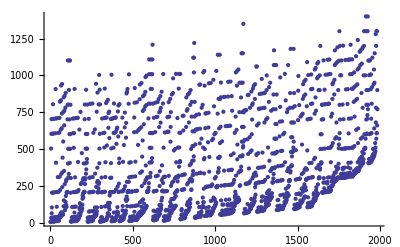

```mathematica
ListPlot[tchs⟦Range[Length[tchs2]],2⟧]
```

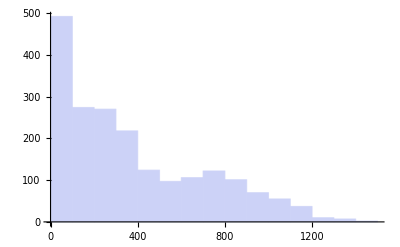

```mathematica
Histogram[tchs2⟦Range[Length[tchs2]],2⟧]
```

## Linguistic Cognates (needs Hebrification)

To implement Rabbi Hirsch's scheme, map back to uppercase for linguistic relatives, then map over to sofetim for gematria.

```mathematica
sofetRules={"K"->"k","M"->"m","N"->"n","P"->"p","C"->"c","כ"->"ך","מ"->"ם","נ"->"ן","פ"->"ף","צ"->"ץ"};
```

```mathematica
unSofetRules=Reverse/@sofetRules
```

{k→K,m→M,n→N,p→P,c→C,ך→כ,ם→מ,ן→נ,ף→פ,ץ→צ}

```mathematica
removeSofetim[s_String]:=StringJoin@@(Characters[s]/.unSofetRules)
```

```mathematica
removeSofetim["BRk"]
```

BRK

```mathematica
removeSofetim["ברך"]
```

ברכ

This will remove sofetim from any word, not just from shoreshim

```mathematica
applySofetim[s_String]:=Module[{cs=Characters[s],l},
l=Length[cs];
cs⟦l⟧=(cs⟦l⟧/.sofetRules);
StringJoin@@cs]
```

```mathematica
applySofetim["BRK"]
```

BRk

```mathematica
applySofetim["ברכ"]
```

ברך

```mathematica
translate[shoresh_String]:=applySofetim[shoresh]/.translations;
```

```mathematica
translate2[shoresh_String]:=applySofetim[shoresh]/.translations2;
```

```mathematica
translate2["חלף"]
```

{exchange,renew,transfer,compensate,braid,work shifts}

```mathematica
xtranslate[sh_String]:=Module[{t=translate[sh]},{sh,t}]
```

```mathematica
ytranslate[sh_String]:=Module[{t=xtranslate[sh]},
If[t⟦1⟧===t⟦2⟧,{t⟦1⟧,{}},t]]
```

```mathematica
translate["BRk"]
```

{bless,power growth,spur prosperity,knee,kneel,cause to kneel}

```mathematica
translate["BRK"]
```

{bless,power growth,spur prosperity,knee,kneel,cause to kneel}

```mathematica
xtranslate["XZR"]
```

{XZR,{return,hold back development,pig,swine,unclean animal}}

```mathematica
ytranslate["XZR"]
```

{XZR,{return,hold back development,pig,swine,unclean animal}}

```mathematica
xtranslate2[sh_String]:=Module[{t=translate2[sh]},{sh,t}]
```

```mathematica
ytranslate2[sh_String]:=Module[{t=xtranslate2[sh]},
If[t⟦1⟧===t⟦2⟧,{t⟦1⟧,{}},t]]
```

```mathematica
xtranslate2["חזר"]
```

{חזר,{return,hold back development,pig,swine,unclean animal}}

```mathematica
ytranslate2["חזר"]
```

{חזר,{return,hold back development,pig,swine,unclean animal}}

```mathematica
xtranslate2["זרך"]
```

{זרך,זרך}

```mathematica
ytranslate2["זרך"]
```

{זרך,{}}

```mathematica
compgem[shoresh_String]:=Module[{g,w},
g=gem[shoresh];
w=allShoreshim⟦g⟧;
{g,Map[xtranslate,w]}]
```

```mathematica
compgem[g_Integer]:=Module[{w},
w=allShoreshim⟦g⟧;
{g,Map[xtranslate,w]}]
```

```mathematica
removeUntranslatedPairs[x_List]:=Select[x,
Not[removeSofetim[#⟦1⟧]===removeSofetim[#⟦2⟧]]&]
```

```mathematica
compgemx[c_]:=Module[{k=compgem[c]},
{k⟦1⟧,removeUntranslatedPairs[k⟦2⟧]}]
```

```mathematica
compgem[")BD"]
```

{7,())H | ))H
)BD | {lose completely,disappear,ruin,perish,lose hope of independence,lost item}
)GG | )GG
)DB | {pain,distress}
)H) | )H)
B)D | B)D
BBG | BBG
BGB | BGB
BD) | {fabricate,lie,create untruths}
G)G | G)G
GBB | {curve upward}
GG) | GG)
D)B | {feel pain,grieve}
DB) | {weaken}
H)) | H)))}

```mathematica
compgem["QRB"]
```

{302,())$ | ))$
)$) | )$)
BQR | {ox,distinguishing differences,examine,strive to know,morning}
BRQ | {flash light,brilliant stone,flashing sword}
QBR | {bury,grave}
QRB | {come close,approach,nearing,face off,offer,relative,war,internal organs,within,scorpion}
RBQ | {fatten an animal}
RQB | {moldy,rot,decay}
$)) | $)))}

```mathematica
compgem["BRk"]
```

{702,())n | ))n
BQm | BQm
BRk | {bless,power growth,spur prosperity,knee,kneel,cause to kneel}
B$T | B$T
BT$ | BT$
QBm | QBm
RBk | {soften by cooking,boil lightly}
$BT | {stop work,curtail activity,shabbat,sabbath,eliminate,work-loss compensation,temporary resting place,tragic loss}
$TB | $TB
TB$ | TB$
T$B | T$B)}

```mathematica
compgem["BRK"]
```

{222,(BKR | {force out,firstborn,free productive elements}
BRK | {bless,power growth,spur prosperity,knee,kneel,cause to kneel}
KBR | {empower to remove,sift,winnow,abundant,plentiful,woven cover,pillow covered with wool,already,heretofore,previously,mouse}
KRB | {protecting angel with child's face,divine vehicle,cover}
RBK | {soften by cooking,boil lightly}
RKB | {place astride,ride,guide a horse,carriage,horsemen,cavalry,upper millstone astride a lower one,ledge,projection})}

```mathematica
compgem[16]
```

{16,()HY | )HY
)W+ | )W+
)ZX | )ZX
)XZ | {grasp,take hold of,possess,take hold,settle,percentage,hide,conceal}
)+W | )+W
)YH | {isolate,where,island,solitary jackal,falcon,woe,sorrow,how}
BDY | BDY
BH+ | {compact,densify}
BWX | BWX
BZZ | {divide booty}
BXW | BXW
B+H | {speak}
BYD | BYD
GGY | GGY
GD+ | GD+
GHX | GHX
GWZ | {detach,cut off,mowed meadow}
GZW | GZW
GXH | GXH
G+D | G+D
GYG | GYG
DBY | DBY
DG+ | DG+
DDX | DDX
DHZ | DHZ
DWW | DWW
DZH | DZH
DXD | DXD
D+G | D+G
DYB | DYB
H)Y | H)Y
HB+ | HB+
HGX | HGX
HDZ | HDZ
HHW | HHW
HWH | {exist,become,bring into being}
HZD | HZD
HXG | HXG
H+B | H+B
HY) | HY)
W)+ | W)+
WBX | WBX
WGZ | WGZ
WDW | WDW
WHH | WHH
WWD | WWD
WZG | WZG
WXB | WXB
W+) | W+)
Z)X | Z)X
ZBZ | ZBZ
ZGW | ZGW
ZDH | ZDH
ZHD | ZHD
ZWG | ZWG
ZZB | ZZB
ZX) | ZX)
X)Z | X)Z
XBW | XBW
XGH | {cleft,crevice,break a flat surface,create unevenness}
XDD | {sharpen}
XHG | XHG
XWB | {owe,in debt}
XZ) | XZ)
+)W | +)W
+BH | +BH
+GD | +GD
+DG | +DG
+HB | +HB
+W) | {sweep,broom}
Y)H | {befit}
YBD | YBD
YGG | YGG
YDB | YDB
YH) | YH))}

```mathematica
Length[compgem[16]⟦2⟧]
```

75

```mathematica
compgem[300]
```

{300,(YCR | {compress,form,shape,force,distress,behavioral inclination}
YRC | YRc
KPR | {annul,forgive,pardon,ransom,asphalt,cover,protect,curtain,bribe,tar,pitch,deny,refute,disavow,cease to believe in God}
KRP | KRp
L(R | L(R
LR( | LR(
MSR | {transfer,deliver,tradition}
MRS | MRS
NNR | NNR
NRN | NRn
SMR | {erect,stand upright,shudder,nail}
SRM | SRm
(LR | (LR
(RL | {restrict power,lose control,restrict,unyielding,foreskin,uncircumcised person}
PKR | PKR
PRK | {separate,divide,discriminate,shut off,cover,useless labor,busy work}
CYR | {connect,contracting pain,message,hinge}
CRY | CRY
QQQ | QQQ
RYC | RYc
RKP | RKp
RL( | RL(
RMS | {trample,crush}
RNN | {express emotion,exalt,jubilate,sing exaltedly,show sadness,ostrich,bird making piercing cries}
RSM | RSm
R(L | {quiver,confuse,shake,bewildered,reeling from wine,fluttering veil}
RPK | RPk
RCY | RCY)}

```mathematica
compgem[613]
```

{613,(GYm | GYm
D+m | D+m
HXm | HXm
WZm | WZm
ZWm | ZWm
XHm | XHm
+Dm | +Dm
YGm | YGm)}

```mathematica
compgem2[shoresh_String]:=Module[{g,w},
g=gem2[shoresh];
w=allShoreshim2⟦g⟧;
{g,Map[xtranslate2,w]}]
```

```mathematica
compgem2["אבד"]
```

{7,(אאה | אאה
אבד | {lose completely,disappear,ruin,perish,lose hope of independence,lost item}
אגג | אגג
אדב | {pain,distress}
אהא | אהא
באד | באד
בבג | בבג
בגב | בגב
בדא | {fabricate,lie,create untruths}
גאג | גאג
גבב | {curve upward}
גגא | גגא
דאב | {feel pain,grieve}
דבא | {weaken}
האא | האא)}

```mathematica
compgem2[g_Integer]:=Module[{w},
w=allShoreshim2⟦g⟧;
{g,Map[xtranslate2,w]}]
```

```mathematica
compgem2[7]
```

{7,(אאה | אאה
אבד | {lose completely,disappear,ruin,perish,lose hope of independence,lost item}
אגג | אגג
אדב | {pain,distress}
אהא | אהא
באד | באד
בבג | בבג
בגב | בגב
בדא | {fabricate,lie,create untruths}
גאג | גאג
גבב | {curve upward}
גגא | גגא
דאב | {feel pain,grieve}
דבא | {weaken}
האא | האא)}

```mathematica
compgemx2[c_]:=Module[{k=compgem2[c]},
{k⟦1⟧,removeUntranslatedPairs[k⟦2⟧]}]
```

```mathematica
compgemx2[7]
```

{7,(אבד | {lose completely,disappear,ruin,perish,lose hope of independence,lost item}
אדב | {pain,distress}
בדא | {fabricate,lie,create untruths}
גבב | {curve upward}
דאב | {feel pain,grieve}
דבא | {weaken})}

```mathematica
compgemx2[16]
```

{16,(אחז | {grasp,take hold of,possess,take hold,settle,percentage,hide,conceal}
איה | {isolate,where,island,solitary jackal,falcon,woe,sorrow,how}
בהט | {compact,densify}
בזז | {divide booty}
בטה | {speak}
גוז | {detach,cut off,mowed meadow}
הוה | {exist,become,bring into being}
חגה | {cleft,crevice,break a flat surface,create unevenness}
חדד | {sharpen}
חוב | {owe,in debt}
טוא | {sweep,broom}
יאה | {befit})}

```mathematica
compgemx2[17]
```

{17,(ביה | {distress,feel pain}
גוח | {crawl,move with difficulty,slither,meander}
גזז | {shear,separate,set apart}
דחה | {push,stumble,topple}
הזה | {babble}
זבח | {nourish,slaughter animal,act for a higher purpose}
זהה | {identify,that}
זוד | {premeditate,scheme,simmer,boil,pottage,sin willingly}
חדה | {rejoice}
חוג | {holiday,encircle,observe cyclical holidays}
טוב | {advance benefit to mankind,health,happiness,good,improve,renew,restore}
יהב | {give,provide})}

## Vector-Space Interpretations

Suppose a shoresh were a vector, with each letter representing the component of the vector. Map the letters to [-10.5,10.5] (becaue we don't want a zero!), and ignore sofetim for now (assuming they don't have semantic content). An alternative idea is to include sofetim.

```mathematica
Clear[א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת]
```

```mathematica
InputForm@SymbolName[א]
```

"א"

```mathematica
letterVectorRules=MapThread[Rule,{SymbolName/@{א,ב,ג,ד,ה,ו,ז,ח,ט,י,כ,ל,מ,נ,ס,ע,פ,צ,ק,ר,ש,ת},Range[-21/2,21/2]*2}]
```

{א→-21,ב→-19,ג→-17,ד→-15,ה→-13,ו→-11,ז→-9,ח→-7,ט→-5,י→-3,כ→-1,ל→1,מ→3,נ→5,ס→7,ע→9,פ→11,צ→13,ק→15,ר→17,ש→19,ת→21}

This one should have the smallest magnitude.

```mathematica
translate2["כלל"]
```

{perfect,sustain,completion,all,daughter-in-law complete family}

Now rewrite a shoresh as a numerical vector:

```mathematica
shoreshVector[s_]:=Module[{cs, x,y,z},
cs=Characters[removeSofetim@s];
x=cs⟦1⟧;y=cs⟦2⟧;z=cs⟦3⟧; (* gets them in right-to-left order no problem *)
{{x,y,z},{x,y,z}/.letterVectorRules}]
```

```mathematica
shoreshVector["אבד"]
```

(א | ב | ד
-21 | -19 | -15)

```mathematica
shoreshVector["אאא"]
```

(א | א | א
-21 | -21 | -21)

Shoreshim with Hirschian Translations

```mathematica
translations2⟦1234⟧
```

סעף→{branch out,extend,lop branches,cleft,differnt trends of thought}

```mathematica
cleanShoreshByNumber[n_]:=removeSofetim@translations2⟦n,1⟧
```

```mathematica
cleanShoreshByNumber[1234]//applySofetim
```

סעף

There are this many

```mathematica
Length@translations2
```

1985

```mathematica
cleanShoreshVectorByNumber[n_]:=shoreshVector[cleanShoreshByNumber[n]]⟦2⟧
```

```mathematica
cleanShoreshVectorByNumber[1234]
```

{7,9,11}

```mathematica
applySofetim/@cleanShoreshByNumber/@Range[1,30]
```

{אבב,אבד,אבה,אבך,אבל,אבם,אבן,אבס,אבק,אבר,אגד,אגז,אגל,אגם,אגן,אגף,אגר,אדב,אדם,אדן,אדר,אהב,אהה,אהל,אוב,אוד,אוה,אוח,אול,אום}

Plot the shoreshim that have Hirschian translations.

```mathematica
ListPointPlot3D[cleanShoreshVectorByNumber/@Range[1,1985],
AxesLabel->{"פ","ע","ל"},
BoxRatios->{1,1,1}]
```

-Graphics3D-

In this scheme, each component is a number between -21/44 and 21/44, inclusive.

Examinations

Looks like there aren't many shoreshim with ו"ל

```mathematica
Select[translations2,
Function[t,Characters[t⟦1⟧]⟦3⟧=="ו"]]
```

{זיו→{brighten},תאו→{crave,desire,yearn for,long for}}

Algebra on Shoreshim

Find the index of a shoresh in the Hirschian list:

```mathematica
hirschianShoreshim=removeSofetim/@First/@translations2;
```

```mathematica
shoreshIndex[s_]:=Module[{p=Position[hirschianShoreshim,removeSofetim@s]},
If[p=={},0,p⟦1,1⟧]]
```

```mathematica
shoreshIndex/@{"נגע","אים","פגע","אאא"}
```

{1051,54,1379,0}

Given a shoresh, find the other shoreshim almost orthogonal or almost parallel to it

```mathematica
v[s_]:=shoreshVector[s]⟦2⟧;
dot[s1_,s2_]:=v[s1].v[s2];
dotLess[s1_,s2_,lim_]:=Abs@dot[s1,s2]<=lim;
dotMore[s1_,s2_,lim_]:=Abs@dot[s1,s2]>=lim;
```

The square magnitudes range from 3/(44*44) to 1323/(44*44)

```mathematica
Union@(Sort@(dot[#,#]&/@hirschianShoreshim))
```

{3,11,19,27,35,43,51,59,67,75,83,91,99,107,115,123,131,139,147,155,163,171,179,187,195,203,211,219,227,235,243,251,259,267,275,283,291,299,307,315,323,331,339,347,355,363,371,379,387,395,403,411,419,427,435,443,451,459,467,475,483,491,499,507,515,523,531,539,547,555,563,571,579,587,595,603,611,619,627,635,643,651,659,667,675,683,691,699,707,715,723,731,739,747,755,771,779,787,803,811,819,827,835,843,851,867,875,883,891,899,907,923,931,939,947,955,963,971,1003,1011,1019,1027,1051,1083,1091,1107,1163,1171,1243,1323}

Here's a list of all the shoreshim AND their vector magnitudes

```mathematica
Shallow[
hirschianVectors=({applySofetim[#⟦1⟧],#⟦2⟧}&/@Sort[MapThread[List,{hirschianShoreshim,dot[#,#]&/@hirschianShoreshim}],
#1⟦2⟧<#2⟦2⟧&])]
```

{{כלל,3},{מלל,11},{מלך,11},{מכך,11},{למך,11},{כלם,11},{ילל,11},{יכל,11},{ימך,19},{נכל,27},«1975»}

Here's the distribution of vector magnitudes

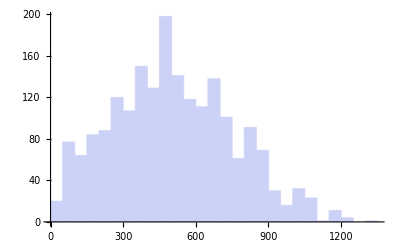

```mathematica
Histogram[#⟦2⟧&/@hirschianVectors]
```

```mathematica
findAlmostOrthogonalShoreshim[s_,lim_]:=Module[{
ss2},
ss2=Select[hirschianShoreshim,dotLess[s,#,lim]&];
ss2]
```

```mathematica
findAlmostParallelShoreshim[s_,lim_]:=Module[{
ss2},
ss2=Select[hirschianShoreshim,dotMore[s,#,lim]&];
ss2]
```

```mathematica
translate2["הלך"]
```

{walk,progress toward a goal,come,process,way,manner}

```mathematica
shoreshVector["הלך"]
```

(ה | ל | כ
-13 | 1 | -1)

```mathematica
hdots[s_]:=dot[s,#]&/@hirschianShoreshim
```

```mathematica
Shallow@MapThread[List,{hdots["הלך"],hirschianShoreshim}]
```

{{273,אבב},{269,אבד},{267,אבה},{255,אבכ},{253,אבל},{251,אבמ},{249,אבנ},{247,אבס},{239,אבק},{237,אבר},«1975»}

```mathematica
Union@Sort@hdots["הלך"]
```

{-311,-303,-301,-299,-297,-295,-293,-289,-287,-285,-283,-281,-279,-277,-275,-273,-271,-269,-267,-265,-263,-261,-259,-257,-255,-253,-251,-249,-247,-245,-243,-241,-239,-237,-235,-233,-231,-229,-227,-225,-223,-221,-219,-217,-215,-213,-211,-209,-207,-205,-203,-201,-199,-197,-195,-193,-191,-189,-187,-185,-183,-181,-179,-177,-175,-173,-171,-169,-167,-165,-163,-161,-159,-157,-155,-153,-151,-149,-147,-145,-143,-141,-139,-137,-135,-133,-131,-129,-127,-125,-123,-121,-119,-117,-115,-113,-111,-109,-107,-105,-103,-101,-99,-97,-95,-93,-91,-89,-87,-85,-83,-81,-79,-77,-75,-73,-71,-69,-67,-65,-63,-61,-59,-57,-55,-53,-51,-49,-47,-45,-43,-41,-39,-37,-35,-33,-31,-29,-27,-25,-23,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255,257,259,261,263,265,267,269,271,273,275,277,279,281,283,285,287,289,291,293,297,299,301,303,305,307,309}

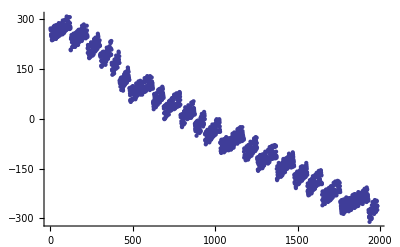

```mathematica
ListPlot[hdots["הלך"]]
```

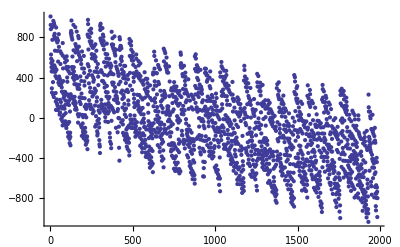

```mathematica
ListPlot[hdots["בוא"]]
```

```mathematica
(dot["הלך",#]&/@Select[hirschianShoreshim,dotLess["הלך",#,1]&])
```

{1,-1,1,1,-1,-1,1,1,1,1,-1,-1,-1}

```mathematica
findAlmostOrthogonalShoreshim["הלך",1]
```

{יאר,יאש,יבש,כול,כומ,כמר,כנר,לכד,לעט,לשנ,לתע,מרא,מתג}

```mathematica
findAlmostParallelShoreshim["הלך",300]
```

{אקה,ארב,ארג,ארה,אשד,אשה,אתה,תאר,תור,תוש,תחת}

```mathematica
findFurthest[s_,n_]:=Module[{os=findAlmostOrthogonalShoreshim[s,n]},
MapThread[List,{applySofetim/@os,dot[s,#]&/@os,translate2/@os}]]
```

```mathematica
findFurthest["הלך",1]
```

(יאר | 1 | {irrigate,collect water,river}
יאש | -1 | {despair}
יבש | 1 | {firm up,dry up,lose hope}
כול | 1 | {contain a measured quantity,measure,vessel,enclosure}
כום | -1 | {venerate,constellation as a deity}
כמר | -1 | {excite deep emotions,singe,blacken,catch in a net}
כנר | 1 | {harp,lyre,string instrument,emit sounds}
לכד | 1 | {seize,capture,set traps}
לעט | 1 | {swallow greedily,gulp down}
לשן | 1 | {tongue,language}
לתע | -1 | {destroy,uproot,deadly fangs}
מרא | -1 | {expand,enlarge,unfold wings in flight,well-fed animal,crop of animal holding food}
מתג | -1 | {control,direct,bridle})

```mathematica
findClosest[s_,n_]:=Module[{os=findAlmostParallelShoreshim[s,n]},
MapThread[List,{applySofetim/@os,dot[s,#]&/@os,translate2/@os}]]
```

```mathematica
findClosest["הלך",300]
```

(אקה | 301 | {wild,wild goat}
ארב | 309 | {restrain urge to penetrate,lie in wait,barrier,windows of heaven,lair,artifice,lattice,sluice}
ארג | 307 | {weave,loom,red-colored thread,join parallel threads}
ארה | 303 | {contain,pluck,barn stall,stable,powerful leaders,lion,take and hold}
אשד | 307 | {outflow,slope,pour out of}
אשה | 305 | {create material,be,exist,fire-shaped material,supporting pillar}
אתה | 307 | {come to someone,entrance}
תאר | -311 | {harmonize,draw in outline,circle,harmonious form and shape of limbs}
תור | -301 | {search for separate items,explore,search,seek knowledge,arrange,plan,migrating turtledove,forage for grass,stringed jewelry,appointed time}
תוש | -303 | {romp,he-goat}
תחת | -301 | {place below,underneath,in place of,instead of,in return for,lower level})

```mathematica
dot["בוא","בוא"]
```

923

```mathematica
translate2["בוא"]
```

{come to attractive place,harvest}

```mathematica
findFurthest["בוא",1]
```

(הצן | -1 | {arm,equip}
טמם | -1 | {dull,fill up,close off}
מום | 1 | {fault,disable}
עצד | 1 | {strike down,smithy,axe}
ערג | -1 | {thirst for water,irrigate}
פתא | 1 | {surprise,sudden,unaware})

```mathematica
findClosest["בוא",950]
```

(אבב | 1007 | {ripen,absorb nutrients greedily,stalk,springtime}
אדב | 963 | {pain,distress}
בדא | 967 | {fabricate,lie,create untruths}
גבא | 973 | {concentrate fluids,pool}
רתת | -995 | {tremble,shake}
שרת | -989 | {free from labor,give personal service,serve,attendant,s:serve,s:serving pot}
שתת | -1033 | {set out,s:threatening power,s:exert power}
תרש | -985 | {search,aquamarine stone,trading port shipping mined silver})

```mathematica
dot["בוא","אבב"]
```

1007

Aryeh's Question

Which letters and which gematria are most likely to yield theoretical shoreshim, and which to yield shoreshim with translations?

Begin with the distribution of all shoreshim: how many shoreshim are there for each gematria? Zip this with the gematriot.

```mathematica
allGematriot=MapThread[List,{Range[1700],Length/@allShoreshim}];
```

Remove gematriot with zero shoreshim:

```mathematica
nonEmptyGematriot=Select[allGematriot,#⟦2⟧!=0&];
```

How many of these are there?

```mathematica
Length@allGematriot
```

1700

Check for errors:

```mathematica
Plus@@(#⟦2⟧&/@allGematriot)
```

13068

```mathematica
Length@nonEmptyGematriot
```

1077

```mathematica
Plus@@(#⟦2⟧&/@nonEmptyGematriot)
```

13068

Sort with respect to the second element, which is the count:

```mathematica
gem2shor=Sort[nonEmptyGematriot,((#1⟦2⟧)>(#2⟦2⟧))&];
```

Here are the top 20 gematriot:

```mathematica
Take[gem2shor,20]
```

(210 | 82
170 | 75
160 | 75
17 | 75
16 | 75
180 | 73
150 | 73
18 | 73
15 | 73
110 | 72
190 | 69
140 | 69
19 | 69
14 | 69
200 | 63
130 | 63
100 | 63
20 | 63
13 | 63
410 | 60)

Figure out which shoreshim generate translations:

```mathematica
findTrans[n_Integer]:=
Select[ytranslate/@allShoreshim⟦n⟧,#⟦2⟧≠{}&]
```

```mathematica
gem2trans=Sort[
Select[
Map[{#,Length@findTrans[#]}&,Range[1700]],
#⟦2⟧≠0&],
((#1⟦2⟧)>(#2⟦2⟧))&];
```

```mathematica
Length@gem2trans
```

668

```mathematica
Print[Take[gem2shor,25],Take[gem2trans,25]]
```

(210 | 82
170 | 75
160 | 75
17 | 75
16 | 75
180 | 73
150 | 73
18 | 73
15 | 73
110 | 72
190 | 69
140 | 69
19 | 69
14 | 69
200 | 63
130 | 63
100 | 63
20 | 63
13 | 63
410 | 60
310 | 57
120 | 55
90 | 55
21 | 55
12 | 55)(210 | 22
310 | 16
160 | 16
370 | 15
170 | 15
13 | 15
360 | 13
190 | 13
58 | 13
350 | 12
200 | 12
150 | 12
148 | 12
130 | 12
60 | 12
17 | 12
16 | 12
470 | 11
340 | 11
208 | 11
207 | 11
120 | 11
103 | 11
75 | 11
57 | 11)

```mathematica
compgemx[210]
```

{210,()+R | {close off,left-handed}
BXR | {choose from many,prefer,elect,vote for,select,elite,youth?}
BRX | {flee,evade,exit quickly,become independent}
GZR | {pieces,cut into pieces,divide,section,decree}
GRZ | {cut off,separate,exclude?}
DWR | {live in same generation,link together,history}
HRH | {conceive a child,become pregnant,implant and absorb seed,teach}
XBR | {friend,join for positive purpose,partners,intimate union,charm,enchant}
XRB | {sword,dry land,drought,parch,lose vitality,ruins}
LCC | {deride,cite parables and allegories}
NSQ | {ascend}
N(C | {penetrate,bristly thorn}
NPP | {wave}
S(P | {branch out,extend,lop branches,cleft,differnt trends of thought}
(MQ | {deepen,profound,depths,basin,valley}
PCM | {cleave,sever,rend,sunder}
CN( | {discreet,act reservedly,modest,humble}
C(N | {dismantle}
RGZ | {tremble due to fear,fearful,angry,box,container}
RHH | {fear}
RWD | {humble,homeless}
RXB | {enlarge,widen,at ease,street,open space,breadth,width})}

```mathematica
compgemx[160]
```

{160,(YNQ | {suck,breast feed,osmosis,nurse,wet nurse}
Y(P | {ascend,strive,faint and weary}
YP( | {radiate,emerge from darkness,dawn}
KSP | {silver,money,longing}
KPS | {connect,fasten}
MLC | {sweeten}
MN( | {withhold,refuse}
MSS | {melt,dissolve,devastate,depend,decay}
N(M | {please,attract,physically beautiful,in state of bliss}
NPL | {fall,drop down,descend,drop in strange place,apportion,giant,discard,ruin,stillborn}
SL( | {raise tall,elevated rock,long-necked locust}
SNN | {protrude}
(YP | {tire,exhaust,wear out,dark}
(LS | {rejoice}
CLM | {image,cover,complete form,stately appearance}
QLL | {diminish substance,lessen material things,curse,abate,shake,run swiftly,polish,light in weight,stick,rod})}

```mathematica
compgemx["RGL"]
```

{233,(GRL | {allocate,lot,chance,portion,share}
RGL | {learn step-by-step,foot,spy,footpad,pace,in accord with current activity,pilgrim festival,occasion,occurrence,raised foot,at the foot of,follower})}

## Consistency Checks

```mathematica
lt[sh1_String,sh2_String]:=Module[
{c1=Characters[removeSofetim[sh1]],
c2=Characters[removeSofetim[sh2]]},
(gem[c1⟦1⟧]<gem[c2⟦1⟧]) ||
((gem[c1⟦1⟧]===gem[c2⟦1⟧])
&&(gem[c1⟦2⟧]<gem[c2⟦2⟧]))||
((gem[c1⟦1⟧]===gem[c2⟦1⟧])
&&(gem[c1⟦2⟧]===gem[c2⟦2⟧])
&&(gem[c1⟦3⟧]<gem[c2⟦3⟧]))]
```

The following command revealed likely misspellings in the vicinities of BRZ, GM(, X+R, Y$$, L(n, LPT, LQT, M$$, CXX, $Pn. After corrections, this command yields null.

```mathematica
testn[n_Integer]:=Module[
{shs=First/@translations,ls,rs,ts,as},
ls=Drop[shs,-n];rs=Drop[shs,n];
ts=MapThread[lt,{ls,rs}];
as=MapThread[List,{ls,ts}];
Select[as,#⟦2⟧==False&]]
```

```mathematica
(* testn/@Range[50] *)
```

## Cycling Roots

```mathematica
otayot
```

{),B,G,D,H,W,Z,X,+,Y,K,L,M,N,S,(,P,C,Q,R,$,T,k,m,n,p,c}

```mathematica
notayot=Take[otayot,22]
```

{),B,G,D,H,W,Z,X,+,Y,K,L,M,N,S,(,P,C,Q,R,$,T}

```mathematica
cycle[l_List]:=Flatten[{Drop[l,1],First[l]},1]
```

```mathematica
cycle[notayot]
```

{B,G,D,H,W,Z,X,+,Y,K,L,M,N,S,(,P,C,Q,R,$,T,)}

```mathematica
zip2rules[l_List,m_List]:=MapThread[Rule,{l,m}]
```

```mathematica
bumpRules=zip2rules[notayot,cycle[notayot]]
```

{)→B,B→G,G→D,D→H,H→W,W→Z,Z→X,X→+,+→Y,Y→K,K→L,L→M,M→N,N→S,S→(,(→P,P→C,C→Q,Q→R,R→$,$→T,T→)}

```mathematica
pmubRules=Reverse/@bumpRules
```

{B→),G→B,D→G,H→D,W→H,Z→W,X→Z,+→X,Y→+,K→Y,L→K,M→L,N→M,S→N,(→S,P→(,C→P,Q→C,R→Q,$→R,T→$,)→T}

```mathematica
bump[sh_String]:=applySofetim[StringJoin@@(Characters[removeSofetim[sh]]/.bumpRules)]
```

```mathematica
"ZKR"/.translations
```

{remember,male,historian}

```mathematica
bump["ZKR"]
```

XL$

```mathematica
bump["ZKR"]/.translations
```

{weaken,defeat}

```mathematica
pmub[sh_String]:=applySofetim[StringJoin@@(Characters[removeSofetim[sh]]/.pmubRules)]
```

```mathematica
"NQB"/.translations
```

{perforate,set firmly,penetrate,make a hole,decide,name,particularize,female,designated one,hammer,awl,adze}

```mathematica
pmub["NQB"]
```

MC)

```mathematica
compgemx["MC)"]
```

{131,()MC | {strengthen,obstinate,strong color,force,secure}
)NP | {nostril,nose,breathe,snort,enrage,express inner feelings of anger}
)PN | {create purposefully,stone wheel,purpose}
MC) | {find deliberately,bring out,witness,verify,face,meeting,present,suffice}
N)P | {commit adultery,turn from one another}
CM) | {thirst,drought}
QL) | {parch,dry})}

```mathematica
bump["NQB"]
```

SRG

```mathematica
pmub["NQB"]/.translations
```

{find deliberately,bring out,witness,verify,face,meeting,present,suffice}

```mathematica
rev[sh_String]:=
applySofetim[
StringJoin@@(
Reverse[
Characters[
removeSofetim[sh]]])]
```

```mathematica
")DB"/.translations
```

{pain,distress}

```mathematica
rev[")DB"]
```

BD)

```mathematica
rev[")DB"]/.translations
```

{fabricate,lie,create untruths}

## Homorganic Consonant Categories

```mathematica
gutturals={"X",")","H","("};
```

```mathematica
palatals={"Q","K","Y","G"};
```

```mathematica
dentals={"N","L","+","T","D"};
```

```mathematica
labials={"M","P","B","W"};
```

```mathematica
sibilants={"C","$","S","Z","R"};
```

To convert any shoresh to another by substituting chars from the homorganic categories, substitution rules for every permutation.

```mathematica
isIdent[r_Rule]:=r⟦1⟧===r⟦2⟧
```

```mathematica
isntIdent=Not[isIdent[#]]&;
```

```mathematica
allTrans[g_List]:=
Select[Union@@{zip2rules[g,cycle[g]]
,zip2rules[g,cycle[cycle[g]]]
,zip2rules[g,cycle[cycle[cycle[g]]]]
,zip2rules[g,cycle[cycle[cycle[cycle[g]]]]]},isntIdent]
```

```mathematica
(agis=allTrans[gutturals])//StandardForm
```

{(→),(→H,(→X,)→(,)→H,)→X,H→(,H→),H→X,X→(,X→),X→H}

```mathematica
(apis=allTrans[palatals])//StandardForm
```

{G→K,G→Q,G→Y,K→G,K→Q,K→Y,Q→G,Q→K,Q→Y,Y→G,Y→K,Y→Q}

```mathematica
(adis=allTrans[dentals])//StandardForm
```

{+→D,+→L,+→N,+→T,D→+,D→L,D→N,D→T,L→+,L→D,L→N,L→T,N→+,N→D,N→L,N→T,T→+,T→D,T→L,T→N}

```mathematica
(alis=allTrans[labials])//StandardForm
```

{B→M,B→P,B→W,M→B,M→P,M→W,P→B,P→M,P→W,W→B,W→M,W→P}

```mathematica
(asis=allTrans[sibilants])//StandardForm
```

{C→R,C→S,C→Z,C→$,R→C,R→S,R→Z,R→$,S→C,S→R,S→Z,S→$,Z→C,Z→R,Z→S,Z→$,$→C,$→R,$→S,$→Z}

```mathematica
(atis=Join[agis,apis,adis,alis,asis])//StandardForm
```

{(→),(→H,(→X,)→(,)→H,)→X,H→(,H→),H→X,X→(,X→),X→H,G→K,G→Q,G→Y,K→G,K→Q,K→Y,Q→G,Q→K,Q→Y,Y→G,Y→K,Y→Q,+→D,+→L,+→N,+→T,D→+,D→L,D→N,D→T,L→+,L→D,L→N,L→T,N→+,N→D,N→L,N→T,T→+,T→D,T→L,T→N,B→M,B→P,B→W,M→B,M→P,M→W,P→B,P→M,P→W,W→B,W→M,W→P,C→R,C→S,C→Z,C→$,R→C,R→S,R→Z,R→$,S→C,S→R,S→Z,S→$,Z→C,Z→R,Z→S,Z→$,$→C,$→R,$→S,$→Z}

```mathematica
Length@atis
```

76

```mathematica
homorg[c_]:=Union@Map[c/.#&,atis]
```

```mathematica
allHomorgs[sh_String]:=
Module[{ms=Map[homorg,Characters[removeSofetim[sh]]]},
Map[applySofetim,
Map[StringJoin,
Flatten[Outer[List,ms⟦1⟧,ms⟦2⟧,ms⟦3⟧],2]]]]
```

```mathematica
allHomorgs["BRk"]//StandardForm
```

{BCG,BCk,BCQ,BCY,BRG,BRk,BRQ,BRY,BSG,BSk,BSQ,BSY,BZG,BZk,BZQ,BZY,B$G,B$k,B$Q,B$Y,MCG,MCk,MCQ,MCY,MRG,MRk,MRQ,MRY,MSG,MSk,MSQ,MSY,MZG,MZk,MZQ,MZY,M$G,M$k,M$Q,M$Y,PCG,PCk,PCQ,PCY,PRG,PRk,PRQ,PRY,PSG,PSk,PSQ,PSY,PZG,PZk,PZQ,PZY,P$G,P$k,P$Q,P$Y,WCG,WCk,WCQ,WCY,WRG,WRk,WRQ,WRY,WSG,WSk,WSQ,WSY,WZG,WZk,WZQ,WZY,W$G,W$k,W$Q,W$Y}

```mathematica
compHomorg[r_String]:=removeUntranslatedPairs[Map[xtranslate,allHomorgs[r]]]
```

```mathematica
compHomorg["RGL"]
```

(CQL | {cover,protect,bag}
RGL | {learn step-by-step,foot,spy,footpad,pace,in accord with current activity,pilgrim festival,occasion,occurrence,raised foot,at the foot of,follower}
RGn | {quarrel,encourage complaint,contrary}
RKL | {peddle,merchandising,slander,bear gossip,goods,merchandise}
RQD | {dance,skip,frolic}
SGD | {bow down}
SGL | {elect,exclusive,unique,treasure,rare object}
SGn | {act officially,deputize,rule}
SKL | {absorb unreliable knowledge,foolish}
SKn | {attend,direct attention,care for,store,parsimonious,benefit,pay attention,endanger}
SKT | {pay attention}
SQL | {remove,cast stones}
$GL | {acquire mate,copulate,woman}
$KL | {lose,bereft,bereave,miscarry,bereft of children,kidnap,picked vines,s:understand,s:act rationally,s:mentor,s:succeed,s:teach ode,s:teach}
$Kn | {dwell,reside with others,live temporarily in one place,live undisturbed,present,connect with the divine,friendly neighbor,tabernacle}
$KT | {s:bow down}
$Q+ | {quiet,undisturbed,rest,calm}
$QD | {direct to,startled into energetic thought,concentrated watching,urge forward,almond,first fruit after winter,almond-shaped,s:press heavily,s:press down}
$QL | {weigh out,builder's plumb,weigh out for payment,weighted coins,weight,shekel})

```mathematica
compHomorg["BRk"]
```

(BCQ | {swell,blister,rising dough}
BRk | {bless,power growth,spur prosperity,knee,kneel,cause to kneel}
BRQ | {flash light,brilliant stone,flashing sword}
BZQ | {spread lightning}
MRG | {penetrate,thresh out seeds}
MRk | {boil away}
MRQ | {penetrate,scour,clean,polish,soup,gravy,skin treatment}
MSk | {mix,flow together}
MZG | {mix}
M$k | {pull in,draw in,defer,remove,conclude,measure,prolong,march,draw the bow,Me$e#@ son of YeFeT}
M$Q | {rustle in the wind}
PRk | {separate,divide,discriminate,shut off,cover,useless labor,busy work}
PRQ | {divide,disconnect,forcibly remove,take apart,joint of neck,crossroad,limb}
PSG | {raise to prominence,elevate}
P$Q | {s:stretch,s:open})

```mathematica
compHomorg["MC)"]
```

(BC( | {complete,purpose,conclude,finish,take advantage,break into pieces}
BC) | {muddy}
BCH | {muddy}
BR) | {create,open,actualize,clear an opening,cut}
BRH | {rejuvenate,restore health,feed,field growing food}
BRX | {flee,evade,exit quickly,become independent}
BZ) | {cut,separate}
BZH | {scorn}
MC) | {find deliberately,bring out,witness,verify,face,meeting,present,suffice}
MCH | {suck,squeeze}
MR) | {expand,enlarge,unfold wings in flight,well-fed animal,crop of animal holding food}
MRH | {oppose,counter,disobey,rebel,shave,bitter,inspite of}
MRX | {smear}
MSH | {melt away,disintegrate,vanish}
MZH | {thin,lose essence,waste away}
MZX | {gird,hold in}
M$H | {draw out of water}
M$X | {separate out,smear insoluble material}
PC( | {wound,harm}
PCH | {open,force open,free,save,rescue,pledge at time of loss,speak,open mouth to speak,open mouth to eat}
PCX | {open up,break,burst forth,express emotion}
PR( | {loosen,disarrange,ease pressure,uncover,lose control,distance,absolute monarch,wild hair,locks,wild insects}
PR) | {free of control,unconstrained,uninhibited,wild ass}
PRH | {produce,produce progeny,flourish,fruit,liberated seed,enclosed sedan,three-year old bull}
PRX | {blossom,grow,flower,erupt,fly,youth,young bird}
PSX | {skip,walk unevenly,step haltingly,pass over,lame,offering for holiday}
P$( | {transgress,misuse a relationship,misuse another's possession,sin,crime,s:step energetically,s:step,s:stride,s:groin}
P$H | {s:spread}
P$X | {split open,pull apart})

## Bere'sheet

```mathematica
"X$k"/.translations
```

{darken,dungeon,obscure,s:reduce,s:withold,s:stop}

```mathematica
gem["X$k"]
```

808

```mathematica
compgem[808]
```

{808,()Zp | )Zp
BWp | BWp
GHp | GHp
DDp | DDp
HGp | HGp
WBp | WBp
Z)p | Z)p
XQn | XQn
XRm | {segregate,nettin,sickle,flattened nose}
X$k | {darken,dungeon,obscure,s:reduce,s:withold,s:stop}
XTT | {broken emotionally,shatter,panicked,dread,terror,frightened}
QXn | QXn
RXm | {protect from harm,show maternal mercy,empathize,love childishly,womb,captive women,protecting bird}
$Xk | $Xk
TXT | {place below,underneath,in place of,instead of,in return for,lower level}
TTX | TTX)}

```mathematica
compgemx[808]
```

{808,(XRm | {segregate,nettin,sickle,flattened nose}
X$k | {darken,dungeon,obscure,s:reduce,s:withold,s:stop}
XTT | {broken emotionally,shatter,panicked,dread,terror,frightened}
RXm | {protect from harm,show maternal mercy,empathize,love childishly,womb,captive women,protecting bird}
TXT | {place below,underneath,in place of,instead of,in return for,lower level})}

```mathematica
"RXp"/.translations
```

{flutter,hover}

```mathematica
compgem["RXp"]
```

{1008,(XQc | XQc
XRp | {taunt,make vulnerable,disgrace,shame,betrothe,jeopardize,blaspheme,winter}
X$n | {shield,protect chest,brest pocket,pouch}
XTm | {seal,sign,subscribe,guard,witness}
QXc | QXc
RXp | {flutter,hover}
$Xn | {inflame,have imbalance of natural elements,inflamed boil,abcess}
TXm | TXm)}

```mathematica
gem[")LHYM"]
```

86

```mathematica
compgem[646]
```

{646,(WMm | WMm
MWm | {fault,disable})}

```mathematica
"D$)"/.translations
```

{grow,sprout}

```mathematica
"($B"/.translations
```

{s:grow independently,s:herb,s:plant}

```mathematica
"($H"/.translations
```

{s:make,s:create,s:form,s:do,s:press,s:observe,s:cause to grow,s:develop,s:crush,s:squeeze}

```mathematica
"MWn"/.translations
```

{define species,species,picture}

```mathematica
"RQ("/.translations
```

{crush,get down,forcibly flatten,establish firmly,overlay,lower heaven,flat ground}

```mathematica
"BDL"/.translations
```

{separate for positive purpose,crystallize}

```mathematica
"LWL"/.translations
```

{blend together,night,time when everything is blended}

```mathematica
")TH"/.translations
```

{come to someone,entrance}

```mathematica
")TT"/.translations
```

{cut,penetrate,sign,distinguishing emblem,you,with}

```mathematica
"M(D"/.translations
```

{stumble,tremble}

```mathematica
"Y(D"/.translations
```

{arrange,set specifics,meet together,set a time,set an appointment,arrange a marriage,community,criminal court,ranks of soldiers,meeting place,festival,season}

```mathematica
"M)R"/.translations
```

{perforate,destroy,malignant,hurt}

```mathematica
")WR"/.translations
```

{light,illuminate,shine,enlighten,blind,fiery furnace,sparkling eye,bearer of light,land of light,vegetable to improve vision}

```mathematica
"M$L"/.translations
```

{rule,determine role,designate character,historian,parable,pun,joke,exemplar,type,archetype}

```mathematica
"KKB"/.translations
```

KKB

```mathematica
"KBB"/.translations
```

{orbit,stars,signpost for human behavior}

```mathematica
"$Rc"/.translations
```

{swarm,flock,creeping things,take on different forms}

```mathematica
"NP$"/.translations
```

{rest,return to spiritual repose,soul,individual,determination,living person}

```mathematica
"XHY"/.translations
```

XHY

```mathematica
"(Pp"/.translations
```

{flutter,eyelid,fly,look quickly}

```mathematica
"(Wp"/.translations
```

{lift into air,fly,fill with air,bird,exhaustion from exertion,tired}

```mathematica
compgem["(Pp"]
```

{950,(YMc | YMc
KLc | KLc
LKc | LKc
MYc | MYc
NQp | {chop off,strike,bandage}
NRn | NRn
N$m | {breathe,inhale,move air,mole,impure creeper}
NTk | {dissolve,pour}
SCp | SCp
(Pp | {flutter,eyelid,fly,look quickly}
P(p | P(p
CSp | CSp
QNp | QNp
RNn | {express emotion,exalt,jubilate,sing exaltedly,show sadness,ostrich,bird making piercing cries}
$Nm | $Nm
TNk | {pliant,soft rim of ear})}

```mathematica
compgem["(Wp"]
```

{876,(W(p | W(p
(Wp | {lift into air,fly,fill with air,bird,exhaustion from exertion,tired})}

```mathematica
"RM$"/.translations
```

{s:tread softly,s:walk lightly,s:crawl,s:creeping thing}

```mathematica
"TNn"/.translations
```

{emit sounds of calmness,console,express,quiet lair}

```mathematica
"NWn"/.translations
```

NWn

```mathematica
"HTNYNM" (* Sea monsters ??? *)
```

HTNYNM

```mathematica
"$Rc"/.translations
```

{swarm,flock,creeping things,take on different forms}

```mathematica
"KNp"/.translations
```

{conceal,feathered wing,covering,corner,edge}

```mathematica
"ML)"/.translations
```

{fill,fulfill duties,full,have full value,satisfy,equip,confer authority,have everything,gather,set,insert,replenish,hold produced in a field}

```mathematica
"YC)"/.translations
```

{exit,come out,go out to the public,results,be an exception,fulfill obligation,lose temper,go crazy,be published,export,spend money,be exempted,remedies,source,excrement}

```mathematica
"CLm"/.translations
```

{image,cover,complete form,stately appearance}

```mathematica
"DMH"/.translations
```

{likeness,resemble,silence,blood}

```mathematica
"RDH"/.translations
```

{dominate,humble to another's control,exert excessive power,overcome,separate}

```mathematica
"BR)"/.translations
```

{create,open,actualize,clear an opening,cut}

```mathematica
"NQB"/.translations
```

{perforate,set firmly,penetrate,make a hole,decide,name,particularize,female,designated one,hammer,awl,adze}

```mathematica
"KB$"/.translations
```

{subdue,subject forcibly,master,spider,s:white sheep,s:whiten}

```mathematica
"YRQ"/.translations
```

{cast down,spit,green,jaundice}

```mathematica
"CB)"/.translations
```

{mobilize,add to assembled body,gather multitude,assemble,join in public service,form an army,obligate a group to work a set time,organize soldiers,gazelle,part of herd,hosts}

```mathematica
"L)k"/.translations
```

{serve,work,complete a goal,messenger,angel,divine decree}

```mathematica
"$YX"/.translations
```

{s:grow,s:develop,s:pray,s:deliberate,s:spiritual growth,s:low-growing shrub,s:bush}

```mathematica
"$DH"/.translations
```

{produce nourishment,productive,breast,field,vineyard,s:produce food,s:sustain,s:country Gn.14.7}

```mathematica
"+Rm"/.translations
```

{anticipate,yet}

```mathematica
"($B"/.translations
```

{s:grow independently,s:herb,s:plant}

```mathematica
"CMX"/.translations
```

{grow,expand}

```mathematica
"M+R"/.translations
```

{descend from height,rain,cause rain,send down}

```mathematica
")WD"/.translations
```

{effect results,set into motion,lever,reason for,account of,imminent calamity,vapor,mist,very}

```mathematica
"$QH"/.translations
```

{saturate,irrigate,give water to drink,liquid,water trough,butler in charge of drinks}

```mathematica
"YCR"/.translations
```

{compress,form,shape,force,distress,behavioral inclination}

```mathematica
"(PR"/.translations
```

{cover with earth,earthy,dust,ash,lead,fawn -- earth-colored animal}

```mathematica
"PWX"/.translations
```

{blow,breathe in and out,puff slowly,spread soot}

```mathematica
"N)p"/.translations
```

{commit adultery,turn from one another}

```mathematica
"N$m"/.translations
```

{breathe,inhale,move air,mole,impure creeper}

```mathematica
"N+("/.translations
```

{plant,set firmly in place,settle permanently,embed,set mechanism for learning}

```mathematica
"(Dn"/.translations
```

{delight,satisfy,satiate,expensive shackles,fancy food,pleasure}

```mathematica
"QDm"/.translations
```

{contact initially,east,more primitive?,earlier?,precede in time,ancticipate,greet,propitiate,conciliate,advanced position,ancient times,former condition,east where the sun rises}

```mathematica
"NCR"/.translations
```

{protect,preserve,guard,watch,control,preserve from harm,protect,watchman,protected bud}

```mathematica
"CMX"/.translations
```

{grow,expand}

```mathematica
"XMD"/.translations
```

{covet,value and desire,appraise,handsome}

```mathematica
"YC)"/.translations
```

{exit,come out,go out to the public,results,be an exception,fulfill obligation,lose temper,go crazy,be published,export,spend money,be exempted,remedies,source,excrement}

```mathematica
"$QH"/.translations
```

{saturate,irrigate,give water to drink,liquid,water trough,butler in charge of drinks}

```mathematica
"PRD"/.translations
```

{sever,split off voluntarily,branch,leave,divorce,separate,disintegrate,disperse,mule,dried up seeds}

```mathematica
"DLX"/.translations
```

{muddy,roil}

```mathematica
"$Hm"/.translations
```

{identify,white identity seal,onyx,white transparent stone}

```mathematica
"$MR"/.translations
```

{protect,keep,distance from danger,guard,protect,careful,aware,take note,protecting thorn,detention,dungeon,watch,supervision,division of the night,diamond,hard stone,s:hold in place,s:nail,s:peg}

```mathematica
"BDD"/.translations
```

{separate,isolate,alone,besides Gn.26.1}

```mathematica
"(ZR"/.translations
```

{help reduce another's responsibilities,concentrate help,courtyard surrounding building}

```mathematica
"ZR("/.translations
```

{seed,cast from a distance,conceive,arm}

```mathematica
"NGD"/.translations
```

{tell,explain,clarify,isolate,oppose,contrast,read Haggadah,tell Pesach story,next to,speak up,demonstrate,sensitize,represent,express opposite view,debate,appoint leader,prince who stands before people}

```mathematica
"NPL"/.translations
```

{fall,drop down,descend,drop in strange place,apportion,giant,discard,ruin,stillborn}

```mathematica
"RDm"/.translations
```

{incapacitate,heavy sleep,deep sleep,stun,unconscious}

```mathematica
"Y$n"/.translations
```

{sleep,weaken,darken,blacken,old,worn out}

```mathematica
"CL("/.translations
```

{reel,turn to side,limp,side,incline,surrounding wall}

```mathematica
"BYn"/.translations
```

{penetrate to core,have insight,understand,revelation,know,observe,divide,partition,interpolate}

```mathematica
"P(m"/.translations
```

{beat down,stride strongly,knock against,stun,stride,strike ground while walking,anguish,emotionally stricken,period of the year,anvil,bell,corner,thrust,impel,beat of the heart}

```mathematica
"(Cm"/.translations
```

{store power,strengthen,increase numerically,shut,close,vigor,bone,essence,legal evidence,invincibility,self}

```mathematica
"(ZB"/.translations
```

{leave,disengage,entrust,abandon,let go}

```mathematica
"DBQ"/.translations
```

{glue,cleave closely,overtake}

```mathematica
"(Rm"/.translations
```

{naked,collect,combine for future use,join subtle ideas,cunning,stack small particles,sharp-minded,chestnut,greyish-colored tree}

```mathematica
"B$$"/.translations
```

{disappoint,delay}

```mathematica
translate@"$MX"
```

{s:rejoice,s:be serene}

```mathematica
translate@"$QH"
```

{saturate,irrigate,give water to drink,liquid,water trough,butler in charge of drinks}

```mathematica
translate@"$QQ"
```

{long,move strongly toward,pant,languish,calculating heir,move fast,s:cover with cloth,s:sack,s:goat hair for sacks}

```mathematica
compgemx["SKk"]
```

{580,(SKk | {protect,tabernacle,hut,curtain,separation,blanket,distance strange elements}
PR$ | {separate out,elucidate,clarify,detail an account,horseman,excrement,s:spread out,s:disperse,s:shatter}
P$R | {solve problem,solve}
RP$ | {muddy,mired,s:muddy,s:mired,s:dirty}
R$P | {glow,heat up,feverishly hot,glowing,arrows,flames of the bow,fiery lightning bolts}
$PR | {harmonize,balance,unify elements,gracefully balanced,beautiful horn,rounded pavillion,good portion of meat}
$RP | {s:burn,s:separate elements through heat,s:cobra poisoning,s:fire angel}
TQP | {overpower,authority})}

```mathematica
translate@"BXn"
```

{test,test performance for quality,citadel}

```mathematica
translate@"M(+"
```

{lessen,diminish,enough,insignificant}

```mathematica
compgemx@"M(+"
```

{119,(+LP | {prowl,claw-footed rodent,bat,tread with hooves,sanctimonious}
+M( | {absorbed,assimilate}
+(M | {reason,establish judgement,taste,try a new experience,flavor,adjust seasoning,savory food,accent a syllable or word}
+PL | {attach,adhere,smear with,blame,attend to,care for,attach}
M(+ | {lessen,diminish,enough,insignificant}
PL+ | {break out,escape,rescue,save,give birth,fugitive,refuge})}

```mathematica
compgemx@78
```

{78,(G(H | {bleat,moo}
XLM | {dream,heal,granite,diamond,connect elements into a whole,healthy,strong,beginning? HaXiL!Am Gn.11.6.10}
XML | {pity,mercy}
XNK | {training,trained men,soldiers,habituation}
LXM | {struggle for existence,bread,war,intestine}
MLX | {permeate,salt,immutable,desolate,oarsman,sailor}
NKX | {oppose,relate,concern,correct}
(DD | {tear off pieces,tattered,unfinished}
(WB | {becloud the sky})}

```mathematica
compgemx@227
```

{227,(ZKR | {remember,male,historian}
KZR | {savage,cruel})}

```mathematica
compgemx@328
```

{328,(X$K | {darken,dungeon,obscure,s:reduce,s:withold,s:stop}
KX$ | {deny justified demands,lie,renounce,fail,pretend,grow lean}
$KX | {forget})}

The words "(K$W" and "(K$YW" mean "now," but it's difficult to find their shoreshim.

```mathematica
{translate@"(K$",translate@"K$W"}
```

{(K$,K$W}

```mathematica
translate@"KS)"
```

{separate,designate a time,elevated throne}

Chs 3 and 4

## נקודים

Towards a complete, full-fidelity transcription system following "Ha-Yesod."

This is the little T-shaped vowel. Qamats-Qatan is written the same but pronounced differently:

```mathematica
qamats="A";
```

This is the waw with dot inside (trial design -- always write the waw):

```mathematica
shuruq="U";
```

This is yod with dot on prior consonant (trial design -- write the yod):

```mathematica
chiriqMale="I";
```

This is waw with dot on top (trial design -- write the waw):

```mathematica
cholam="O";
```

This is dot over prior consonant:

```mathematica
wawLessCholam="o";
```

Two dots underneath:

```mathematica
tsereh="E";
```

Short line underneath:

```mathematica
patach="a";
```

Triple dots northwest-to-southeast:

```mathematica
qubbuts="u";
```

One dot underneath prior vowel:

```mathematica
chiriqChaser="i";
```

Triple dots in delta-form:

```mathematica
seggol="e";
```

Sheva

Looks like two stacked dots, often combined with qamatz, patach, or seggol. The combined forms apply only to the gutturals alef, heh, chet, and ayin. The combined forms are called chataf qamatz, chataf patach, and chataf segol.

```mathematica
translate@"QMc"
```

{grip,clutch,heap and hold together,take a handful}

```mathematica
translate@"SGL"
```

{elect,exclusive,unique,treasure,rare object}

```mathematica
translate@"X+P"
```

{grab,take hold and remove}

We need some symbols for these. How about @ for sheva and then combining it with A, e, and a.

Dagesh

This is problematic, since dagesh qal changes V to B, F to P, and KH to K, but does not now affect the pronunciation of G, D, and T. Pedantically, G, T, and T without dagesh could be Gh, Dh, and Th . Since these pronunciations, while preserved in Arabic, are all but universally ignored in Hebrew, this is pedantic.
J for Y-dagesh?

Denote s-form of Shin, i.e., Sin, as $s.

Trial solution: Write Y, V, F, and # for the soft forms (no dagesh) of J, B, P, and K, respectively, then write all uses of Dagesh with !, treating it like a vowel sign. "All uses" means to write B = B! and so on. With Niqqud removed, J->Y, V->B, F->P, #->K

```mathematica
deNiqqud[s_String]:=
Module[{cs=Characters[removeShofetim[s]],ds,es},
{ds=Select[s]}]
```

From Westminster

Beta Coding http://ccat.sas.upenn.edu/beta/key.html
Coding for Transliteration of Hebrew, Greek, Coptic for CCAT/CATSS/TLG Materials
Hebrew                   Greek        (Greek=Coptic)   Coptic 
 alef      )              alfa               A          = 
 bet       B              beta               B          = 
 gimel     G              gamma              G          = 
 dalet     D              delta              D          = 
 he        H              epsilon            E          = 
 waw       W              digamma/vau (=6)   V 
 zayin     Z              zeta               Z          = 
 het       X              eta                H          = 
 tet       +              theta              Q          = 
 yod       Y              iota               I          = 
 kaf       K              kappa              K          = 
 lamed     L              lamda              L          = 
 mem       M              mu                 M          = 
 nun       N              nu                 N          = 
 samek     S              ksi                C          = 
 ayin      (              omicron            O          = 
 pe        P              pi                 P          = 
 zade      C              koppa (=90)       #3 
 qof       Q              rho                R          = 
 resh      R              sigma (both)       S          = 
 sin/shin  #              sigma final        J 
 sin       &              tau                T          = 
 shin      $              upsilon            U          = 
 taw       T              phi                F          = 
                          chi                X          = 
                          psi                Y          = 
                          omega              W          = 
 patah          A         sampi(=900)       #5 
 qametz         F 
 hireq          I 
 segol          E 
 tsere          "         smooth breathing   )         shai      s 
 holam          O         rough breathing    (         fai       f 
 qibbuts        U         iota subscript     |         chai(Bo) 
 shureq         W. 
 schwa          :         acute accent       /         hori      h 
 holem waw      OW        grave accent       \         janjia    j 
 hateph-pathah :A         circumflex acc.    =         gima      g 
 hateph-qametz :F   
 hateph-segol  :E 
 maqqeph        -         diaeresis          +         ti        t 
 dagesh         .         midpoint punct.    :         dash      - 
 rape           , 
 ketiv          *         capital letter     * (precedes) 
 qere           ** 
Coding Hebrew Accents
named and cross referenced as in the TABULA ACCENTUM insert-card in BHS; alternate coding used by the French and Belgian projects also noted 
     Michigan-Claremont                   BHS      CATAB        CIB 
   at end (to left) of word, above: 
     00 ; --- sop pasuq [end of verse]               -           - 
     01 .:--- segolta                     I.3       14           7 
     02  )--- zarqa, sinnor             I.9,II.7    20           - 
     03  \--- pashta, azla legarmeh    I.10,II.12   21           - 
     04  &--- telisha parvum              I.25      47          30 
     05  |--- paseq [separator]          "Nota"     11           - 
      - |-,-- legarmeh (74 + 05)          I.18    40 + 11        - 
   at start (to right) of word, below: 
     10   ---< yetib (yetiv)              I.11      23        (42) 
     13   ---\ dehi or tipha             II.9      (49)          - 
   at start (to right) of word, above: 
     11   ---/ (81 + ) mugrash           II.5        -           - 
     14   ---% telisha magnum             I.17      27          31 
   above word: 
     24  -&-- telisha qetannah (med)       -         -           - 
     33  --\- pashta (preceding 03)       1.10b     45=46        8 
     44  -%-- telisha magnum (med)         -         -           - 
     60  --<- ole or mahpakatum         (II.2)       -          43 
     61  -/-- geresh or teres             I.13      25          81 
     62  -"-- garshajim                   I.14      26          82 
     63  -\-- azla, azla or qadma      I.24,II.19   45=46        8 
     64  -,-- illuj                      II.15       -          44 
     65  -#-- shalshelet (magn,parv) I.4,II.6+20    15          33 
     80  -:-- zaqep parvum                I.5       16           6 
     81  -.-- rebia (magnum=parvum)  I.7,II.4=8     19           5 (cf 80) 
     82  --)- sinnorit                   II.21     (20)          9 
     83  -+-- pazer                    I.15,II.10   28          90 
     84 -&%-- pazer mag. or qarne para    I.16      29          32 
     85 -|:-- zaqep magnum                I.6       17          60 
   below word: 
     35 -F|:-- meteg (med)                 -       (12)        (,) 
     70  -<-- mahpak or mehuppak    I.20,II.11+18   43          42 
     71  -/-- mereka                   I.21,II.14   41           1 
     72 -//-- mereka kepulah (duplex)     I.22      42          11 
     73  -\-- tipha, tarha              I.8,II.16   18           2 (munah) 
      - --\-- majela [= 73]               I.27      49           - 
     74  -,-- munah                 I.18-19,II.13   40      4 (dehi/tarha) 
     75  -|-- silluq [meteg (left)]     I.1,II.1    12           , 
     91 -./-- tebir                       I.12      22          10 
     92  -^-- atnah                     I.2,II.3    13           3 
     93  -v-- galgal or jerah          I.26,II.17   48          41 
     94  -s-- darga                       I.23      44          40 
     95  -|-- meteg (right) [cf 35,75]     -       (12)          -

```mathematica
intentionally blank
```

blank intentionally

## אוצרי מילים של היסוד

```mathematica
shiur=Table[{},{75}];
```

Trial schema: each entry should have voweled form, unvoweled form, shoresh (foreign key), part-of-speech (foreign key to verb table, for instance), optional-gender, optional-plural, and translation

```mathematica
translate@")Nk"
```

{central and pivotal,I,vertical}

```mathematica
translate@")TH"
```

{come to someone,entrance}

```mathematica
translate@"HW)"
```

{exist,he,she}

```mathematica
shiur⟦1⟧=
{{")@aNIY",")NY", ")Nk", "pron", "mf",")NXNU","I"}
,{")aT!AH",")TH",")TT", "pron", "m", ")TM", "you"}
,{")aT!@",")T",")TT", "pron", "f", ")TN", "you"}
,{"HUW)","HW)","HW)", "pron", "m", "HM", "him"}
,{"HIY)","HY)","HW)", "pron", "f", "HN", "her"}
,{")@aNaX@NUW",")NXNW",")Tk", "pron", "mf", "", "we"}
,{")aT!eM",")TM",")TT", "pron", "m", "", "you"}
,{")aT!eN",")TN",")TT", "pron", "f", "", "you"}
,{"HEM","HM","HW)", "pron", "m", "", "them"}
,{"HEN","HN","HW)", "pron", "f", "", "them"}
,{"G!aM","GM","", "conj", "", "", "also"}
,{"K!EN","KN","KWN", "", "", "", "yes"}
,{"Lo)","L)","", "", "", "", "no"}
,{"MaH","MH","", "interrog", "", "", "what?"}
,{"MAH","MH","", "interrog", "", "", "what?"}
,{"MeH","MH","", "interrog", "", "", "what?"}
,{"MOWReH","MWRH","MR)", "n", "m", "MWRYM", "teacher"}
,{"MOWRAH","MWRH","MR)", "n", "f", "MWRWT", "teacher"}
,{"MIY","MY","", "interrog", "", "", "who?"}
,{"$ALOWM","$LWM","$LM", "", "", "", "peace;hello;goodbye"}
,{"$i(UWR","$(WR","$(R", "n", "m", "$(WRYM", "lesson"}
,{"T!aL@MIYD","TLMYD","LMD", "n", "m", "TLMYDYM", "student"}
,{"T!aL@MIYDAH","TLMYDH","LMD", "n", "f", "TLMYDWT", "student"}
}
```

()@aNIY | )NY | )Nk | pron | mf | )NXNU | I
)aT!AH | )TH | )TT | pron | m | )TM | you
)aT!@ | )T | )TT | pron | f | )TN | you
HUW) | HW) | HW) | pron | m | HM | him
HIY) | HY) | HW) | pron | f | HN | her
)@aNaX@NUW | )NXNW | )Tk | pron | mf |  | we
)aT!eM | )TM | )TT | pron | m |  | you
)aT!eN | )TN | )TT | pron | f |  | you
HEM | HM | HW) | pron | m |  | them
HEN | HN | HW) | pron | f |  | them
G!aM | GM |  | conj |  |  | also
K!EN | KN | KWN |  |  |  | yes
Lo) | L) |  |  |  |  | no
MaH | MH |  | interrog |  |  | what?
MAH | MH |  | interrog |  |  | what?
MeH | MH |  | interrog |  |  | what?
MOWReH | MWRH | MR) | n | m | MWRYM | teacher
MOWRAH | MWRH | MR) | n | f | MWRWT | teacher
MIY | MY |  | interrog |  |  | who?
$ALOWM | $LWM | $LM |  |  |  | peace;hello;goodbye
$i(UWR | $(WR | $(R | n | m | $(WRYM | lesson
T!aL@MIYD | TLMYD | LMD | n | m | TLMYDYM | student
T!aL@MIYDAH | TLMYDH | LMD | n | f | TLMYDWT | student)

```mathematica
shiur⟦2⟧=
{{")OWMER",")WMR", ")MR", "v", "","","to say"}
,{")EFoH",")PH","", "interrog", "", "", "where?"}
,{")EL",")L","", "prep", "", "", "to"}
,{"G!IYR","GYR","", "n", "m", "", "chalk"}
,{"XOW$EV","XW$V","X$B", "v", "", "", "to think"}
}
```

()OWMER | )WMR | )MR | v |  |  | to say
)EFoH | )PH |  | interrog |  |  | where?
)EL | )L |  | prep |  |  | to
G!IYR | GYR |  | n | m |  | chalk
XOW$EV | XW$V | X$B | v |  |  | to think)

```mathematica
shiur⟦9⟧=
{{"XA$UWV","X$WV", "X$B", "adj","m","important"}
,{"X@a$UWVAH","X$WVH", "X$B", "adj","f","important"}
,{"YOWTER","YWTR","YTR","adv?","","more"}
,{"LAM!AH","LMH","","interrog","","why? what for?"}
}
```

(XA$UWV | X$WV | X$B | adj | m | important
X@a$UWVAH | X$WVH | X$B | adj | f | important
YOWTER | YWTR | YTR | adv? |  | more
LAM!AH | LMH |  | interrog |  | why? what for?)

```mathematica
translate@"YTR"
```

{stretch,surpass,pre-eminent,leave over,survive,stretch ropes,partition between chest and abdomen,advantage,bow string}

```mathematica
translate@"$KL"
```

{lose,bereft,bereave,miscarry,bereft of children,kidnap,picked vines,s:understand,s:act rationally,s:mentor,s:succeed,s:teach ode,s:teach}

```mathematica
gem@"$KL"
```

350

```mathematica
compgemx@"$KL"
```

{350,(Y$M | {s:set,s:place}
K$L | {stumble,fall,stumbling block,hammer}
NQR | {penetrate,cut out,crevice}
(PR | {cover with earth,earthy,dust,ash,lead,fawn -- earth-colored animal}
(RP | {loosen,partition,break the neck,break into small pieces,pour down,loose neck joint,intense darkness before rain}
P(R | {expose,open,idolatry of exposed genitals}
PR( | {loosen,disarrange,ease pressure,uncover,lose control,distance,absolute monarch,wild hair,locks,wild insects}
QRN | {project upward,radiate,shine,exalt,blossom,toss horns,corner elevations,horn}
R(P | {pour down heavily,drip steadily}
$YM | {alt. $Wm,s:put,s:arrange,s:place,s:appoint,value,estimate,appraise,name}
$KL | {lose,bereft,bereave,miscarry,bereft of children,kidnap,picked vines,s:understand,s:act rationally,s:mentor,s:succeed,s:teach ode,s:teach}
$LK | {throw down,cast,throw,cast leaves,diving bird})}

```mathematica
translate@"T)W"
```

{crave,desire,yearn for,long for}

```mathematica
gem@"T)W"
```

407

## Gutman G. Locks, "The Spice of Torah: Gematria"

Amazingly, with a few expressions, I can almost replicate the results of this great work. The difference is that my source data does not (yet) have vowels, so, for instance, I cannot, without context, distinguish between BO and BA. (I have another place to look for voweled sources.) Be that as it may, I can still catalogue every word in the Torah with its four-level index and its gematria. First, just look at Torah words, without their book, chapter, verse, and word indices.

```mathematica
torahwords=ReadList["torahwords.txt", Word];
```

```mathematica
Length@torahwords
```

79976

```mathematica
t7=Take[torahwords,7]
```

{BR)$YT,BR),)LHYM,)T,H$MYM,W)T,H)RC}

```mathematica
applySofetim/@t7
```

{BR)$YT,BR),)LHYm,)T,H$MYm,W)T,H)Rc}

```mathematica
gem/@(applySofetim/@t7)
```

{913,203,646,401,955,407,1106}

```mathematica
gem/@t7
```

{913,203,86,401,395,407,296}

```mathematica
gt[n_Integer]:=MapThread[List,{Take[torahwords,n],gem/@Take[torahwords,n]}]
```

```mathematica
gt[7]
```

(BR)$YT | 913
BR) | 203
)LHYM | 86
)T | 401
H$MYM | 395
W)T | 407
H)RC | 296)

```mathematica
Sort[Union[gt[20]],#1⟦2⟧<#2⟦2⟧&]
```

(WBHW | 19
)LHYM | 86
(L | 100
PNY | 140
BR) | 203
WRWX | 220
H)RC | 296
WH)RC | 302
WX$K | 334
H$MYM | 395
)T | 401
W)T | 407
THW | 411
HYTH | 420
THWM | 451
MRXPT | 728
BR)$YT | 913)

Now get each verse with its book and chapter numbers. This is not as easy as it seems at first. Two-digit numbers are backwards in the source. Some verses are split over multiple lines and must be combined.

```mathematica
tp1=ReadList["torah.txt",{Word,Word,Word,String}];
```

Fix reversed numbers:

```mathematica
revnum[s_String]:=Module[{t=StringJoin@@(Reverse[Characters[s]])},
Read[StringToStream[t],Number]]
```

```mathematica
tp2=Map[{revnum[#⟦1⟧],revnum[#⟦2⟧],revnum[#⟦3⟧],
ReadList[StringToStream[#⟦4⟧],Word]}&,tp1];
```

Merge lines with same numbers:

```mathematica
accl[new_,lyne_]:=Module[{
hd=Drop[new,-1],
tl=Last[new]},
If[And@@MapThread[#1==#2&,{Drop[tl,-1],Drop[lyne,-1]}],
Append[hd,{tl⟦1⟧,tl⟦2⟧,tl⟦3⟧,Join[Last[tl],Last[lyne]]}],
Append[Append[hd,tl],lyne]]]
```

```mathematica
myrg[blk_]:=Module[{
a1={First[blk]},
ln=Length[blk]},
Do[a1=accl[a1,blk⟦i⟧],{i,2,ln}];a1]
```

The following is the count of lines in the source data

```mathematica
Length[tp2]
```

8146

```mathematica
tp3=myrg[tp2];
```

```mathematica
Take[tp3,5]
```

(1 | 1 | 1 | {BR)$YT,BR),)LHYM,)T,H$MYM,W)T,H)RC}
1 | 1 | 2 | {WH)RC,HYTH,THW,WBHW,WX$K,(L,PNY,THWM,WRWX,)LHYM,MRXPT,(L,PNY,HMYM}
1 | 1 | 3 | {WY)MR,)LHYM,YHY,)WR,WYHY,)WR}
1 | 1 | 4 | {WYR),)LHYM,)T,H)WR,KY,+WB,WYBDL,)LHYM,BYN,H)WR,WBYN,HX$K}
1 | 1 | 5 | {WYQR),)LHYM,L)WR,YWM,WLX$K,QR),LYLH,WYHY,(RB,WYHY,BQR,YWM,)XD})

How many verses?

```mathematica
Length[tp3]
```

5847

Check against Stone Chumash (hand counted, double-checked):

```mathematica
versecount=
{{31,25,24,26,32,22,24,22,29,32,
32,20,18,24,21,16,27,33,38,18,
34,24,20,67,34,35,46,22,35,43,
54,33,20,31,29,43,36,30,23,23,
57,38,34,34,28,34,31,22,33,26},
{22,25,22,31,23,30,29,28,35,29,
10,51,22,31,27,36,16,27,25,23,
37,30,33,18,40,37,21,43,46,38,
18,35,23,35,35,38,29,31,43,38},
{17,16,17,35,26,23,38,36,24,20,
47,8,59,57,33,34,16,30,37,27,
24,33,44,23,55,46,34},
{54,34,51,49,31,27,89,26,23,36,
35,16,33,45,41,35,28,32,22,29,
35,41,30,25,19,65,23,31,39,17,
54,42,56,29,34,13},
{46,37,29,49,30,25,26,20,29,22,
32,31,19,29,23,22,20,22,21,20,
23,29,26,22,19,19,26,69,28,20,
30,52,29,12}};
```

```mathematica
Plus@@Map[Apply[Plus,#]&,versecount]
```

5847

Build a nested structure: First level should have five slots, one for each book. Next level should contain chapters, next verses, and final individual words:

```mathematica
reel[n_Integer,lol_List]:=
Map[Rest,Select[lol,First[#]==n&]]
```

```mathematica
beresheet=Map[reel[#,reel[1,tp3]]&,Range[50]];
```

```mathematica
shmot=Map[reel[#,reel[2,tp3]]&,Range[40]];
```

```mathematica
vayiqra=Map[reel[#,reel[3,tp3]]&,Range[27]];
```

```mathematica
bmidbar=Map[reel[#,reel[4,tp3]]&,Range[36]];
```

```mathematica
dvarim=Map[reel[#,reel[5,tp3]]&,Range[34]];
```

```mathematica
torah={beresheet,shmot,vayiqra,bmidbar,dvarim};
```

```mathematica
vcount[b_]:=Map[First[Last[b⟦#⟧]]&,Range[Length[b]]]
```

```mathematica
versecount-Map[vcount,torah]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Verse counts match exactly Stone chumash and my database. This is evidence that I have good data. Some online sources reckon the count of verses at 5845, specifically with reference to a Sefer Torah, but I consider the evidence above to be compelling that my data is complete.

Here's a way to pick a random verse from any list.

```mathematica
pick[fl_List]:=Module[{r=1+RandomInteger[Length[fl]-1]},Print[r];fl⟦r⟧]
```

```mathematica
pick[pick[pick[torah]]]
```

2

7

4

{4,{WL),Y$M(,)LKM,PR(H,WNTTY,)T,YDY,BMCRYM,WHWC)TY,)T,CB)TY,)T,(MY,BNY,Y$R)L,M)RC,MCRYM,B$P+YM,GDLYM}}

Running on a fresh kernel, I got Bmidbar ch.12 v.14, which translates to "And the LORD said to Moshe, if her father had spat, spat in her face, would she not be ashamed for seven days? Let her be shut out for seven days outside the camp, after that, be gathered (readmitted)." This refers to the temporary illness of Miriam, who was punished with a skin affliction for joking with Aaron about Moses' sexual abstinence ("He married a Cushite woman,") apparently an ethnic slur, referring to an unappealing, bossy, or abstemious woman.

Build a flattened list of each word, its gematria, and its book, chapter, verse, and word indices.

```mathematica
tj=
Flatten[
Map[ (* Over every word *)
MapThread[ (* This is a six-way Zip *)
List,
Module[ (* Make record of Gem, Word, Bk, Chp, Vrs, Position *)
{l=Length[#1⟦4⟧]},(* Count of words in Verse *)
{Map[gem,#1⟦4⟧],    (* Gematria *)
#1⟦4⟧,                          (* Word *)
Table[#1⟦1⟧,{l}],(* Book *)
Table[#1⟦2⟧,{l}],(* Chapter *)
Table[#1⟦3⟧,{l}],(* Verse *)
Range[l]}]                  (* Word position in Verse *)
]&,
tp3],
1];
```

First two verses:

```mathematica
Take[tj,21]
```

(913 | BR)$YT | 1 | 1 | 1 | 1
203 | BR) | 1 | 1 | 1 | 2
86 | )LHYM | 1 | 1 | 1 | 3
401 | )T | 1 | 1 | 1 | 4
395 | H$MYM | 1 | 1 | 1 | 5
407 | W)T | 1 | 1 | 1 | 6
296 | H)RC | 1 | 1 | 1 | 7
302 | WH)RC | 1 | 1 | 2 | 1
420 | HYTH | 1 | 1 | 2 | 2
411 | THW | 1 | 1 | 2 | 3
19 | WBHW | 1 | 1 | 2 | 4
334 | WX$K | 1 | 1 | 2 | 5
100 | (L | 1 | 1 | 2 | 6
140 | PNY | 1 | 1 | 2 | 7
451 | THWM | 1 | 1 | 2 | 8
220 | WRWX | 1 | 1 | 2 | 9
86 | )LHYM | 1 | 1 | 2 | 10
728 | MRXPT | 1 | 1 | 2 | 11
100 | (L | 1 | 1 | 2 | 12
140 | PNY | 1 | 1 | 2 | 13
95 | HMYM | 1 | 1 | 2 | 14)

Dump for Excel:

```mathematica
(*str=OpenWrite[]*)
```

```mathematica
OutputStream["C:\\Documents and Settings\\Owner\\Local Settings\\Temp\\000009a00684",33138]
```

OutputStream[C:\Documents and Settings\Owner\Local Settings\Temp\000009a00684,33138]

```mathematica
(*Map[Function[WriteString[str,#];WriteString[str,"\n"]],tj]*)
```

```mathematica
(*Close[str]*)
```

```mathematica
tk=Sort[tj];
```

We didn't lose any:

```mathematica
Length[tk]
```

79976

Random sample:

```mathematica
Take[tk,{32401,32410}]
```

(128 | WBNYKM | 4 | 14 | 33 | 1
128 | WBNYKM | 5 | 1 | 39 | 6
128 | WBNYKM | 5 | 12 | 12 | 6
128 | XLC | 3 | 14 | 43 | 7
128 | XQK | 3 | 10 | 13 | 6
128 | XQK | 3 | 10 | 14 | 15
128 | YNXNY | 4 | 23 | 7 | 6
128 | YNXYLK | 5 | 19 | 3 | 9
129 | B(ZYM | 1 | 30 | 32 | 17
129 | B(ZYM | 1 | 30 | 33 | 16)

Finish program with a double "GroupBy" gematria and word, and a "First" (UNDONE):

```mathematica
Take[tk,{1,20}]//InputForm
```

{{3, ")B", 1, 17, 5, 11}, {3, ")B", 1, 44, 19, 
  8}, {3, ")B", 1, 44, 20, 6}, 
 {3, ")B", 4, 3, 24, 3}, {3, ")B", 4, 3, 30, 
  3}, {3, ")B", 4, 3, 35, 3}, 
 {3, ")B", 4, 17, 17, 10}, {3, ")B", 4, 25, 14, 
  14}, {3, ")B", 4, 25, 15, 11}, 
 {3, ")B", 4, 30, 17, 12}, {3, "B)", 1, 6, 13, 
  7}, {3, "B)", 1, 7, 1, 4}, 
 {3, "B)", 1, 7, 13, 4}, {3, "B)", 1, 14, 5, 
  4}, {3, "B)", 1, 16, 2, 10}, 
 {3, "B)", 1, 19, 9, 6}, {3, "B)", 1, 19, 23, 
  6}, {3, "B)", 1, 24, 1, 3}, 
 {3, "B)", 1, 24, 62, 2}, {3, "B)", 1, 27, 30, 
  19}}

```mathematica
group[p_Integer,l0_List]:=Module[{t=First[l0]⟦p⟧,u},
Select[l0,(t==#⟦p⟧)&]]
```

```mathematica
split[pivot_Integer,input_List]:=Module[{out={},lup=input,r},
While[lup≠{},
r=group[pivot,lup];
out=Append[out,r];
lup=Drop[lup,Length[r]]];
out]
```

```mathematica
tm=split[1,tk];
```

```mathematica
tn=Map[split[2,#]&,tm];
```

```mathematica
Take[tn,{901,903}]
```

{{(935 | HT(LLT | 4 | 22 | 29 | 5),(935 | LR$TH | 1 | 15 | 7 | 14
935 | LR$TH | 5 | 3 | 18 | 13
935 | LR$TH | 5 | 4 | 5 | 18
935 | LR$TH | 5 | 4 | 14 | 17
935 | LR$TH | 5 | 4 | 26 | 20
935 | LR$TH | 5 | 5 | 28 | 20
935 | LR$TH | 5 | 6 | 1 | 17
935 | LR$TH | 5 | 7 | 1 | 11
935 | LR$TH | 5 | 9 | 6 | 13
935 | LR$TH | 5 | 11 | 8 | 19
935 | LR$TH | 5 | 11 | 10 | 7
935 | LR$TH | 5 | 11 | 11 | 6
935 | LR$TH | 5 | 11 | 29 | 12
935 | LR$TH | 5 | 12 | 1 | 14
935 | LR$TH | 5 | 15 | 4 | 18
935 | LR$TH | 5 | 19 | 2 | 12
935 | LR$TH | 5 | 19 | 14 | 17
935 | LR$TH | 5 | 21 | 1 | 10
935 | LR$TH | 5 | 23 | 21 | 19
935 | LR$TH | 5 | 25 | 19 | 16
935 | LR$TH | 5 | 28 | 21 | 15
935 | LR$TH | 5 | 28 | 63 | 25
935 | LR$TH | 5 | 30 | 16 | 25
935 | LR$TH | 5 | 30 | 18 | 19
935 | LR$TH | 5 | 31 | 13 | 24
935 | LR$TH | 5 | 32 | 47 | 22)},{(936 | L$RTW | 5 | 10 | 8 | 16
936 | L$RTW | 5 | 21 | 5 | 10),(936 | TNWPT | 2 | 35 | 22 | 20
936 | TNWPT | 4 | 18 | 11 | 6),(936 | WTYR$K | 5 | 7 | 13 | 10
936 | WTYR$K | 5 | 11 | 14 | 9
936 | WTYR$K | 5 | 12 | 17 | 7)},({939,WHTNXLTM,3,25,46,1} | {939,WHTNXLTM,4,33,54,1})}

## הדברות עשרת

Getting Started

```mathematica
(tenc=torah⟦5,5,Range[6,18]⟧)//StandardForm
```

{{6,{)NKY,YHWH,)LHYK,)$R,HWC)TYK,M)RC,MCRYM,MBYT,(BDYM}},{7,{L),YHYH,LK,)LHYM,)XRYM,(L,PNY}},{8,{L),T($H,LK,PSL,KL,TMWNH,)$R,B$MYM,MM(L,W)$R,B)RC,MTXT,W)$R,BMYM,MTXT,L)RC}},{9,{L),T$TXWH,LHM,WL),T(BDM,KY,)NKY,YHWH,)LHYK,)L,QN),PQD,(WN,)BWT,(L,BNYM,W(L,$L$YM,W(L,RB(YM,L$N)Y}},{10,{W($H,XSD,L)LPYM,L)HBY,WL$MRY,MCWTW}},{11,{L),T$),)T,$M,YHWH,)LHYK,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)}},{12,{$MWR,)T,YWM,H$BT,LQD$W,K)$R,CWK,YHWH,)LHYK}},{13,{$$T,YMYM,T(BD,W($YT,KL,ML)KTK}},{14,{WYWM,H$BY(Y,$BT,LYHWH,)LHYK,L),T($H,KL,ML)KH,)TH,WBNK,WBTK,W(BDK,W)MTK,W$WRK,WXMRK,WKL,BHMTK,WGRK,)$R,B$(RYK,LM(N,YNWX,(BDK,W)MTK,KMWK}},{15,{WZKRT,KY,(BD,HYYT,B)RC,MCRYM,WYC)K,YHWH,)LHYK,M$M,BYD,XZQH,WBZR(,N+WYH,(L,KN,CWK,YHWH,)LHYK,L($WT,)T,YWM,H$BT}},{16,{KBD,)T,)BYK,W)T,)MK,K)$R,CWK,YHWH,)LHYK,LM(N,Y)RYKN,YMYK,WLM(N,YY+B,LK,(L,H)DMH,)$R,YHWH,)LHYK,NTN,LK}},{17,{L),TRCX,WL),TN)P,WL),TGNB,WL),T(NH,BR(K,(D,$W)}},{18,{WL),TXMD,)$T,R(K,WL),TT)WH,BYT,R(K,$DHW,W(BDW,W)MTW,$WRW,WXMRW,WKL,)$R,LR(K}}}

```mathematica
tenc2=Map[Map[applySofetim,#]&,Map[#⟦2⟧&,tenc]];
```

```mathematica
tenc2//StandardForm
```

{{)NKY,YHWH,)LHYk,)$R,HWC)TYk,M)Rc,MCRYm,MBYT,(BDYm},{L),YHYH,Lk,)LHYm,)XRYm,(L,PNY},{L),T($H,Lk,PSL,KL,TMWNH,)$R,B$MYm,MM(L,W)$R,B)Rc,MTXT,W)$R,BMYm,MTXT,L)Rc},{L),T$TXWH,LHm,WL),T(BDm,KY,)NKY,YHWH,)LHYk,)L,QN),PQD,(Wn,)BWT,(L,BNYm,W(L,$L$Ym,W(L,RB(Ym,L$N)Y},{W($H,XSD,L)LPYm,L)HBY,WL$MRY,MCWTW},{L),T$),)T,$m,YHWH,)LHYk,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)},{$MWR,)T,YWm,H$BT,LQD$W,K)$R,CWk,YHWH,)LHYk},{$$T,YMYm,T(BD,W($YT,KL,ML)KTk},{WYWm,H$BY(Y,$BT,LYHWH,)LHYk,L),T($H,KL,ML)KH,)TH,WBNk,WBTk,W(BDk,W)MTk,W$WRk,WXMRk,WKL,BHMTk,WGRk,)$R,B$(RYk,LM(n,YNWX,(BDk,W)MTk,KMWk},{WZKRT,KY,(BD,HYYT,B)Rc,MCRYm,WYC)k,YHWH,)LHYk,M$m,BYD,XZQH,WBZR(,N+WYH,(L,Kn,CWk,YHWH,)LHYk,L($WT,)T,YWm,H$BT},{KBD,)T,)BYk,W)T,)Mk,K)$R,CWk,YHWH,)LHYk,LM(n,Y)RYKn,YMYk,WLM(n,YY+B,Lk,(L,H)DMH,)$R,YHWH,)LHYk,NTn,Lk},{L),TRCX,WL),TN)p,WL),TGNB,WL),T(NH,BR(k,(D,$W)},{WL),TXMD,)$T,R(k,WL),TT)WH,BYT,R(k,$DHW,W(BDW,W)MTW,$WRW,WXMRW,WKL,)$R,LR(k}}

```mathematica
Length[Characters[StringJoin@@tenc2]]
```

708

```mathematica
FactorInteger[708]
```

(2 | 2
3 | 1
59 | 1)

```mathematica
StringJoin[FromCharacterCode[1488],FromCharacterCode[1459]]
```

אֳ

```mathematica
Map[{#,FromCharacterCode[#]}&,
 Range[1456,1524]]
```

(1456 | ְ
1457 | ֱ
1458 | ֲ
1459 | ֳ
1460 | ִ
1461 | ֵ
1462 | ֶ
1463 | ַ
1464 | ָ
1465 | ֹ
1466 | ֺ
1467 | ֻ
1468 | ּ
1469 | ֽ
1470 | ־
1471 | ֿ
1472 | ׀
1473 | ׁ
1474 | ׂ
1475 | ׃
1476 | ׄ
1477 | ׅ
1478 | ׆
1479 | ׇ
1480 | ׈
1481 | ׉
1482 | ׊
1483 | ׋
1484 | ׌
1485 | ׍
1486 | ׎
1487 | ׏
1488 | א
1489 | ב
1490 | ג
1491 | ד
1492 | ה
1493 | ו
1494 | ז
1495 | ח
1496 | ט
1497 | י
1498 | ך
1499 | כ
1500 | ל
1501 | ם
1502 | מ
1503 | ן
1504 | נ
1505 | ס
1506 | ע
1507 | ף
1508 | פ
1509 | ץ
1510 | צ
1511 | ק
1512 | ר
1513 | ש
1514 | ת
1515 | ׫
1516 | ׬
1517 | ׭
1518 | ׮
1519 | ׯ
1520 | װ
1521 | ױ
1522 | ײ
1523 | ׳
1524 | ״)

```mathematica
renderRules=MapThread[Rule,{Characters[")BGDHWZX+YkKLmMnNS(pPcCQR$T"],
Characters@FromCharacterCode[Range[16^^05d0,16^^05d0+26]]}]
```

{)→א,B→ב,G→ג,D→ד,H→ה,W→ו,Z→ז,X→ח,+→ט,Y→י,k→ך,K→כ,L→ל,m→ם,M→מ,n→ן,N→נ,S→ס,(→ע,p→ף,P→פ,c→ץ,C→צ,Q→ק,R→ר,$→ש,T→ת}

```mathematica
artRules=MapThread[Rule,{Characters[")BGDHWZX+YkKLmMnNS(pPcCQR$T"],
Map[StringJoin[#,".PNG"]&,Map[StringJoin["ArtAssets/",#]&,
{"Aleph","Bet","Gimel","Dalet","Heh"
,"Waw","Zayin","Chet","Tet","Yod","KhafSofet"
,"Khaf","Lamed","MimSofet","Mim","NunSofet"
,"Nun","Samekh","Ayin","PehSofet","Peh"
,"TsadehSofet","Tsadeh","Qof","Resh","Shin","Tav"}]]}]
```

{)→ArtAssets/Aleph.PNG,B→ArtAssets/Bet.PNG,G→ArtAssets/Gimel.PNG,D→ArtAssets/Dalet.PNG,H→ArtAssets/Heh.PNG,W→ArtAssets/Waw.PNG,Z→ArtAssets/Zayin.PNG,X→ArtAssets/Chet.PNG,+→ArtAssets/Tet.PNG,Y→ArtAssets/Yod.PNG,k→ArtAssets/KhafSofet.PNG,K→ArtAssets/Khaf.PNG,L→ArtAssets/Lamed.PNG,m→ArtAssets/MimSofet.PNG,M→ArtAssets/Mim.PNG,n→ArtAssets/NunSofet.PNG,N→ArtAssets/Nun.PNG,S→ArtAssets/Samekh.PNG,(→ArtAssets/Ayin.PNG,p→ArtAssets/PehSofet.PNG,P→ArtAssets/Peh.PNG,c→ArtAssets/TsadehSofet.PNG,C→ArtAssets/Tsadeh.PNG,Q→ArtAssets/Qof.PNG,R→ArtAssets/Resh.PNG,$→ArtAssets/Shin.PNG,T→ArtAssets/Tav.PNG}

Wall-calendar version:

```mathematica
wc1=Map[Reverse,Partition[Characters@StringJoin[tenc2],59]]
```

(m | Y | R | X | ) | m | Y | H | L | ) | k | L | H | Y | H | Y | ) | L | m | Y | D | B | ( | T | Y | B | M | m | Y | R | C | M | c | R | ) | M | k | Y | T | ) | C | W | H | R | $ | ) | k | Y | H | L | ) | H | W | H | Y | Y | K | N | )
T | X | T | M | m | Y | M | B | R | $ | ) | W | T | X | T | M | c | R | ) | B | R | $ | ) | W | L | ( | M | M | m | Y | M | $ | B | R | $ | ) | H | N | W | M | T | L | K | L | S | P | k | L | H | $ | ( | T | ) | L | Y | N | P | L | (
m | Y | N | B | L | ( | T | W | B | ) | n | W | ( | D | Q | P | ) | N | Q | L | ) | k | Y | H | L | ) | H | W | H | Y | Y | K | N | ) | Y | K | m | D | B | ( | T | ) | L | W | m | H | L | H | W | X | T | $ | T | ) | L | c | R | ) | L
m | $ | T | ) | ) | $ | T | ) | L | W | T | W | C | M | Y | R | M | $ | L | W | Y | B | H | ) | L | m | Y | P | L | ) | L | D | S | X | H | $ | ( | W | Y | ) | N | $ | L | m | Y | ( | B | R | L | ( | W | m | Y | $ | L | $ | L | ( | W
$ | D | Q | L | T | B | $ | H | m | W | Y | T | ) | R | W | M | $ | ) | W | $ | L | W | M | $ | T | ) | ) | $ | Y | R | $ | ) | T | ) | H | W | H | Y | H | Q | N | Y | ) | L | Y | K | ) | W | $ | L | k | Y | H | L | ) | H | W | H | Y
H | W | H | Y | L | T | B | $ | Y | ( | Y | B | $ | H | m | W | Y | W | k | T | K | ) | L | M | L | K | T | Y | $ | ( | W | D | B | ( | T | m | Y | M | Y | T | $ | $ | k | Y | H | L | ) | H | W | H | Y | k | W | C | R | $ | ) | K | W
G | W | k | T | M | H | B | L | K | W | k | R | M | X | W | k | R | W | $ | W | k | T | M | ) | W | k | D | B | ( | W | k | T | B | W | k | N | B | W | H | T | ) | H | K | ) | L | M | L | K | H | $ | ( | T | ) | L | k | Y | H | L | )
) | C | Y | W | m | Y | R | C | M | c | R | ) | B | T | Y | Y | H | D | B | ( | Y | K | T | R | K | Z | W | k | W | M | K | k | T | M | ) | W | k | D | B | ( | X | W | N | Y | n | ( | M | L | k | Y | R | ( | $ | B | R | $ | ) | k | R
B | $ | H | m | W | Y | T | ) | T | W | $ | ( | L | k | Y | H | L | ) | H | W | H | Y | k | W | C | n | K | L | ( | H | Y | W | + | N | ( | R | Z | B | W | H | Q | Z | X | D | Y | B | m | $ | M | k | Y | H | L | ) | H | W | H | Y | k
L | ( | k | L | B | + | Y | Y | n | ( | M | L | W | k | Y | M | Y | n | K | Y | R | ) | Y | n | ( | M | L | k | Y | H | L | ) | H | W | H | Y | k | W | C | R | $ | ) | K | k | M | ) | T | ) | W | k | Y | B | ) | T | ) | D | B | K | T
W | ) | W | $ | D | ( | k | ( | R | B | H | N | ( | T | ) | L | W | B | N | G | T | ) | L | W | p | ) | N | T | ) | L | W | X | C | R | T | ) | L | k | L | n | T | N | k | Y | H | L | ) | H | W | H | Y | R | $ | ) | H | M | D | ) | H
k | ( | R | L | R | $ | ) | L | K | W | W | R | M | X | W | W | R | W | $ | W | T | M | ) | W | W | D | B | ( | W | W | H | D | $ | k | ( | R | T | Y | B | H | W | ) | T | T | ) | L | W | k | ( | R | T | $ | ) | D | M | X | T | ) | L)

```mathematica
StandardForm@(wc2=Map[Partition[PadLeft[#,60],10]&,wc1])
```

{{{0,m,Y,R,X,),m,Y,H,L},{),k,L,H,Y,H,Y,),L,m},{Y,D,B,(,T,Y,B,M,m,Y},{R,C,M,c,R,),M,k,Y,T},{),C,W,H,R,$,),k,Y,H},{L,),H,W,H,Y,Y,K,N,)}},{{0,T,X,T,M,m,Y,M,B,R},{$,),W,T,X,T,M,c,R,)},{B,R,$,),W,L,(,M,M,m},{Y,M,$,B,R,$,),H,N,W},{M,T,L,K,L,S,P,k,L,H},{$,(,T,),L,Y,N,P,L,(}},{{0,m,Y,N,B,L,(,T,W,B},{),n,W,(,D,Q,P,),N,Q},{L,),k,Y,H,L,),H,W,H},{Y,Y,K,N,),Y,K,m,D,B},{(,T,),L,W,m,H,L,H,W},{X,T,$,T,),L,c,R,),L}},{{0,m,$,T,),),$,T,),L},{W,T,W,C,M,Y,R,M,$,L},{W,Y,B,H,),L,m,Y,P,L},{),L,D,S,X,H,$,(,W,Y},{),N,$,L,m,Y,(,B,R,L},{(,W,m,Y,$,L,$,L,(,W}},{{0,$,D,Q,L,T,B,$,H,m},{W,Y,T,),R,W,M,$,),W},{$,L,W,M,$,T,),),$,Y},{R,$,),T,),H,W,H,Y,H},{Q,N,Y,),L,Y,K,),W,$},{L,k,Y,H,L,),H,W,H,Y}},{{0,H,W,H,Y,L,T,B,$,Y},{(,Y,B,$,H,m,W,Y,W,k},{T,K,),L,M,L,K,T,Y,$},{(,W,D,B,(,T,m,Y,M,Y},{T,$,$,k,Y,H,L,),H,W},{H,Y,k,W,C,R,$,),K,W}},{{0,G,W,k,T,M,H,B,L,K},{W,k,R,M,X,W,k,R,W,$},{W,k,T,M,),W,k,D,B,(},{W,k,T,B,W,k,N,B,W,H},{T,),H,K,),L,M,L,K,H},{$,(,T,),L,k,Y,H,L,)}},{{0,),C,Y,W,m,Y,R,C,M},{c,R,),B,T,Y,Y,H,D,B},{(,Y,K,T,R,K,Z,W,k,W},{M,K,k,T,M,),W,k,D,B},{(,X,W,N,Y,n,(,M,L,k},{Y,R,(,$,B,R,$,),k,R}},{{0,B,$,H,m,W,Y,T,),T},{W,$,(,L,k,Y,H,L,),H},{W,H,Y,k,W,C,n,K,L,(},{H,Y,W,+,N,(,R,Z,B,W},{H,Q,Z,X,D,Y,B,m,$,M},{k,Y,H,L,),H,W,H,Y,k}},{{0,L,(,k,L,B,+,Y,Y,n},{(,M,L,W,k,Y,M,Y,n,K},{Y,R,),Y,n,(,M,L,k,Y},{H,L,),H,W,H,Y,k,W,C},{R,$,),K,k,M,),T,),W},{k,Y,B,),T,),D,B,K,T}},{{0,W,),W,$,D,(,k,(,R},{B,H,N,(,T,),L,W,B,N},{G,T,),L,W,p,),N,T,)},{L,W,X,C,R,T,),L,k,L},{n,T,N,k,Y,H,L,),H,W},{H,Y,R,$,),H,M,D,),H}},{{0,k,(,R,L,R,$,),L,K},{W,W,R,M,X,W,W,R,W,$},{W,T,M,),W,W,D,B,(,W},{W,H,D,$,k,(,R,T,Y,B},{H,W,),T,T,),L,W,k,(},{R,T,$,),D,M,X,T,),L}}}

```mathematica
StandardForm@(wc3=Reverse/@wc2)
```

{{{L,),H,W,H,Y,Y,K,N,)},{),C,W,H,R,$,),k,Y,H},{R,C,M,c,R,),M,k,Y,T},{Y,D,B,(,T,Y,B,M,m,Y},{),k,L,H,Y,H,Y,),L,m},{0,m,Y,R,X,),m,Y,H,L}},{{$,(,T,),L,Y,N,P,L,(},{M,T,L,K,L,S,P,k,L,H},{Y,M,$,B,R,$,),H,N,W},{B,R,$,),W,L,(,M,M,m},{$,),W,T,X,T,M,c,R,)},{0,T,X,T,M,m,Y,M,B,R}},{{X,T,$,T,),L,c,R,),L},{(,T,),L,W,m,H,L,H,W},{Y,Y,K,N,),Y,K,m,D,B},{L,),k,Y,H,L,),H,W,H},{),n,W,(,D,Q,P,),N,Q},{0,m,Y,N,B,L,(,T,W,B}},{{(,W,m,Y,$,L,$,L,(,W},{),N,$,L,m,Y,(,B,R,L},{),L,D,S,X,H,$,(,W,Y},{W,Y,B,H,),L,m,Y,P,L},{W,T,W,C,M,Y,R,M,$,L},{0,m,$,T,),),$,T,),L}},{{L,k,Y,H,L,),H,W,H,Y},{Q,N,Y,),L,Y,K,),W,$},{R,$,),T,),H,W,H,Y,H},{$,L,W,M,$,T,),),$,Y},{W,Y,T,),R,W,M,$,),W},{0,$,D,Q,L,T,B,$,H,m}},{{H,Y,k,W,C,R,$,),K,W},{T,$,$,k,Y,H,L,),H,W},{(,W,D,B,(,T,m,Y,M,Y},{T,K,),L,M,L,K,T,Y,$},{(,Y,B,$,H,m,W,Y,W,k},{0,H,W,H,Y,L,T,B,$,Y}},{{$,(,T,),L,k,Y,H,L,)},{T,),H,K,),L,M,L,K,H},{W,k,T,B,W,k,N,B,W,H},{W,k,T,M,),W,k,D,B,(},{W,k,R,M,X,W,k,R,W,$},{0,G,W,k,T,M,H,B,L,K}},{{Y,R,(,$,B,R,$,),k,R},{(,X,W,N,Y,n,(,M,L,k},{M,K,k,T,M,),W,k,D,B},{(,Y,K,T,R,K,Z,W,k,W},{c,R,),B,T,Y,Y,H,D,B},{0,),C,Y,W,m,Y,R,C,M}},{{k,Y,H,L,),H,W,H,Y,k},{H,Q,Z,X,D,Y,B,m,$,M},{H,Y,W,+,N,(,R,Z,B,W},{W,H,Y,k,W,C,n,K,L,(},{W,$,(,L,k,Y,H,L,),H},{0,B,$,H,m,W,Y,T,),T}},{{k,Y,B,),T,),D,B,K,T},{R,$,),K,k,M,),T,),W},{H,L,),H,W,H,Y,k,W,C},{Y,R,),Y,n,(,M,L,k,Y},{(,M,L,W,k,Y,M,Y,n,K},{0,L,(,k,L,B,+,Y,Y,n}},{{H,Y,R,$,),H,M,D,),H},{n,T,N,k,Y,H,L,),H,W},{L,W,X,C,R,T,),L,k,L},{G,T,),L,W,p,),N,T,)},{B,H,N,(,T,),L,W,B,N},{0,W,),W,$,D,(,k,(,R}},{{R,T,$,),D,M,X,T,),L},{H,W,),T,T,),L,W,k,(},{W,H,D,$,k,(,R,T,Y,B},{W,T,M,),W,W,D,B,(,W},{W,W,R,M,X,W,W,R,W,$},{0,k,(,R,L,R,$,),L,K}}}

```mathematica
Style[(wc3/.renderRules)⟦1⟧,FontSize->18]
```

(ל | א | ה | ו | ה | י | י | כ | נ | א
א | צ | ו | ה | ר | ש | א | ך | י | ה
ר | צ | מ | ץ | ר | א | מ | ך | י | ת
י | ד | ב | ע | ת | י | ב | מ | ם | י
א | ך | ל | ה | י | ה | י | א | ל | ם
0 | ם | י | ר | ח | א | ם | י | ה | ל)

```mathematica
Style[(wc3/.renderRules)⟦2⟧,FontSize->18]
```

(ש | ע | ת | א | ל | י | נ | פ | ל | ע
מ | ת | ל | כ | ל | ס | פ | ך | ל | ה
י | מ | ש | ב | ר | ש | א | ה | נ | ו
ב | ר | ש | א | ו | ל | ע | מ | מ | ם
ש | א | ו | ת | ח | ת | מ | ץ | ר | א
0 | ת | ח | ת | מ | ם | י | מ | ב | ר)

```mathematica
Style[(wc3/.renderRules)⟦3⟧,FontSize->18]
```

(ח | ת | ש | ת | א | ל | ץ | ר | א | ל
ע | ת | א | ל | ו | ם | ה | ל | ה | ו
י | י | כ | נ | א | י | כ | ם | ד | ב
ל | א | ך | י | ה | ל | א | ה | ו | ה
א | ן | ו | ע | ד | ק | פ | א | נ | ק
0 | ם | י | נ | ב | ל | ע | ת | ו | ב)

```mathematica
Style[(wc3/.renderRules)⟦4⟧,FontSize->18]
```

(ע | ו | ם | י | ש | ל | ש | ל | ע | ו
א | נ | ש | ל | ם | י | ע | ב | ר | ל
א | ל | ד | ס | ח | ה | ש | ע | ו | י
ו | י | ב | ה | א | ל | ם | י | פ | ל
ו | ת | ו | צ | מ | י | ר | מ | ש | ל
0 | ם | ש | ת | א | א | ש | ת | א | ל)

```mathematica
Style[(wc3/.renderRules)⟦5⟧,FontSize->18]
```

(ל | ך | י | ה | ל | א | ה | ו | ה | י
ק | נ | י | א | ל | י | כ | א | ו | ש
ר | ש | א | ת | א | ה | ו | ה | י | ה
ש | ל | ו | מ | ש | ת | א | א | ש | י
ו | י | ת | א | ר | ו | מ | ש | א | ו
0 | ש | ד | ק | ל | ת | ב | ש | ה | ם)

```mathematica
Style[(wc3/.renderRules)⟦6⟧,FontSize->18]
```

(ה | י | ך | ו | צ | ר | ש | א | כ | ו
ת | ש | ש | ך | י | ה | ל | א | ה | ו
ע | ו | ד | ב | ע | ת | ם | י | מ | י
ת | כ | א | ל | מ | ל | כ | ת | י | ש
ע | י | ב | ש | ה | ם | ו | י | ו | ך
0 | ה | ו | ה | י | ל | ת | ב | ש | י)

```mathematica
Style[(wc3/.renderRules)⟦7⟧,FontSize->18]
```

(ש | ע | ת | א | ל | ך | י | ה | ל | א
ת | א | ה | כ | א | ל | מ | ל | כ | ה
ו | ך | ת | ב | ו | ך | נ | ב | ו | ה
ו | ך | ת | מ | א | ו | ך | ד | ב | ע
ו | ך | ר | מ | ח | ו | ך | ר | ו | ש
0 | ג | ו | ך | ת | מ | ה | ב | ל | כ)

```mathematica
Style[(wc3/.renderRules)⟦8⟧,FontSize->18]
```

(י | ר | ע | ש | ב | ר | ש | א | ך | ר
ע | ח | ו | נ | י | ן | ע | מ | ל | ך
מ | כ | ך | ת | מ | א | ו | ך | ד | ב
ע | י | כ | ת | ר | כ | ז | ו | ך | ו
ץ | ר | א | ב | ת | י | י | ה | ד | ב
0 | א | צ | י | ו | ם | י | ר | צ | מ)

```mathematica
Style[(wc3/.renderRules)⟦9⟧,FontSize->18]
```

(ך | י | ה | ל | א | ה | ו | ה | י | ך
ה | ק | ז | ח | ד | י | ב | ם | ש | מ
ה | י | ו | ט | נ | ע | ר | ז | ב | ו
ו | ה | י | ך | ו | צ | ן | כ | ל | ע
ו | ש | ע | ל | ך | י | ה | ל | א | ה
0 | ב | ש | ה | ם | ו | י | ת | א | ת)

```mathematica
Style[(wc3/.renderRules)⟦10⟧,FontSize->18]
```

(ך | י | ב | א | ת | א | ד | ב | כ | ת
ר | ש | א | כ | ך | מ | א | ת | א | ו
ה | ל | א | ה | ו | ה | י | ך | ו | צ
י | ר | א | י | ן | ע | מ | ל | ך | י
ע | מ | ל | ו | ך | י | מ | י | ן | כ
0 | ל | ע | ך | ל | ב | ט | י | י | ן)

```mathematica
Style[(wc3/.renderRules)⟦11⟧,FontSize->18]
```

(ה | י | ר | ש | א | ה | מ | ד | א | ה
ן | ת | נ | ך | י | ה | ל | א | ה | ו
ל | ו | ח | צ | ר | ת | א | ל | ך | ל
ג | ת | א | ל | ו | ף | א | נ | ת | א
ב | ה | נ | ע | ת | א | ל | ו | ב | נ
0 | ו | א | ו | ש | ד | ע | ך | ע | ר)

```mathematica
Style[(wc3/.renderRules)⟦12⟧,FontSize->18]
```

(ר | ת | ש | א | ד | מ | ח | ת | א | ל
ה | ו | א | ת | ת | א | ל | ו | ך | ע
ו | ה | ד | ש | ך | ע | ר | ת | י | ב
ו | ת | מ | א | ו | ו | ד | ב | ע | ו
ו | ו | ר | מ | ח | ו | ו | ר | ו | ש
0 | ך | ע | ר | ל | ר | ש | א | ל | כ)

Images:

```mathematica
(* Show[GraphicsArray[Map[Import,wc3⟦12⟧/.artRules,{2}],GraphicsSpacing->0],ImageSize->288] *)
```

```mathematica
(* Show[Import["ArtAssets/Aleph.PNG"],ImageSize->36]; *)
```

Banner version:

```mathematica
banner=Map[Reverse,Partition[Characters@StringJoin[tenc2],12]];
```

```mathematica
Style[banner/.renderRules,FontSize->24]
```

(י | ה | ל | א | ה | ו | ה | י | י | כ | נ | א
מ | ך | י | ת | א | צ | ו | ה | ר | ש | א | ך
ת | י | ב | מ | ם | י | ר | צ | מ | ץ | ר | א
ל | ה | י | ה | י | א | ל | ם | י | ד | ב | ע
ע | ם | י | ר | ח | א | ם | י | ה | ל | א | ך
ך | ל | ה | ש | ע | ת | א | ל | י | נ | פ | ל
ש | א | ה | נ | ו | מ | ת | ל | כ | ל | ס | פ
א | ו | ל | ע | מ | מ | ם | י | מ | ש | ב | ר
א | ו | ת | ח | ת | מ | ץ | ר | א | ב | ר | ש
א | ל | ת | ח | ת | מ | ם | י | מ | ב | ר | ש
ה | ל | ה | ו | ח | ת | ש | ת | א | ל | ץ | ר
א | י | כ | ם | ד | ב | ע | ת | א | ל | ו | ם
ך | י | ה | ל | א | ה | ו | ה | י | י | כ | נ
א | ן | ו | ע | ד | ק | פ | א | נ | ק | ל | א
ל | ע | ו | ם | י | נ | ב | ל | ע | ת | ו | ב
י | ע | ב | ר | ל | ע | ו | ם | י | ש | ל | ש
ס | ח | ה | ש | ע | ו | י | א | נ | ש | ל | ם
י | ב | ה | א | ל | ם | י | פ | ל | א | ל | ד
ל | ו | ת | ו | צ | מ | י | ר | מ | ש | ל | ו
ה | ו | ה | י | ם | ש | ת | א | א | ש | ת | א
ל | י | כ | א | ו | ש | ל | ך | י | ה | ל | א
א | ת | א | ה | ו | ה | י | ה | ק | נ | י | א
ש | ל | ו | מ | ש | ת | א | א | ש | י | ר | ש
ה | ם | ו | י | ת | א | ר | ו | מ | ש | א | ו
ר | ש | א | כ | ו | ש | ד | ק | ל | ת | ב | ש
ך | י | ה | ל | א | ה | ו | ה | י | ך | ו | צ
ו | ד | ב | ע | ת | ם | י | מ | י | ת | ש | ש
ך | ת | כ | א | ל | מ | ל | כ | ת | י | ש | ע
ב | ש | י | ע | י | ב | ש | ה | ם | ו | י | ו
ל | ך | י | ה | ל | א | ה | ו | ה | י | ל | ת
ה | כ | א | ל | מ | ל | כ | ה | ש | ע | ת | א
ו | ך | ת | ב | ו | ך | נ | ב | ו | ה | ת | א
ו | ש | ו | ך | ת | מ | א | ו | ך | ד | ב | ע
ה | ב | ל | כ | ו | ך | ר | מ | ח | ו | ך | ר
ש | ב | ר | ש | א | ך | ר | ג | ו | ך | ת | מ
ח | ו | נ | י | ן | ע | מ | ל | ך | י | ר | ע
ו | מ | כ | ך | ת | מ | א | ו | ך | ד | ב | ע
ה | ד | ב | ע | י | כ | ת | ר | כ | ז | ו | ך
ם | י | ר | צ | מ | ץ | ר | א | ב | ת | י | י
ה | ל | א | ה | ו | ה | י | ך | א | צ | י | ו
ה | ק | ז | ח | ד | י | ב | ם | ש | מ | ך | י
ל | ע | ה | י | ו | ט | נ | ע | ר | ז | ב | ו
ה | ל | א | ה | ו | ה | י | ך | ו | צ | ן | כ
ם | ו | י | ת | א | ת | ו | ש | ע | ל | ך | י
י | ב | א | ת | א | ד | ב | כ | ת | ב | ש | ה
צ | ר | ש | א | כ | ך | מ | א | ת | א | ו | ך
ל | ך | י | ה | ל | א | ה | ו | ה | י | ך | ו
י | מ | י | ן | כ | י | ר | א | י | ן | ע | מ
ך | ל | ב | ט | י | י | ן | ע | מ | ל | ו | ך
ה | י | ר | ש | א | ה | מ | ד | א | ה | ל | ע
ך | ל | ן | ת | נ | ך | י | ה | ל | א | ה | ו
א | נ | ת | א | ל | ו | ח | צ | ר | ת | א | ל
ת | א | ל | ו | ב | נ | ג | ת | א | ל | ו | ף
א | ו | ש | ד | ע | ך | ע | ר | ב | ה | נ | ע
ע | ר | ת | ש | א | ד | מ | ח | ת | א | ל | ו
ת | י | ב | ה | ו | א | ת | ת | א | ל | ו | ך
ו | ד | ב | ע | ו | ו | ה | ד | ש | ך | ע | ר
מ | ח | ו | ו | ר | ו | ש | ו | ת | מ | א | ו
ך | ע | ר | ל | ר | ש | א | ל | כ | ו | ו | ר)

```mathematica
(* Show[GraphicsArray[Map[Import,banner/.artRules,{2}],GraphicsSpacing->0],ImageSize->288] TOO BIG FOR MMA -- GOING TO HTML FOR THIS *)
```

Poster Version

To make a square poster, need 12 additional letters. Put one Peh at the beginning to say "Patach" and a Samekh at the end to say "Suf," then Aleph through Yod to denote the 10 dvarim. This is pure artistic license. Also convert YHWH to YH$m to avoid writing the tetragrammaton.

```mathematica
Length@Select[Flatten@tenc2,#=="YHWH"&]
```

9

```mathematica
tc2p=(tenc2/."YHWH"->"YH$m")
```

{{)NKY,YH$m,)LHYk,)$R,HWC)TYk,M)Rc,MCRYm,MBYT,(BDYm},{L),YHYH,Lk,)LHYm,)XRYm,(L,PNY},{L),T($H,Lk,PSL,KL,TMWNH,)$R,B$MYm,MM(L,W)$R,B)Rc,MTXT,W)$R,BMYm,MTXT,L)Rc},{L),T$TXWH,LHm,WL),T(BDm,KY,)NKY,YH$m,)LHYk,)L,QN),PQD,(Wn,)BWT,(L,BNYm,W(L,$L$Ym,W(L,RB(Ym,L$N)Y},{W($H,XSD,L)LPYm,L)HBY,WL$MRY,MCWTW},{L),T$),)T,$m,YH$m,)LHYk,L$W),KY,L),YNQH,YH$m,)T,)$R,Y$),)T,$MW,L$W)},{$MWR,)T,YWm,H$BT,LQD$W,K)$R,CWk,YH$m,)LHYk},{$$T,YMYm,T(BD,W($YT,KL,ML)KTk},{WYWm,H$BY(Y,$BT,LYHWH,)LHYk,L),T($H,KL,ML)KH,)TH,WBNk,WBTk,W(BDk,W)MTk,W$WRk,WXMRk,WKL,BHMTk,WGRk,)$R,B$(RYk,LM(n,YNWX,(BDk,W)MTk,KMWk},{WZKRT,KY,(BD,HYYT,B)Rc,MCRYm,WYC)k,YH$m,)LHYk,M$m,BYD,XZQH,WBZR(,N+WYH,(L,Kn,CWk,YH$m,)LHYk,L($WT,)T,YWm,H$BT},{KBD,)T,)BYk,W)T,)Mk,K)$R,CWk,YH$m,)LHYk,LM(n,Y)RYKn,YMYk,WLM(n,YY+B,Lk,(L,H)DMH,)$R,YH$m,)LHYk,NTn,Lk},{L),TRCX,WL),TN)p,WL),TGNB,WL),T(NH,BR(k,(D,$W)},{WL),TXMD,)$T,R(k,WL),TT)WH,BYT,R(k,$DHW,W(BDW,W)MTW,$WRW,WXMRW,WKL,)$R,LR(k}}

```mathematica
FactorInteger@Length@Characters@StringJoin@tc2p
```

(2 | 2
3 | 1
59 | 1)

```mathematica
(tenc3={{"P"}
,{")"},tc2p⟦1⟧
,{"B"},tc2p⟦2⟧,tc2p⟦3⟧,tc2p⟦4⟧,tc2p⟦5⟧
,{"G"},tc2p⟦6⟧
,{"D"},tc2p⟦7⟧,tc2p⟦8⟧,tc2p⟦9⟧,tc2p⟦10⟧
,{"H"},tc2p⟦11⟧
,{"W"},tc2p⟦12,{1,2}⟧,{"Z"},tc2p⟦12,{3,4}⟧
,{"X"},tc2p⟦12,{5,6}⟧,{"+"},tc2p⟦12,{7,8,9,10,11}⟧
,{"Y"},tc2p⟦13⟧
,{"S"}
})//StandardForm
```

{{P},{)},{)NKY,YH$m,)LHYk,)$R,HWC)TYk,M)Rc,MCRYm,MBYT,(BDYm},{B},{L),YHYH,Lk,)LHYm,)XRYm,(L,PNY},{L),T($H,Lk,PSL,KL,TMWNH,)$R,B$MYm,MM(L,W)$R,B)Rc,MTXT,W)$R,BMYm,MTXT,L)Rc},{L),T$TXWH,LHm,WL),T(BDm,KY,)NKY,YH$m,)LHYk,)L,QN),PQD,(Wn,)BWT,(L,BNYm,W(L,$L$Ym,W(L,RB(Ym,L$N)Y},{W($H,XSD,L)LPYm,L)HBY,WL$MRY,MCWTW},{G},{L),T$),)T,$m,YH$m,)LHYk,L$W),KY,L),YNQH,YH$m,)T,)$R,Y$),)T,$MW,L$W)},{D},{$MWR,)T,YWm,H$BT,LQD$W,K)$R,CWk,YH$m,)LHYk},{$$T,YMYm,T(BD,W($YT,KL,ML)KTk},{WYWm,H$BY(Y,$BT,LYHWH,)LHYk,L),T($H,KL,ML)KH,)TH,WBNk,WBTk,W(BDk,W)MTk,W$WRk,WXMRk,WKL,BHMTk,WGRk,)$R,B$(RYk,LM(n,YNWX,(BDk,W)MTk,KMWk},{WZKRT,KY,(BD,HYYT,B)Rc,MCRYm,WYC)k,YH$m,)LHYk,M$m,BYD,XZQH,WBZR(,N+WYH,(L,Kn,CWk,YH$m,)LHYk,L($WT,)T,YWm,H$BT},{H},{KBD,)T,)BYk,W)T,)Mk,K)$R,CWk,YH$m,)LHYk,LM(n,Y)RYKn,YMYk,WLM(n,YY+B,Lk,(L,H)DMH,)$R,YH$m,)LHYk,NTn,Lk},{W},{L),TRCX},{Z},{WL),TN)p},{X},{WL),TGNB},{+},{WL),T(NH,BR(k,(D,$W)},{Y},{WL),TXMD,)$T,R(k,WL),TT)WH,BYT,R(k,$DHW,W(BDW,W)MTW,$WRW,WXMRW,WKL,)$R,LR(k},{S}}

Twin Forms

```mathematica
twins=
{Join[{},tenc2⟦1⟧]
,Join[{},tenc2⟦2⟧,tenc2⟦3⟧,tenc2⟦4⟧,tenc2⟦5⟧]
,Join[{},tenc2⟦6⟧]
,Join[{},tenc2⟦7⟧,tenc2⟦8⟧,tenc2⟦9⟧,tenc2⟦10⟧]
,Join[{},tenc2⟦11⟧]
,Join[{},tenc2⟦12,{1,2}⟧]
,Join[{},tenc2⟦12,{3,4}⟧]
,Join[{},tenc2⟦12,{5,6}⟧]
,Join[{},tenc2⟦12,{7,8,9,10,11}⟧]
,Join[{},tenc2⟦13⟧]}
```

{{)NKY,YHWH,)LHYk,)$R,HWC)TYk,M)Rc,MCRYm,MBYT,(BDYm},{L),YHYH,Lk,)LHYm,)XRYm,(L,PNY,L),T($H,Lk,PSL,KL,TMWNH,)$R,B$MYm,MM(L,W)$R,B)Rc,MTXT,W)$R,BMYm,MTXT,L)Rc,L),T$TXWH,LHm,WL),T(BDm,KY,)NKY,YHWH,)LHYk,)L,QN),PQD,(Wn,)BWT,(L,BNYm,W(L,$L$Ym,W(L,RB(Ym,L$N)Y,W($H,XSD,L)LPYm,L)HBY,WL$MRY,MCWTW},{L),T$),)T,$m,YHWH,)LHYk,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)},{$MWR,)T,YWm,H$BT,LQD$W,K)$R,CWk,YHWH,)LHYk,$$T,YMYm,T(BD,W($YT,KL,ML)KTk,WYWm,H$BY(Y,$BT,LYHWH,)LHYk,L),T($H,KL,ML)KH,)TH,WBNk,WBTk,W(BDk,W)MTk,W$WRk,WXMRk,WKL,BHMTk,WGRk,)$R,B$(RYk,LM(n,YNWX,(BDk,W)MTk,KMWk,WZKRT,KY,(BD,HYYT,B)Rc,MCRYm,WYC)k,YHWH,)LHYk,M$m,BYD,XZQH,WBZR(,N+WYH,(L,Kn,CWk,YHWH,)LHYk,L($WT,)T,YWm,H$BT},{KBD,)T,)BYk,W)T,)Mk,K)$R,CWk,YHWH,)LHYk,LM(n,Y)RYKn,YMYk,WLM(n,YY+B,Lk,(L,H)DMH,)$R,YHWH,)LHYk,NTn,Lk},{L),TRCX},{WL),TN)p},{WL),TGNB},{WL),T(NH,BR(k,(D,$W)},{WL),TXMD,)$T,R(k,WL),TT)WH,BYT,R(k,$DHW,W(BDW,W)MTW,$WRW,WXMRW,WKL,)$R,LR(k}}

```mathematica
textRules={")"->"a","B"->"b","G"->"g","D"->"d",
"H"->"h","W"->"v","Z"->"z","X"->"x",
"+"->"u","Y"->"y","K"->"k","k"->";",
"L"->"l","M"->"m","m"->",","N"->"n",
"n"->"]","S"->"c","("->"i","P"->"p",
"p"->"[","C"->"o","c"->"/","Q"->"q",
"R"->"r","$"->"s","T"->"t"}
```

{)→a,B→b,G→g,D→d,H→h,W→v,Z→z,X→x,+→u,Y→y,K→k,k→;,L→l,M→m,m→,,N→n,n→],S→c,(→i,P→p,p→[,C→o,c→/,Q→q,R→r,$→s,T→t}

```mathematica
textualizeString[s_String]:=StringJoin[Characters[s]/.textRules]
```

```mathematica
textual=Map[textualizeString,Map[StringReverse,Map[Reverse,twins],{2}],{2}]
```

{{,ydbi,tybm,,yrom,/ram,;ytaovh,rsa,;yhla,hvhy,ykna},{vtvom,yrmslv,ybhal,,yplal,dcx,hsiv,yansl,,yibr,liv,,ysls,liv,,ynb,li,tvba,]vi,dqp,anq,la,;yhla,hvhy,ykna,yk,,dbit,alv,,hl,hvxtst,al,/ral,txtm,,ymb,rsav,txtm,/rab,rsav,limm,,ymsb,rsa,hnvmt,lk,lcp,;l,hsit,al,ynp,li,,yrxa,,yhla,;l,hyhy,al},{avsl,vms,ta,asy,rsa,ta,hvhy,hqny,al,yk,avsl,;yhla,hvhy,,s,ta,ast,al},{tbsh,,vy,ta,tvsil,;yhla,hvhy,;vo,]k,li,hyvun,irzbv,hqzx,dyb,,sm,;yhla,hvhy,;aoyv,,yrom,/rab,tyyh,dbi,yk,trkzv,;vmk,;tmav,;dbi,xvny,]iml,;yrisb,rsa,;rgv,;tmhb,lkv,;rmxv,;rvsv,;tmav,;dbiv,;tbv,;nbv,hta,hkalm,lk,hsit,al,;yhla,hvhyl,tbs,yiybsh,,vyv,;tkalm,lk,tysiv,dbit,,ymy,tss,;yhla,hvhy,;vo,rsak,vsdql,tbsh,,vy,ta,rvms},{;l,]tn,;yhla,hvhy,rsa,hmdah,li,;l,buyy,]imlv,;ymy,]kyray,]iml,;yhla,hvhy,;vo,rsak,;ma,tav,;yba,ta,dbk},{xort,al},{[ant,alv},{bngt,alv},{avs,di,;irb,hnit,alv},{;irl,rsa,lkv,vrmxv,vrvs,vtmav,vdbiv,vhds,;ir,tyb,hvatt,alv,;ir,tsa,dmxt,alv}}

```mathematica
StringLength/@StringJoin/@twins
```

{41,186,51,254,80,6,7,7,16,60}

```mathematica
12*Range[22]
```

{12,24,36,48,60,72,84,96,108,120,132,144,156,168,180,192,204,216,228,240,252,264}

```mathematica
twins2=
{PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦1⟧],48," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦2⟧,tenc2⟦3⟧,tenc2⟦4⟧,tenc2⟦5⟧],192," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦6⟧],60," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦7⟧,tenc2⟦8⟧,tenc2⟦9⟧,tenc2⟦10⟧],264," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦11⟧],84," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦12,{1,2}⟧],12," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦12,{3,4}⟧],12," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦12,{5,6}⟧],12," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦12,{7,8,9,10,11}⟧],24," "]
,PadLeft[Reverse@Characters@StringJoin@
Join[{},tenc2⟦13⟧],60," " ]};
```

```mathematica
Length/@twins2
```

{48,192,60,264,84,12,12,12,24,60}

```mathematica
(twins3=(Reverse/@((Partition[#,12]&/@twins2)/.renderRules)))//StandardForm
```

{{{י,ה,ל,א,ה,ו,ה,י,י,כ,נ,א},{מ,ך,י,ת,א,צ,ו,ה,ר,ש,א,ך},{ת,י,ב,מ,ם,י,ר,צ,מ,ץ,ר,א},{ , , , , , , ,ם,י,ד,ב,ע}},{{י,ה,ל,א,ך,ל,ה,י,ה,י,א,ל},{ל,י,נ,פ,ל,ע,ם,י,ר,ח,א,ם},{ל,כ,ל,ס,פ,ך,ל,ה,ש,ע,ת,א},{י,מ,ש,ב,ר,ש,א,ה,נ,ו,מ,ת},{ר,א,ב,ר,ש,א,ו,ל,ע,מ,מ,ם},{י,מ,ב,ר,ש,א,ו,ת,ח,ת,מ,ץ},{ת,א,ל,ץ,ר,א,ל,ת,ח,ת,מ,ם},{ת,א,ל,ו,ם,ה,ל,ה,ו,ח,ת,ש},{ה,י,י,כ,נ,א,י,כ,ם,ד,ב,ע},{א,נ,ק,ל,א,ך,י,ה,ל,א,ה,ו},{ל,ע,ת,ו,ב,א,ן,ו,ע,ד,ק,פ},{ם,י,ש,ל,ש,ל,ע,ו,ם,י,נ,ב},{א,נ,ש,ל,ם,י,ע,ב,ר,ל,ע,ו},{פ,ל,א,ל,ד,ס,ח,ה,ש,ע,ו,י},{ר,מ,ש,ל,ו,י,ב,ה,א,ל,ם,י},{ , , , , , ,ו,ת,ו,צ,מ,י}},{{ו,ה,י,ם,ש,ת,א,א,ש,ת,א,ל},{י,כ,א,ו,ש,ל,ך,י,ה,ל,א,ה},{ת,א,ה,ו,ה,י,ה,ק,נ,י,א,ל},{ל,ו,מ,ש,ת,א,א,ש,י,ר,ש,א},{ , , , , , , , , ,א,ו,ש}},{{ב,ש,ה,ם,ו,י,ת,א,ר,ו,מ,ש},{ו,צ,ר,ש,א,כ,ו,ש,ד,ק,ל,ת},{ש,ש,ך,י,ה,ל,א,ה,ו,ה,י,ך},{ש,ע,ו,ד,ב,ע,ת,ם,י,מ,י,ת},{י,ו,ך,ת,כ,א,ל,מ,ל,כ,ת,י},{ל,ת,ב,ש,י,ע,י,ב,ש,ה,ם,ו},{ת,א,ל,ך,י,ה,ל,א,ה,ו,ה,י},{ת,א,ה,כ,א,ל,מ,ל,כ,ה,ש,ע},{ב,ע,ו,ך,ת,ב,ו,ך,נ,ב,ו,ה},{ך,ר,ו,ש,ו,ך,ת,מ,א,ו,ך,ד},{ת,מ,ה,ב,ל,כ,ו,ך,ר,מ,ח,ו},{ר,ע,ש,ב,ר,ש,א,ך,ר,ג,ו,ך},{ב,ע,ח,ו,נ,י,ן,ע,מ,ל,ך,י},{ו,ך,ו,מ,כ,ך,ת,מ,א,ו,ך,ד},{י,י,ה,ד,ב,ע,י,כ,ת,ר,כ,ז},{י,ו,ם,י,ר,צ,מ,ץ,ר,א,ב,ת},{ך,י,ה,ל,א,ה,ו,ה,י,ך,א,צ},{ב,ו,ה,ק,ז,ח,ד,י,ב,ם,ש,מ},{ן,כ,ל,ע,ה,י,ו,ט,נ,ע,ר,ז},{ך,י,ה,ל,א,ה,ו,ה,י,ך,ו,צ},{ש,ה,ם,ו,י,ת,א,ת,ו,ש,ע,ל},{ , , , , , , , , , ,ת,ב}},{{ת,א,ו,ך,י,ב,א,ת,א,ד,ב,כ},{ה,י,ך,ו,צ,ר,ש,א,כ,ך,מ,א},{י,ן,ע,מ,ל,ך,י,ה,ל,א,ה,ו},{מ,ל,ו,ך,י,מ,י,ן,כ,י,ר,א},{א,ה,ל,ע,ך,ל,ב,ט,י,י,ן,ע},{ל,א,ה,ו,ה,י,ר,ש,א,ה,מ,ד},{ , , , ,ך,ל,ן,ת,נ,ך,י,ה}},{{ , , , , , ,ח,צ,ר,ת,א,ל}},{{ , , , , ,ף,א,נ,ת,א,ל,ו}},{{ , , , , ,ב,נ,ג,ת,א,ל,ו}},{{ע,ך,ע,ר,ב,ה,נ,ע,ת,א,ל,ו},{ , , , , , , , ,א,ו,ש,ד}},{{ע,ר,ת,ש,א,ד,מ,ח,ת,א,ל,ו},{ת,י,ב,ה,ו,א,ת,ת,א,ל,ו,ך},{ו,ד,ב,ע,ו,ו,ה,ד,ש,ך,ע,ר},{מ,ח,ו,ו,ר,ו,ש,ו,ת,מ,א,ו},{ך,ע,ר,ל,ר,ש,א,ל,כ,ו,ו,ר}}}

```mathematica
twins3
```

{(י | ה | ל | א | ה | ו | ה | י | י | כ | נ | א
מ | ך | י | ת | א | צ | ו | ה | ר | ש | א | ך
ת | י | ב | מ | ם | י | ר | צ | מ | ץ | ר | א
  |   |   |   |   |   |   | ם | י | ד | ב | ע),(י | ה | ל | א | ך | ל | ה | י | ה | י | א | ל
ל | י | נ | פ | ל | ע | ם | י | ר | ח | א | ם
ל | כ | ל | ס | פ | ך | ל | ה | ש | ע | ת | א
י | מ | ש | ב | ר | ש | א | ה | נ | ו | מ | ת
ר | א | ב | ר | ש | א | ו | ל | ע | מ | מ | ם
י | מ | ב | ר | ש | א | ו | ת | ח | ת | מ | ץ
ת | א | ל | ץ | ר | א | ל | ת | ח | ת | מ | ם
ת | א | ל | ו | ם | ה | ל | ה | ו | ח | ת | ש
ה | י | י | כ | נ | א | י | כ | ם | ד | ב | ע
א | נ | ק | ל | א | ך | י | ה | ל | א | ה | ו
ל | ע | ת | ו | ב | א | ן | ו | ע | ד | ק | פ
ם | י | ש | ל | ש | ל | ע | ו | ם | י | נ | ב
א | נ | ש | ל | ם | י | ע | ב | ר | ל | ע | ו
פ | ל | א | ל | ד | ס | ח | ה | ש | ע | ו | י
ר | מ | ש | ל | ו | י | ב | ה | א | ל | ם | י
  |   |   |   |   |   | ו | ת | ו | צ | מ | י),(ו | ה | י | ם | ש | ת | א | א | ש | ת | א | ל
י | כ | א | ו | ש | ל | ך | י | ה | ל | א | ה
ת | א | ה | ו | ה | י | ה | ק | נ | י | א | ל
ל | ו | מ | ש | ת | א | א | ש | י | ר | ש | א
  |   |   |   |   |   |   |   |   | א | ו | ש),(ב | ש | ה | ם | ו | י | ת | א | ר | ו | מ | ש
ו | צ | ר | ש | א | כ | ו | ש | ד | ק | ל | ת
ש | ש | ך | י | ה | ל | א | ה | ו | ה | י | ך
ש | ע | ו | ד | ב | ע | ת | ם | י | מ | י | ת
י | ו | ך | ת | כ | א | ל | מ | ל | כ | ת | י
ל | ת | ב | ש | י | ע | י | ב | ש | ה | ם | ו
ת | א | ל | ך | י | ה | ל | א | ה | ו | ה | י
ת | א | ה | כ | א | ל | מ | ל | כ | ה | ש | ע
ב | ע | ו | ך | ת | ב | ו | ך | נ | ב | ו | ה
ך | ר | ו | ש | ו | ך | ת | מ | א | ו | ך | ד
ת | מ | ה | ב | ל | כ | ו | ך | ר | מ | ח | ו
ר | ע | ש | ב | ר | ש | א | ך | ר | ג | ו | ך
ב | ע | ח | ו | נ | י | ן | ע | מ | ל | ך | י
ו | ך | ו | מ | כ | ך | ת | מ | א | ו | ך | ד
י | י | ה | ד | ב | ע | י | כ | ת | ר | כ | ז
י | ו | ם | י | ר | צ | מ | ץ | ר | א | ב | ת
ך | י | ה | ל | א | ה | ו | ה | י | ך | א | צ
ב | ו | ה | ק | ז | ח | ד | י | ב | ם | ש | מ
ן | כ | ל | ע | ה | י | ו | ט | נ | ע | ר | ז
ך | י | ה | ל | א | ה | ו | ה | י | ך | ו | צ
ש | ה | ם | ו | י | ת | א | ת | ו | ש | ע | ל
  |   |   |   |   |   |   |   |   |   | ת | ב),(ת | א | ו | ך | י | ב | א | ת | א | ד | ב | כ
ה | י | ך | ו | צ | ר | ש | א | כ | ך | מ | א
י | ן | ע | מ | ל | ך | י | ה | ל | א | ה | ו
מ | ל | ו | ך | י | מ | י | ן | כ | י | ר | א
א | ה | ל | ע | ך | ל | ב | ט | י | י | ן | ע
ל | א | ה | ו | ה | י | ר | ש | א | ה | מ | ד
  |   |   |   | ך | ל | ן | ת | נ | ך | י | ה),(  |   |   |   |   |   | ח | צ | ר | ת | א | ל),(  |   |   |   |   | ף | א | נ | ת | א | ל | ו),(  |   |   |   |   | ב | נ | ג | ת | א | ל | ו),(ע | ך | ע | ר | ב | ה | נ | ע | ת | א | ל | ו
  |   |   |   |   |   |   |   | א | ו | ש | ד),(ע | ר | ת | ש | א | ד | מ | ח | ת | א | ל | ו
ת | י | ב | ה | ו | א | ת | ת | א | ל | ו | ך
ו | ד | ב | ע | ו | ו | ה | ד | ש | ך | ע | ר
מ | ח | ו | ו | ר | ו | ש | ו | ת | מ | א | ו
ך | ע | ר | ל | ר | ש | א | ל | כ | ו | ו | ר)}

```mathematica
htmlRules=MapThread[Rule,{Characters[")BGDHWZX+YkKLmMnNS(pPcCQR$T "],
Map[StringJoin[#,".png\" height=\"24\" width=\"24\"/></td>"]&,
Map[StringJoin[
"<td><img src=\"http://home.comcast.net/~brianbec/",
#]&,
{"Aleph","Bet","Gimel","Dalet","Heh"
,"Waw","Zayin","Chet","Tet","Yod","KhafSofet"
,"Khaf","Lamed","MimSofet","Mim","NunSofet"
,"Nun","Samekh","Ayin","PehSofet","Peh"
,"TsadehSofet","Tsadeh","Qof","Resh","Shin","Tav", "Blank"}]]}]
```

{)→<td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td>,B→<td><img src="http://home.comcast.net/~brianbec/Bet.png" height="24" width="24"/></td>,G→<td><img src="http://home.comcast.net/~brianbec/Gimel.png" height="24" width="24"/></td>,D→<td><img src="http://home.comcast.net/~brianbec/Dalet.png" height="24" width="24"/></td>,H→<td><img src="http://home.comcast.net/~brianbec/Heh.png" height="24" width="24"/></td>,W→<td><img src="http://home.comcast.net/~brianbec/Waw.png" height="24" width="24"/></td>,Z→<td><img src="http://home.comcast.net/~brianbec/Zayin.png" height="24" width="24"/></td>,X→<td><img src="http://home.comcast.net/~brianbec/Chet.png" height="24" width="24"/></td>,+→<td><img src="http://home.comcast.net/~brianbec/Tet.png" height="24" width="24"/></td>,Y→<td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td>,k→<td><img src="http://home.comcast.net/~brianbec/KhafSofet.png" height="24" width="24"/></td>,K→<td><img src="http://home.comcast.net/~brianbec/Khaf.png" height="24" width="24"/></td>,L→<td><img src="http://home.comcast.net/~brianbec/Lamed.png" height="24" width="24"/></td>,m→<td><img src="http://home.comcast.net/~brianbec/MimSofet.png" height="24" width="24"/></td>,M→<td><img src="http://home.comcast.net/~brianbec/Mim.png" height="24" width="24"/></td>,n→<td><img src="http://home.comcast.net/~brianbec/NunSofet.png" height="24" width="24"/></td>,N→<td><img src="http://home.comcast.net/~brianbec/Nun.png" height="24" width="24"/></td>,S→<td><img src="http://home.comcast.net/~brianbec/Samekh.png" height="24" width="24"/></td>,(→<td><img src="http://home.comcast.net/~brianbec/Ayin.png" height="24" width="24"/></td>,p→<td><img src="http://home.comcast.net/~brianbec/PehSofet.png" height="24" width="24"/></td>,P→<td><img src="http://home.comcast.net/~brianbec/Peh.png" height="24" width="24"/></td>,c→<td><img src="http://home.comcast.net/~brianbec/TsadehSofet.png" height="24" width="24"/></td>,C→<td><img src="http://home.comcast.net/~brianbec/Tsadeh.png" height="24" width="24"/></td>,Q→<td><img src="http://home.comcast.net/~brianbec/Qof.png" height="24" width="24"/></td>,R→<td><img src="http://home.comcast.net/~brianbec/Resh.png" height="24" width="24"/></td>,$→<td><img src="http://home.comcast.net/~brianbec/Shin.png" height="24" width="24"/></td>,T→<td><img src="http://home.comcast.net/~brianbec/Tav.png" height="24" width="24"/></td>, →<td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td>}

```mathematica
twins4=Reverse/@(Partition[#,12]&/@twins2);
```

```mathematica
genh4[n_]:=
StringJoin[
Flatten[
Map[Join[#,{"</tr>"}]&,
Map[Join[{"<tr>"},#]&,
twins4⟦n⟧]]
/.htmlRules]]
```

```mathematica
twins4⟦10⟧
```

(( | R | T | $ | ) | D | M | X | T | ) | L | W
T | Y | B | H | W | ) | T | T | ) | L | W | k
W | D | B | ( | W | W | H | D | $ | k | ( | R
M | X | W | W | R | W | $ | W | T | M | ) | W
k | ( | R | L | R | $ | ) | L | K | W | W | R)

```mathematica
hb[s_String]:=StringJoin[{"<html><body>",s,"</body></html>"}]
```

```mathematica
outerTbl[s_String]:=StringJoin[{"<table border=\"1\" frame=\"box\">",s,"</table>"}]
```

```mathematica
row[s_String]:=StringJoin[{"<tr>",s,"</tr>"}]
```

```mathematica
tcell[s_String]:=StringJoin[{"<td>",s,"</td>"}]
```

```mathematica
innerTbl[s_String]:=StringJoin[{"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">",s,"</table>"}]
```

```mathematica
hb[outerTbl[row[tcell[innerTbl[genh4[6]]]<>tcell[innerTbl[genh4[1]]]]]]
```

<html><body><table border="1" frame="box"><tr><td><table border="0" cellpadding="0" cellspacing="0"><tr><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Chet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Tsadeh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Resh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Tav.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Lamed.png" height="24" width="24"/></td></tr></table></td><td><table border="0" cellpadding="0" cellspacing="0"><tr><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Heh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Lamed.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Heh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Waw.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Heh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Khaf.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Nun.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td></tr><tr><td><img src="http://home.comcast.net/~brianbec/Mim.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/KhafSofet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Tav.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Tsadeh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Waw.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Heh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Resh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Shin.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/KhafSofet.png" height="24" width="24"/></td></tr><tr><td><img src="http://home.comcast.net/~brianbec/Tav.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Bet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Mim.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/MimSofet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Resh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Tsadeh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Mim.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/TsadehSofet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Resh.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Aleph.png" height="24" width="24"/></td></tr><tr><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Blank.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/MimSofet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Yod.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Dalet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Bet.png" height="24" width="24"/></td><td><img src="http://home.comcast.net/~brianbec/Ayin.png" height="24" width="24"/></td></tr></table></td></tr></table></body></html>

```mathematica
StringJoin[
{"<html>"
,"<body>"
,"<table border=\"1\" frame=\"box\">"

,"<tr>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[6]
,"</table>"
,"</td>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[1]
,"</table>"
,"</td>"

,"</tr>"

,"<tr>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[7]
,"</table>"
,"</td>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[2]
,"</table>"
,"</td>"

,"</tr>"

,"<tr>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[8]
,"</table>"
,"</td>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[3]
,"</table>"
,"</td>"

,"</tr>"

,"<tr>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[9]
,"</table>"
,"</td>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[4]
,"</table>"
,"</td>"

,"</tr>"

,"<tr>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[10]
,"</table>"
,"</td>"

,"<td>"
,"<table border=\"0\" cellpadding=\"0\" cellspacing=\"0\">"
,genh4[5]
,"</table>"
,"</td>"

,"</tr>"

,"</table>"
,"</body>"
,"</html>"}]>>"tcb24.html"
```

```mathematica
tencStripped=Apply[StringJoin,tenc3]
```

P))NKYYH$m)LHYk)$RHWC)TYkM)RcMCRYmMBYT(BDYmBL)YHYHLk)LHYm)XRYm(LPNYL)T($HLkPSLKLTMWNH)$RB$MYmMM(LW)$RB)RcMTXTW)$RBMYmMTXTL)RcL)T$TXWHLHmWL)T(BDmKY)NKYYH$m)LHYk)LQN)PQD(Wn)BWT(LBNYmW(L$L$YmW(LRB(YmL$N)YW($HXSDL)LPYmL)HBYWL$MRYMCWTWGL)T$))T$mYH$m)LHYkL$W)KYL)YNQHYH$m)T)$RY$))T$MWL$W)D$MWR)TYWmH$BTLQD$WK)$RCWkYH$m)LHYk$$TYMYmT(BDW($YTKLML)KTkWYWmH$BY(Y$BTLYHWH)LHYkL)T($HKLML)KH)THWBNkWBTkW(BDkW)MTkW$WRkWXMRkWKLBHMTkWGRk)$RB$(RYkLM(nYNWX(BDkW)MTkKMWkWZKRTKY(BDHYYTB)RcMCRYmWYC)kYH$m)LHYkM$mBYDXZQHWBZR(N+WYH(LKnCWkYH$m)LHYkL($WT)TYWmH$BTHKBD)T)BYkW)T)MkK)$RCWkYH$m)LHYkLM(nY)RYKnYMYkWLM(nYY+BLk(LH)DMH)$RYH$m)LHYkNTnLkWL)TRCXZWL)TN)pXWL)TGNB+WL)T(NHBR(k(D$W)YWL)TXMD)$TR(kWL)TT)WHBYTR(k$DHWW(BDWW)MTW$WRWWXMRWWKL)$RLR(kS

```mathematica
Length@Characters@tencStripped
```

720

```mathematica
poster=Map[Reverse,Partition[Characters@tencStripped,24]]
```

(Y | T | ) | C | W | H | R | $ | ) | k | Y | H | L | ) | m | $ | H | Y | Y | K | N | ) | ) | P
H | Y | ) | L | B | m | Y | D | B | ( | T | Y | B | M | m | Y | R | C | M | c | R | ) | M | k
$ | ( | T | ) | L | Y | N | P | L | ( | m | Y | R | X | ) | m | Y | H | L | ) | k | L | H | Y
( | M | M | m | Y | M | $ | B | R | $ | ) | H | N | W | M | T | L | K | L | S | P | k | L | H
X | T | M | m | Y | M | B | R | $ | ) | W | T | X | T | M | c | R | ) | B | R | $ | ) | W | L
m | D | B | ( | T | ) | L | W | m | H | L | H | W | X | T | $ | T | ) | L | c | R | ) | L | T
( | D | Q | P | ) | N | Q | L | ) | k | Y | H | L | ) | m | $ | H | Y | Y | K | N | ) | Y | K
R | L | ( | W | m | Y | $ | L | $ | L | ( | W | m | Y | N | B | L | ( | T | W | B | ) | n | W
) | L | m | Y | P | L | ) | L | D | S | X | H | $ | ( | W | Y | ) | N | $ | L | m | Y | ( | B
m | $ | T | ) | ) | $ | T | ) | L | G | W | T | W | C | M | Y | R | M | $ | L | W | Y | B | H
$ | H | Y | H | Q | N | Y | ) | L | Y | K | ) | W | $ | L | k | Y | H | L | ) | m | $ | H | Y
) | R | W | M | $ | D | ) | W | $ | L | W | M | $ | T | ) | ) | $ | Y | R | $ | ) | T | ) | m
m | $ | H | Y | k | W | C | R | $ | ) | K | W | $ | D | Q | L | T | B | $ | H | m | W | Y | T
M | L | K | T | Y | $ | ( | W | D | B | ( | T | m | Y | M | Y | T | $ | $ | k | Y | H | L | )
) | H | W | H | Y | L | T | B | $ | Y | ( | Y | B | $ | H | m | W | Y | W | k | T | K | ) | L
k | N | B | W | H | T | ) | H | K | ) | L | M | L | K | H | $ | ( | T | ) | L | k | Y | H | L
k | R | M | X | W | k | R | W | $ | W | k | T | M | ) | W | k | D | B | ( | W | k | T | B | W
( | M | L | k | Y | R | ( | $ | B | R | $ | ) | k | R | G | W | k | T | M | H | B | L | K | W
K | T | R | K | Z | W | k | W | M | K | k | T | M | ) | W | k | D | B | ( | X | W | N | Y | n
H | Y | k | ) | C | Y | W | m | Y | R | C | M | c | R | ) | B | T | Y | Y | H | D | B | ( | Y
+ | N | ( | R | Z | B | W | H | Q | Z | X | D | Y | B | m | $ | M | k | Y | H | L | ) | m | $
T | W | $ | ( | L | k | Y | H | L | ) | m | $ | H | Y | k | W | C | n | K | L | ( | H | Y | W
M | ) | T | ) | W | k | Y | B | ) | T | ) | D | B | K | H | T | B | $ | H | m | W | Y | T | )
R | ) | Y | n | ( | M | L | k | Y | H | L | ) | m | $ | H | Y | k | W | C | R | $ | ) | K | k
M | D | ) | H | L | ( | k | L | B | + | Y | Y | n | ( | M | L | W | k | Y | M | Y | n | K | Y
C | R | T | ) | L | W | k | L | n | T | N | k | Y | H | L | ) | m | $ | H | Y | R | $ | ) | H
N | ( | T | ) | L | W | + | B | N | G | T | ) | L | W | X | p | ) | N | T | ) | L | W | Z | X
k | ( | R | T | $ | ) | D | M | X | T | ) | L | W | Y | ) | W | $ | D | ( | k | ( | R | B | H
W | W | D | B | ( | W | W | H | D | $ | k | ( | R | T | Y | B | H | W | ) | T | T | ) | L | W
S | k | ( | R | L | R | $ | ) | L | K | W | W | R | M | X | W | W | R | W | $ | W | T | M | ))

```mathematica
poster/.renderRules
```

(י | ת | א | צ | ו | ה | ר | ש | א | ך | י | ה | ל | א | ם | ש | ה | י | י | כ | נ | א | א | פ
ה | י | א | ל | ב | ם | י | ד | ב | ע | ת | י | ב | מ | ם | י | ר | צ | מ | ץ | ר | א | מ | ך
ש | ע | ת | א | ל | י | נ | פ | ל | ע | ם | י | ר | ח | א | ם | י | ה | ל | א | ך | ל | ה | י
ע | מ | מ | ם | י | מ | ש | ב | ר | ש | א | ה | נ | ו | מ | ת | ל | כ | ל | ס | פ | ך | ל | ה
ח | ת | מ | ם | י | מ | ב | ר | ש | א | ו | ת | ח | ת | מ | ץ | ר | א | ב | ר | ש | א | ו | ל
ם | ד | ב | ע | ת | א | ל | ו | ם | ה | ל | ה | ו | ח | ת | ש | ת | א | ל | ץ | ר | א | ל | ת
ע | ד | ק | פ | א | נ | ק | ל | א | ך | י | ה | ל | א | ם | ש | ה | י | י | כ | נ | א | י | כ
ר | ל | ע | ו | ם | י | ש | ל | ש | ל | ע | ו | ם | י | נ | ב | ל | ע | ת | ו | ב | א | ן | ו
א | ל | ם | י | פ | ל | א | ל | ד | ס | ח | ה | ש | ע | ו | י | א | נ | ש | ל | ם | י | ע | ב
ם | ש | ת | א | א | ש | ת | א | ל | ג | ו | ת | ו | צ | מ | י | ר | מ | ש | ל | ו | י | ב | ה
ש | ה | י | ה | ק | נ | י | א | ל | י | כ | א | ו | ש | ל | ך | י | ה | ל | א | ם | ש | ה | י
א | ר | ו | מ | ש | ד | א | ו | ש | ל | ו | מ | ש | ת | א | א | ש | י | ר | ש | א | ת | א | ם
ם | ש | ה | י | ך | ו | צ | ר | ש | א | כ | ו | ש | ד | ק | ל | ת | ב | ש | ה | ם | ו | י | ת
מ | ל | כ | ת | י | ש | ע | ו | ד | ב | ע | ת | ם | י | מ | י | ת | ש | ש | ך | י | ה | ל | א
א | ה | ו | ה | י | ל | ת | ב | ש | י | ע | י | ב | ש | ה | ם | ו | י | ו | ך | ת | כ | א | ל
ך | נ | ב | ו | ה | ת | א | ה | כ | א | ל | מ | ל | כ | ה | ש | ע | ת | א | ל | ך | י | ה | ל
ך | ר | מ | ח | ו | ך | ר | ו | ש | ו | ך | ת | מ | א | ו | ך | ד | ב | ע | ו | ך | ת | ב | ו
ע | מ | ל | ך | י | ר | ע | ש | ב | ר | ש | א | ך | ר | ג | ו | ך | ת | מ | ה | ב | ל | כ | ו
כ | ת | ר | כ | ז | ו | ך | ו | מ | כ | ך | ת | מ | א | ו | ך | ד | ב | ע | ח | ו | נ | י | ן
ה | י | ך | א | צ | י | ו | ם | י | ר | צ | מ | ץ | ר | א | ב | ת | י | י | ה | ד | ב | ע | י
ט | נ | ע | ר | ז | ב | ו | ה | ק | ז | ח | ד | י | ב | ם | ש | מ | ך | י | ה | ל | א | ם | ש
ת | ו | ש | ע | ל | ך | י | ה | ל | א | ם | ש | ה | י | ך | ו | צ | ן | כ | ל | ע | ה | י | ו
מ | א | ת | א | ו | ך | י | ב | א | ת | א | ד | ב | כ | ה | ת | ב | ש | ה | ם | ו | י | ת | א
ר | א | י | ן | ע | מ | ל | ך | י | ה | ל | א | ם | ש | ה | י | ך | ו | צ | ר | ש | א | כ | ך
מ | ד | א | ה | ל | ע | ך | ל | ב | ט | י | י | ן | ע | מ | ל | ו | ך | י | מ | י | ן | כ | י
צ | ר | ת | א | ל | ו | ך | ל | ן | ת | נ | ך | י | ה | ל | א | ם | ש | ה | י | ר | ש | א | ה
נ | ע | ת | א | ל | ו | ט | ב | נ | ג | ת | א | ל | ו | ח | ף | א | נ | ת | א | ל | ו | ז | ח
ך | ע | ר | ת | ש | א | ד | מ | ח | ת | א | ל | ו | י | א | ו | ש | ד | ע | ך | ע | ר | ב | ה
ו | ו | ד | ב | ע | ו | ו | ה | ד | ש | ך | ע | ר | ת | י | ב | ה | ו | א | ת | ת | א | ל | ו
ס | ך | ע | ר | ל | ר | ש | א | ל | כ | ו | ו | ר | מ | ח | ו | ו | ר | ו | ש | ו | ת | מ | א)

```mathematica
etc=torah⟦2,20,Range[2,14]⟧
```

(2 | {)NKY,YHWH,)LHYK,)$R,HWC)TYK,M)RC,MCRYM,MBYT,(BDYM}
3 | {L),YHYH,LK,)LHYM,)XRYM,(L,PNY}
4 | {L),T($H,LK,PSL,WKL,TMWNH,)$R,B$MYM,MM(L,W)$R,B)RC,MTXT,W)$R,BMYM,MTXT,L)RC}
5 | {L),T$TXWH,LHM,WL),T(BDM,KY,)NKY,YHWH,)LHYK,)L,QN),PQD,(WN,)BT,(L,BNYM,(L,$L$YM,W(L,RB(YM,L$N)Y}
6 | {W($H,XSD,L)LPYM,L)HBY,WL$MRY,MCWTY}
7 | {L),T$),)T,$M,YHWH,)LHYK,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)}
8 | {ZKWR,)T,YWM,H$BT,LQD$W}
9 | {$$T,YMYM,T(BD,W($YT,KL,ML)KTK}
10 | {WYWM,H$BY(Y,$BT,LYHWH,)LHYK,L),T($H,KL,ML)KH,)TH,WBNK,WBTK,(BDK,W)MTK,WBHMTK,WGRK,)$R,B$(RYK}
11 | {KY,$$T,YMYM,($H,YHWH,)T,H$MYM,W)T,H)RC,)T,HYM,W)T,KL,)$R,BM,WYNX,BYWM,H$BY(Y,(L,KN,BRK,YHWH,)T,YWM,H$BT,WYQD$HW}
12 | {KBD,)T,)BYK,W)T,)MK,LM(N,Y)RKWN,YMYK,(L,H)DMH,)$R,YHWH,)LHYK,NTN,LK}
13 | {L),TRCX,L),TN)P,L),TGNB,L),T(NH,BR(K,(D,$QR}
14 | {L),TXMD,BYT,R(K,L),TXMD,)$T,R(K,W(BDW,W)MTW,W$WRW,WXMRW,WKL,)$R,LR(K})

```mathematica
etc2=Map[#⟦2⟧&,etc]
```

{{)NKY,YHWH,)LHYK,)$R,HWC)TYK,M)RC,MCRYM,MBYT,(BDYM},{L),YHYH,LK,)LHYM,)XRYM,(L,PNY},{L),T($H,LK,PSL,WKL,TMWNH,)$R,B$MYM,MM(L,W)$R,B)RC,MTXT,W)$R,BMYM,MTXT,L)RC},{L),T$TXWH,LHM,WL),T(BDM,KY,)NKY,YHWH,)LHYK,)L,QN),PQD,(WN,)BT,(L,BNYM,(L,$L$YM,W(L,RB(YM,L$N)Y},{W($H,XSD,L)LPYM,L)HBY,WL$MRY,MCWTY},{L),T$),)T,$M,YHWH,)LHYK,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)},{ZKWR,)T,YWM,H$BT,LQD$W},{$$T,YMYM,T(BD,W($YT,KL,ML)KTK},{WYWM,H$BY(Y,$BT,LYHWH,)LHYK,L),T($H,KL,ML)KH,)TH,WBNK,WBTK,(BDK,W)MTK,WBHMTK,WGRK,)$R,B$(RYK},{KY,$$T,YMYM,($H,YHWH,)T,H$MYM,W)T,H)RC,)T,HYM,W)T,KL,)$R,BM,WYNX,BYWM,H$BY(Y,(L,KN,BRK,YHWH,)T,YWM,H$BT,WYQD$HW},{KBD,)T,)BYK,W)T,)MK,LM(N,Y)RKWN,YMYK,(L,H)DMH,)$R,YHWH,)LHYK,NTN,LK},{L),TRCX,L),TN)P,L),TGNB,L),T(NH,BR(K,(D,$QR},{L),TXMD,BYT,R(K,L),TXMD,)$T,R(K,W(BDW,W)MTW,W$WRW,WXMRW,WKL,)$R,LR(K}}

```mathematica
etc3={etc2⟦1⟧
,Join[etc2⟦2⟧,etc2⟦3⟧,etc2⟦4⟧,etc2⟦5⟧]
,etc2⟦6⟧
,Join[etc2⟦7⟧,etc2⟦8⟧,etc2⟦9⟧,etc2⟦10⟧]
,etc2⟦11⟧
,etc2⟦12,{1,2}⟧
,etc2⟦12,{3,4}⟧
,etc2⟦12,{5,6}⟧
,etc2⟦12,{7,8,9,10,11}⟧
,etc2⟦13⟧}
```

{{)NKY,YHWH,)LHYK,)$R,HWC)TYK,M)RC,MCRYM,MBYT,(BDYM},{L),YHYH,LK,)LHYM,)XRYM,(L,PNY,L),T($H,LK,PSL,WKL,TMWNH,)$R,B$MYM,MM(L,W)$R,B)RC,MTXT,W)$R,BMYM,MTXT,L)RC,L),T$TXWH,LHM,WL),T(BDM,KY,)NKY,YHWH,)LHYK,)L,QN),PQD,(WN,)BT,(L,BNYM,(L,$L$YM,W(L,RB(YM,L$N)Y,W($H,XSD,L)LPYM,L)HBY,WL$MRY,MCWTY},{L),T$),)T,$M,YHWH,)LHYK,L$W),KY,L),YNQH,YHWH,)T,)$R,Y$),)T,$MW,L$W)},{ZKWR,)T,YWM,H$BT,LQD$W,$$T,YMYM,T(BD,W($YT,KL,ML)KTK,WYWM,H$BY(Y,$BT,LYHWH,)LHYK,L),T($H,KL,ML)KH,)TH,WBNK,WBTK,(BDK,W)MTK,WBHMTK,WGRK,)$R,B$(RYK,KY,$$T,YMYM,($H,YHWH,)T,H$MYM,W)T,H)RC,)T,HYM,W)T,KL,)$R,BM,WYNX,BYWM,H$BY(Y,(L,KN,BRK,YHWH,)T,YWM,H$BT,WYQD$HW},{KBD,)T,)BYK,W)T,)MK,LM(N,Y)RKWN,YMYK,(L,H)DMH,)$R,YHWH,)LHYK,NTN,LK},{L),TRCX},{L),TN)P},{L),TGNB},{L),T(NH,BR(K,(D,$QR},{L),TXMD,BYT,R(K,L),TXMD,)$T,R(K,W(BDW,W)MTW,W$WRW,WXMRW,WKL,)$R,LR(K}}

## Export to Excel

```mathematica
rz=StringJoin/@(Characters/@First/@ts⟦alef⟧/.renderRules)
```

{אבב,אבד,אבה,אבך,אבל,אבם,אבן,אבס,אבק,אבר,אגד,אגז,אגל,אגם,אגן,אגף,אגר,אדב,אדם,אדן,אדר,אהב,אהה,אהל,אוב,אוד,אוה,אוח,אול,אום,און,אוץ,אור,אות,אזב,אזה,אזל,אזן,אזק,אזר,אחד,אחה,אחז,אחר,אחש,אטד,אטט,אטם,אטן,אטר,איב,איה,איל,אים,אין,איש,אכל,אכף,אכר,אלה,אלח,אלל,אלם,אלף,אלץ,אלש,אמה,אמל,אמם,אמן,אמץ,אמר,אמש,אמת,אנב,אנה,אנח,אנך,אנן,אנס,אנף,אנק,אנש,אסם,אסן,אסף,אסר,אפד,אפה,אפל,אפן,אפס,אפף,אפק,אפר,אצל,אצר,אקה,ארב,ארג,ארה,ארז,ארח,ארך,ארם,ארץ,ארר,ארש,אשד,אשה,אשך,אשל,אשם,אשף,אשר,אשש,אשת,אתה,אתן,אתק,אתר,אתת}

```mathematica
page[letter_]:=MapThread[Join[{#1},#2]&,{StringJoin/@(Characters/@First/@ts⟦letter⟧/.renderRules),
(#⟦2⟧&)/@ts⟦letter⟧}]
```

```mathematica
Export["testalef.xls",Join@@page/@Range[22]]
```

testalef.xls